```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<Teukolsky`
```

```mathematica
Get["../../SpinningTrajectory.wl"]
```

```mathematica
Get["../../TeukolskySpinFluxes.wl"]
```

## Data

Load data from arXiv: 2303.16798

```mathematica
modesk={{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.1753505450724454845733060992927015248298336917339928861468830266217581036359`50.39341106889616,"Amplitudes"-><|"ℐ"->-4.8058939388836262217054789619427344900704695997972`38.35405046029521*^-9-3.81085797051561687950479549409705903093584232376941`39.25332857935918*^-8 ⅈ,"ℋ"->-6.2736953456013093577228053216937865639819103962589`39.51614098686323*^-9+7.2891610524115245910413200618265458855318704784258`39.581306797422585*^-9 ⅈ|>,"α"->0.12086332213102424918889388696153706229374556516772992339388486546272046498964`47.38122968840248,"S"->0.00333978695716712586213155002691470686624550569537527688028605229553487135861`49.30345488217844,"Fluxes"-><|"Energy"-><|"ℐ"->3.81833507346892046648958434066311936148058999519910490656992096`38.9075668636309*^-15,"ℋ"->2.893146805838096901436513591980223647294484115045490135984597`39.25134273019071*^-17|>,"AngularMomentum"-><|"ℐ"->-4.355087772200979753336590780884477776847689820038646026022128608`38.90756686362948*^-14,"ℋ"->-3.2998435273101695631184371018373424324927203570806884854798601`39.251342730187574*^-16|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.15319917297069544036207699577343988499374019990598739997505484917964304450734`50.366975760833924,"Amplitudes"-><|"ℐ"->1.5882343867374679443123479898999445343605985672291`38.08804314107095*^-9+4.2748342642450521276813627927874166185481343371861`38.517979122403034*^-9 ⅈ,"ℋ"->7.892346731216817738544449308488593081363162560506`38.92839961239652*^-10-6.7745709650008204899417630989552841213521183022922404990621836026325`38.86204647270657*^-10 ⅈ|>,"α"->0.07455731345132652453967436130596188591461456877020854517289542333053305328231`47.39160742757263,"S"->0.00327877476981232505245155652738533064161965963519905050918659735926399702113`49.314699213384436,"Fluxes"-><|"Energy"-><|"ℐ"->7.051339860558006303213720728771251393303282029615895737058023`38.13591782903721*^-17,"ℋ"->2.7348302433398782153843378215607316336665773725060396939917`38.59797414012725*^-19|>,"AngularMomentum"-><|"ℐ"->-9.2054542120887496082963086761081495880253212808436320336803471`38.135917829036956*^-16,"ℋ"->-3.57029374285591952241995586275189375860844054010378291591202`38.59797414012651*^-18|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.13104780086894539615084789225417824515764670807798191380322667173752798537878`50.33394701237822,"Amplitudes"-><|"ℐ"->-2.9666652001487447108491387727651008424479740439093`38.66864753274472*^-9+2.732254720447287164201063515679316209025896795023`37.63289681041194*^-10 ⅈ,"ℋ"->1.4954152313485535405304338914404774920670535130844365377340518601155`38.404211493619655*^-10+4.8477204804427437755385582627632414910674142718807504548902745294288`38.914986324825364*^-10 ⅈ|>,"α"->0.04303109865946703764350163972287715147313292199524227397126993099615971764054`47.402310639359904,"S"->0.00321993010844613423517675533412219849739102560791242946651446614826564691081`49.31737784739943,"Fluxes"-><|"Energy"-><|"ℐ"->4.112784421679331819156005235482795488659331608723169138301887`38.33302364479193*^-17,"ℋ"->5.131747632075329395805059358002633612549908519779696663848`38.536667171203916*^-20|>,"AngularMomentum"-><|"ℐ"->-6.2767698418569110435364241461918554709396378787295813648438137`38.333023644791496*^-16,"ℋ"->-7.8318714210356622896887569031734809070549516642812714248951`38.53666717120322*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.10889642876719535193961878873491660532155321624997642763139849429541292625022`50.29136182011131,"Amplitudes"-><|"ℐ"->-6.843825011293297479479345567750385341291118957623`38.495824155209526*^-10+2.3322347115779775621182450579204062334293454720089`39.028288028462704*^-9 ⅈ,"ℋ"->8.9580690878592018170859478814561014381314188938590586949640034467148`39.43709657668068*^-10+4.8960287453790261495344312095623218412303515044814706938440319462905`40.174722761212735*^-9 ⅈ|>,"α"->0.02269105902365444134729469181668253153785128131578918425614160191064447510055`47.41333878574199,"S"->0.00316378122989811291924623087662105566966312950985190426355812623886901871144`49.306076589124665,"Fluxes"-><|"Energy"-><|"ℐ"->3.964433697391505450412077439702766288997058793024809515896588`38.65138602279898*^-17,"ℋ"->3.77229960300316461742525886985914383057883508319754870349169`39.81502163752409*^-18|>,"AngularMomentum"-><|"ℐ"->-7.2811087420816806423662074569471110240374911192235431040520821`38.651386022797986*^-16,"ℋ"->-6.928233819435511145170487222942381181046284099057882738959585`39.81502163750959*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.08674505666544530772838968521565496548545972442197094145957031685329786712166`50.234036424569574,"Amplitudes"-><|"ℐ"->-2.0800085338828787311690402916662498655344633291024454271114907794242299`41.52703482948172*^-7-6.419612891908888911624193367209974048512952614779965351703473413208966`41.016537022636044*^-8 ⅈ,"ℋ"->-1.8517669858635306655823287775582804293825853506404876536484483419829145`41.92585059117559*^-7+2.808553726526857201686764207075635167893586974733847656943170294996147`41.10687237821284*^-8 ⅈ|>,"α"->0.010503534655618516266245082326415761353292877556817495111521008976416246842`47.42467254668224,"S"->0.00311121086089400617623998800308905802198254705775700764138978277723942117614`49.278441794636784,"Fluxes"-><|"Energy"-><|"ℐ"->5.0112505264821948409936254521995815624543040736478096669504779703`41.14871564818871*^-13,"ℋ"->3.89660072489845779171562154115577581952228170888249527382507251`41.57338596617275*^-15|>,"AngularMomentum"-><|"ℐ"->-1.155397372281252972775777629743127718704469016138222605005011313649`41.148715647831885*^-11,"ℋ"->-8.98402946447243410294582563833787929219979741229940387387749292`41.573385965224034*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.0645936845636952635171605816963933256493662325939654552877421394111828079931`50.15180136184153,"Amplitudes"-><|"ℐ"->1.2427957900887659487452310447600172182441181743668024661037386582216261`41.86866441505068*^-7-4.0612500801876512129071525269608823575101336929092120570444311145847869`42.382331762364394*^-7 ⅈ,"ℋ"->-5.331763685053298498214324496137053420245474032800821545809782909552832`41.463910103307725*^-8-3.55749687782604088614678040268499046462441179172338435354356320140227485`43.28497041340066*^-6 ⅈ|>,"α"->0.00395674408357910422504173203510692699821498514851723135830440367652250467476`47.43623860556808,"S"->0.00306378052662640888247310371692348360747574909810692725536512841636172242449`49.223498266408434,"Fluxes"-><|"Energy"-><|"ℐ"->3.44037252309654903962225186076413938607902906290126121677946836035`42.00436899048381*^-12,"ℋ"->9.5528856102414859802233451838651060553121318971028534154746591377`42.97760941814406*^-13|>,"AngularMomentum"-><|"ℐ"->-1.0652349517866651472823717534935963797726200909179668631293723137948`42.00436898739102*^-10,"ℋ"->-2.957838889286914607108862396154639025073955506188073927680884497228`42.97760938906419*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.04244231246194521930593147817713168581327274076595996911591396196906774886454`50.02064053104969,"Amplitudes"-><|"ℐ"->0.00001977769983445863960258295465088235767007389445540294163783296455578558954`44.68311690913546+4.31916459289905886552930703716545412247826399009477188997612557509118911`44.111183959417644*^-6 ⅈ,"ℋ"->0.00003726172167212940529255908257105860572103477120159801918354518182311835954`44.2150875680374+7.1528760643629861229320335443825597378823331243143620710526468654582483`42.51931453537986*^-7 ⅈ|>,"α"->0.00102003782806905668091089100262683717831805872937816939287787951805674978293`47.4477638128339,"S"->0.00302446483657266725716411491880665380063756077857066587653582755973292231434`49.11764663841979,"Fluxes"-><|"Energy"-><|"ℐ"->1.810411749179651004301356318701401369204785072582250760382499469656395`44.33117949377766*^-8,"ℋ"->6.258844757311720577271052939204384965006278674700525318948630645434`43.906220699397885*^-11|>,"AngularMomentum"-><|"ℐ"->-8.5311645109012803057712708044290393600017185053221527606323435584729807`44.33117860596194*^-7,"ℋ"->-2.94934201001585328151894647979795716407540111398939632891994291677618`43.90622036569165*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.02029094036019517509470237465787004597717924893795448294408578452695268973598`49.758235491767536,"Amplitudes"-><|"ℐ"->-2.2739285446802172323296630477574934167874182388304069317985734808670147`44.17733472433225*^-7+1.56367094550538573471639449252901272336984149492267779935265181285638811`44.87036919276476*^-6 ⅈ,"ℋ"->7.70347864224680479389269888091085322412647605248538476350210266943525734`43.60048288982876*^-6-0.00007862013933771413596439511598412174004292025034377919027199147634435278737`44.55026137025125 ⅈ|>,"α"->0.0001008696610739009794716795896990186052353633249151718222980096765685738057`47.45767883727557,"S"->0.00306560393912463477910062778656973445166169553064285370521067947466725603621`48.8798598246606,"Fluxes"-><|"Energy"-><|"ℐ"->4.8257528836998007738777851062204077015447187940414253473033248564485`44.53533425144255*^-10,"ℋ"->1.2166443428348194238332065240142472348145847862985669987396489139462`44.217489509265036*^-10|>,"AngularMomentum"-><|"ℐ"->-4.756559132337208919697615351947865251198587016595203530159741060823593`44.53533165199073*^-8,"ℋ"->-1.199199565163096984627201206592077134994725882795739841813523534012596`44.217488258897454*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.00186043174155486911652672886139159385891424289005100322774239291516236939258`48.78762705359615,"Amplitudes"-><|"ℐ"->-5.2121268801346830265125863060253741678223922098785299296093467200513`45.20238116271065*^-10+1.113743813258845912924304064482880460078978618042374668441227684462`43.887344886741225*^-11 ⅈ,"ℋ"->-0.00031599379550518346014086516800611772651378330181116272344747288930168312296`45.07891667541056-0.00004634538122208403486066468751842142109334443574604598183674496737547148698`44.54735368207794 ⅈ|>,"α"->-7.004942725501972229572555929941772967440904509314144685819890707387202`47.41642060410942*^-8,"S"->0.00300405999885402533747584597840763290749730577736585289521720978493430605207`47.9300498504515,"Fluxes"-><|"Energy"-><|"ℐ"->6.24871718709803155374647128441376646470162482973442600590440987`44.897360763905475*^-15,"ℋ"->-1.6427342084619026269006042363083528001175266361717280865764455817857`44.755439029895854*^-10|>,"AngularMomentum"-><|"ℐ"->6.71749148063408285203927901499054081958858868353668112868459763616`44.89730485383158*^-12,"ℋ"->-1.7659709536980655668736507710031995840926801482151449484823926034155869`44.75539870473347*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.02401180384330491332775583238065323369500773471805648939957057035727742852113`49.97780590301225,"Amplitudes"-><|"ℐ"->-1.46187806710342899510575529276010752892642133002483106530167360875478048`44.61776931662734*^-6-8.86246646554135627130865122357502017143102091291683287930802248901956131`45.17214759279177*^-6 ⅈ,"ℋ"->-0.00005057569821181747047120460097104049650280861361924308979731776112087350808`44.59085615413106+0.00026756440582648805220335039402202596720981588792538943677299719531052632531`45.08892471701147 ⅈ|>,"α"->-0.0001350529761605541642815924062925600916271719966947393256278536908793691781`47.46109533326208,"S"->0.00294350010753811677062525670862853172702676856611641565802142613151379551603`49.084548379645135,"Fluxes"-><|"Energy"-><|"ℐ"->1.113547126003246200628494659007200558464948086482950501200918649659373`44.84235783132938*^-8,"ℋ"->-1.38212636093367418487713740026162913265728073786888930068896809029217`44.75598434203277*^-9|>,"AngularMomentum"-><|"ℐ"->9.2749976908855247687291947732579491006939602995382152748787360486456128`44.84235465200639*^-7,"ℋ"->-1.1512057735879308429925326324587992171903650892140970907187649477906753`44.75598173611055*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.04616317594505495753898493589991487353110122654606197557139874779939248764969`50.35886679497051,"Amplitudes"-><|"ℐ"->0.00023078888763672411555593405615797013578244124816779025654534450579053240542`45.18376974553271-0.00005334115189565967889563835876810441185349904552282557622627798226025266782`44.7824482863187 ⅈ,"ℋ"->0.00030976847295412312662362917890386452695608846541822107188864454178543310344`45.024233193208445+0.00008122154599791277523319038260614353314872672600630076939664903246127055553`44.583644018504714 ⅈ|>,"α"->-0.00085627658715147945458138625057056942138328816037996661960791311871071923047`47.45259574104271,"S"->0.00288391414131861920547031878498848725879203035101672511087097693120677677379`49.43343365082041,"Fluxes"-><|"Energy"-><|"ℐ"->2.09522020129306214934947009376798412483006521653634534312550150189578163`44.850498778748225*^-6,"ℋ"->-3.27916375746141973698132308352049559496235078296564840803542418033903`44.67594631202824*^-9|>,"AngularMomentum"-><|"ℐ"->0.00009077452572963641993116586526210143220117498849166214843273561406520252535`44.85049743159926,"ℋ"->-1.4206837767680439746568105393884971036948793679247889101754177409909245`44.67594541074068*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.06831454804680500175021403941917651336719471837406746174322692524150754677825`50.43189431563187,"Amplitudes"-><|"ℐ"->-3.9296902331715402849134666796886924744660451270025763830656494104994068`42.308025342716554*^-7-1.19210617548771146038949231365221313759771961097923692096218505420451028`42.79244062942414*^-6 ⅈ,"ℋ"->6.25138725108124543985068051410324721038320508258117186193309735652721551`43.652223487278306*^-6-0.0000235821971126486406071245350944078166588517021962925876400835310155198402`44.19726289099579 ⅈ|>,"α"->-0.00246296772839836938995040399094726010292995712385254357354811265631304913782`47.441640548585205,"S"->0.00282529200723444508205859729514541628448257709979204403350237345343953401234`49.474726581178984,"Fluxes"-><|"Energy"-><|"ℐ"->2.686542177167784971465660618594293183849279092650178338494074780715`42.411864895993226*^-11,"ℋ"->-2.499684983019530679644167142210663297663836086895383356093370381868`43.82992715198028*^-11|>,"AngularMomentum"-><|"ℐ"->7.8652124737094902639969767114802477004749434602840824546949594806298`42.41186489184603*^-10,"ℋ"->-7.3181629813517832948014472497038633408991282055930034332255939718509`43.829927043383464*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.09046592014855504596144314293843815320328821020207294791505510268362260590681`50.47449831787791,"Amplitudes"-><|"ℐ"->-1.80527173966863579937079974231808634468435914539044425460225743026319277`42.3476578593496*^-6+5.790550721238864960426080238503302671998657473250214`41.85382441405637*^-7 ⅈ,"ℋ"->-9.6682109869777464774208722338168594908472236007728842572092188333794925`42.909519108251104*^-7-3.8265014714123986829072551249420754104283504709803209993410522659531885`42.50987846869099*^-7 ⅈ|>,"α"->-0.00504794731322022258166322442551608523664252149198068440754962390418507050089`47.4303763594795,"S"->0.00276762364164965391984717712970624154979400124439531437400989284675916408035`49.4862101342443,"Fluxes"-><|"Energy"-><|"ℐ"->3.494908080026017410557354385169763948596747076739221244468544937255`41.96833252010858*^-11,"ℋ"->-5.306725030813286776251745746339509368988526128405046338751922524`42.52768692072709*^-14|>,"AngularMomentum"-><|"ℐ"->7.7264633450629625472911428492832388595942265643406838222862911629946`41.968332518754586*^-10,"ℋ"->-1.17319870777836723010293675380270719933468642287153347818147612987`42.52768691581833*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.11261729225030509017267224645769979303938170203007843408688328012573766503537`50.50253839842461,"Amplitudes"-><|"ℐ"->1.550682240643172263374298217666008611689992532093`37.82879049527552*^-10+5.5438394192579225141597142393703269239638637174959`39.38232744872143*^-9 ⅈ,"ℋ"->-4.84356951461541291629078493044088765979369906363930993615736956140666`40.45670199866366*^-9+1.418726811664887428678038357407931830742502727135993580016475402921601`40.92398818945309*^-8 ⅈ|>,"α"->-0.00854293213120852602504276912134575962014560447030104270824272158565893416706`47.41890866337417,"S"->0.00271089900882251508347398105683792114539311902319880974745650126345162720293`49.48363773647551,"Fluxes"-><|"Energy"-><|"ℐ"->1.9299271416658169095134303718217464479158860709906367653060482`39.06964935141071*^-16,"ℋ"->-1.204661070655981819192254330260498369809847348245187478990018`40.54313860227663*^-17|>,"AngularMomentum"-><|"ℐ"->3.42740817702547552904904000283058879764295678574058103767729426`39.06964935140911*^-15,"ℋ"->-2.139389158777644622605337612890479745408208683032384922670121`40.54313860222895*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.13476866435205513438390134997696143287547519385808392025871145756785272416393`50.52243041695649,"Amplitudes"-><|"ℐ"->-4.8071253133089877137338181261157165962802292301871`38.89342434004325*^-9-4.5174724144197744694713855137640622070841712871076`38.86643448602706*^-9 ⅈ,"ℋ"->-1.83331542228235630452435518450642824062391182172382484099160105422292`39.85778748523865*^-9-7.1982576910229432575705115374430171336805563410274253600115683592874`39.451827755764775*^-10 ⅈ|>,"α"->-0.01276181660676559457561860120712046352169790269602436792566755570303278392268`47.40729727105603,"S"->0.00265510809961444042205724093102080235470792358103436084568146410033576651172`49.47290251459165,"Fluxes"-><|"Energy"-><|"ℐ"->1.9066077907499124006675211591318550729403681051954562692664578`38.579527910511295*^-16,"ℋ"->-2.1690339545879583382830425347450027225328140834140075340014`39.47520114074222*^-19|>,"AngularMomentum"-><|"ℐ"->2.82945267717322728403981400801412285196051426744453393241145038`38.5795279105108*^-15,"ℋ"->-3.2188995342742401864977559523425626388345197982833779130274`39.47520114073833*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.15692003645380517859513045349622307271156868568608940643053963500996778329249`50.53728970384141,"Amplitudes"-><|"ℐ"->-1.3216845340248186101047446875161675099393984015275`38.046527010988896*^-9-3.73407041980141577474273686948908147002837014691`36.497676409283116*^-11 ⅈ,"ℋ"->-1.92307048311566678617301885675623758210471449942792362878532622567`36.607127166184*^-12+1.8529905723021863459559051822033212333548943933038163999420536246278`38.5910401357949*^-10 ⅈ|>,"α"->-0.01744116091603428023333301335849692645589894105910134187379506093536632477126`47.39559191084369,"S"->0.00254378443355170233495962107071166560351127121185869971620525030541221460613`49.457646403894046,"Fluxes"-><|"Energy"-><|"ℐ"->5.64983110218373750272973880381267994622571289244077722670653`37.733746416843694*^-18,"ℋ"->-1.93553896087192991473459959603568558679689328411125243019`38.28557258787772*^-21|>,"AngularMomentum"-><|"ℐ"->7.20090465164652192062326723259058844964694560234299898206168`37.73374641684362*^-17,"ℋ"->-2.466911179238379187437373381596633586025258190671851728072`38.28557258787748*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.17907140855555522280635955701548471254766217751409489260236781245208284242105`50.54881793924746,"Amplitudes"-><|"ℐ"->2.7053790966018049272157447233472943696204638278815`38.06703118250997*^-9-7.9225898914637503694780758077355790473240326078086`38.53386884285291*^-9 ⅈ,"ℋ"->4.3997804486265136204964444745321300883725463308`38.741182799407355*^-10+8.709038057693779570454222692205811933103427523085`39.03781344203989*^-10 ⅈ|>,"α"->-0.02227711758553382025560657955296086409623811146234833609431042644439947115531`47.38384160541335,"S"->0.0024611403978157621172329246919297718863183511214695661484791326601941055885`49.4391953604404,"Fluxes"-><|"Energy"-><|"ℐ"->1.7392902013605550712496762250581542936024721969802763233704825`38.15310524038077*^-16,"ℋ"->-5.263301758767550025799415831434491457205064749259903384078`38.65788064354922*^-20|>,"AngularMomentum"-><|"ℐ"->1.94256605830065453505923997535584223664765320320075321023879852`38.1531052403806*^-15,"ℋ"->-5.8784389995286825299499101519911917836195010346257583114404`38.65788064354866*^-19|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.20122278065730526701758866053474635238375566934210037877419598989419790154961`50.55802532884148,"Amplitudes"-><|"ℐ"->-6.3589983983210163580913173034760532076217786529059`38.15813211331566*^-9+2.1852376834573771975690178510506250268136818246989`37.69422559222959*^-9 ⅈ,"ℋ"->3.016498802735278122151833862350533209765864367775`38.28014107444183*^-10-8.249434379844035177221812581614864385767650660354`38.717062784074805*^-10 ⅈ|>,"α"->-0.02695806241982959204983316738217111441556918146263675455968138671016848914214`47.372098011492206,"S"->0.00239225645662429003367548986280688565762165710887090632936069472370986347252`49.41834324380514,"Fluxes"-><|"Energy"-><|"ℐ"->8.885681806553366556468833430350554951282317122791094820369133`37.77729085933832*^-17,"ℋ"->-4.087654135635697697847824037197859871534879801231631694689`38.33519088250338*^-20|>,"AngularMomentum"-><|"ℐ"->8.8316857341179749211988953172459099866941416718897826327439618`37.77729085933825*^-16,"ℋ"->-4.0628144808288116405381981406079068762056391069981374908734`38.33519088250313*^-19|>|>,"stepsr"->96,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.22337415275905531122881776405400799221984916117010586494602416733631296067817`50.565550193260826,"Amplitudes"-><|"ℐ"->1.39260892879097255383595620234371676259197725205621`38.32860067488495*^-8-2.79567034601599704737309164859579134903911924508884`38.631278776510044*^-8 ⅈ,"ℋ"->1.3658785994615067338645234222034372635774678334277`38.695501702038534*^-9+4.6508300752376292538253260396133204067206838086455`39.22760000539635*^-9 ⅈ|>,"α"->-0.03119226333914037021075042531455152762737786432964702127265819799742996582659`47.360416891173664,"S"->0.00233100696114189863651801731048917655877102612373540690835859673977409254853`49.39613306041812,"Fluxes"-><|"Energy"-><|"ℐ"->1.55581324238212667598922915709320980558458421554277529182365274`38.25095326438025*^-15,"ℋ"->-1.16885934080369512245271506902104173258910687410340206860636`38.85067617180151*^-18|>,"AngularMomentum"-><|"ℐ"->1.393010984632872601625719161820865473822790598480384942161692796`38.25095326438004*^-14,"ℋ"->-1.046548426813281792155422679036658906126494923434947735241696`38.85067617180067*^-17|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.24552552486080535544004686757326963205594265299811135111785234477842801980673`50.57181598813173,"Amplitudes"-><|"ℐ"->4.14021173067675654908781689242474684186521074837325`38.587675699158346*^-8+7.8304736091520366023072119059509899832284330783949`37.86444726480703*^-9 ⅈ,"ℋ"->-6.0372857575134053544640521287673139226460657590425`39.11671350202395*^-9+4.2638904820332686399589094933240545650929965979347`38.96567386484058*^-9 ⅈ|>,"α"->-0.03473002797162534711079727003549033324063028591869649551571605312637471242751`47.34885887020247,"S"->0.0022744981994144189839229445078021775197917125879312197498290316642298520004`49.372760277452876,"Fluxes"-><|"Energy"-><|"ℐ"->2.34371978281691189978377588142493542851540911709258205565587978`38.22668027458266*^-15,"ℋ"->-2.50455080193666838376681830431639093808516756749404643876489`38.75938119443284*^-18|>,"AngularMomentum"-><|"ℐ"->1.909145522972103256637300447155359090359360514664219575547889208`38.22668027458246*^-14,"ℋ"->-2.040155135280995104912065143102041252653986979697103964290985`38.759381194432166*^-17|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.26767689696255539965127597109253127189203614482611683728968052222054307893529`50.57711483778389,"Amplitudes"-><|"ℐ"->-1.180630291959463379560844031267503250292593249959816`38.68129272087015*^-7+1.077988315066724035363753457917987558378424560574486`38.641784676761404*^-7 ⅈ,"ℋ"->8.581059839668924583141085441632988574981837216851`37.99765704999996*^-10-3.46884241778237716959479944262870673536290264438787`39.60414946512463*^-8 ⅈ|>,"α"->-0.03737992179763248437101465516146567325271221091841452593973925611194727409293`47.337489869113334,"S"->0.00222121710539807022209878665735726048311405423307048736370555501685560195043`49.34850075178609,"Fluxes"-><|"Energy"-><|"ℐ"->2.838704261964615133257829225963602686450761532005809878997567094`38.361853791673504*^-14,"ℋ"->-4.998521585549411436306128644240840651709155731611858064858756`39.29277615609331*^-17|>,"AngularMomentum"-><|"ℐ"->2.1209931033844238180562721540644654354909946318586272578015361364`38.36185379167324*^-13,"ℋ"->-3.7347426261061604890806656407325224077243325112762173215136933`39.29277615609105*^-16|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.17518768366648374806261665620001803891320540313542418494327236274305896540202`50.69409568892672,"Amplitudes"-><|"ℐ"->-2.3322585579186674480326681529794676643113300354487`38.05300719956306*^-9-1.93235947657791532018071178031574423078141689088973`38.97135152774669*^-8 ⅈ,"ℋ"->-3.19520415229450499356507379397553433413813032175`39.237257734068564*^-9+3.6636677142787947043696572610733350461379767526766`39.296687938024874*^-9 ⅈ|>,"α"->0.12045916122051190331230191231553913715706182730575667574199613816107323069953`47.38237693183436,"S"->0.00333930335282588270582324410962940536053406141873271653482053836846305645694`49.604414516693446,"Fluxes"-><|"Energy"-><|"ℐ"->9.8228989575640651933293843304637711142925879001653172587671134`38.627111425955455*^-16,"ℋ"->7.38107233382367243431623019380694828507472827599616620959613`38.96897987084151*^-18|>,"AngularMomentum"-><|"ℐ"->-1.12141433141664917808682918164261941995567515849593772273752382`38.62711142595508*^-14,"ℋ"->-8.42647402984732946378596948874057356184005234322567319856411`38.96897987084069*^-17|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.15306142149242649160979495861827838555696414279317405211269453392086689725971`50.667673013083316,"Amplitudes"-><|"ℐ"->8.100762147956602068774736502060114578621841915932`37.80702978507592*^-10+2.1372119298698131133334439674291420111579271872698`38.22828910092264*^-9 ⅈ,"ℋ"->3.939983814365764924368976597956084069029371759218`38.54833736273823*^-10-3.148559764016746035224995702439679747105790672741`38.451008173674474*^-10 ⅈ|>,"α"->0.07431961869501584766848786338706886062649821715514032703178408605703767543684`47.392785238534636,"S"->0.00327837151725958112089057262144826840789139194043337072864181236162806805399`49.61561011637512,"Fluxes"-><|"Energy"-><|"ℐ"->1.774407503365687542781804820188868164622758429930471363280892`37.84600078049483*^-17,"ℋ"->6.421349741496178682792230882711046087353551974005711058387`38.20674379299635*^-20|>,"AngularMomentum"-><|"ℐ"->-2.3185561535549773594548193409610325437481685781199047904058847`37.84600078049477*^-16,"ℋ"->-8.3905528628765652686944422092111671561516148525450650863394`38.2067437929962*^-19|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.1309351593183692351569732610365387322007228824509239192821167050986748291174`50.63466120770653,"Amplitudes"-><|"ℐ"->-1.6526396428512267989631961471261587586854830004816`38.42646110022071*^-9+5.1759673820209177743468547249986485519067149993`36.92227155543269*^-11 ⅈ,"ℋ"->-2.673736887589507138359448112225189336615007666457238226518786538011`37.68429446092738*^-11+2.8146057100830943687066097296025702949328010183698981357432673631531`38.706613462525546*^-10 ⅈ|>,"α"->0.04290217266586751205722329546550680947657501935886261129174863188037593978229`47.40353386548613,"S"->0.00321960493038934344852424341685356400923579779315611506078242141376847717208`49.618251183614156,"Fluxes"-><|"Energy"-><|"ℐ"->1.268994380981086704576949668145596704206475645005977468076199`38.112463623634916*^-17,"ℋ"->1.591818373942206067493797214521675962815228599851571668406`38.370071079356514*^-20|>,"AngularMomentum"-><|"ℐ"->-1.9383554235352828896178371209882942197859937358025245908980005`38.11246362363479*^-16,"ℋ"->-2.4314605522748781109026239243023379447541238078601208302479`38.37007107935628*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.10880889714431197870415156345479907884448162210867378645153887627648276097508`50.59209991309773,"Amplitudes"-><|"ℐ"->-6.994685340155231719122797778668840062693800080796`38.51757564044583*^-10+2.1817948107508907951125669637751737951980534602195`39.01161454833808*^-9 ⅈ,"ℋ"->8.4357183656565422090710212884951994257160644007265547971161228479419`39.41383572370584*^-10+4.83292989561190906054272676296988682898182574381955972831207171906613`40.17191687696425*^-9 ⅈ|>,"α"->0.02262867649635290828594592452534410878292473764353661185250489125211174242492`47.41463223680402,"S"->0.00316353191893271987535691272427949455891136011737300490893283381184977742151`49.606929263406,"Fluxes"-><|"Energy"-><|"ℐ"->3.528401547059098874840449669455933297206654219338297064304635`38.63230603297696*^-17,"ℋ"->3.6607945719571425734313836349924050586940004350192063955468`39.814051566586826*^-18|>,"AngularMomentum"-><|"ℐ"->-6.485501902256064249635563673331892409481588178955670968920893`38.63230603297648*^-16,"ℋ"->-6.728851533348184160917796828377163651088412853752381774258875`39.81405156657958*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.08668263497025472225132986587305942548824036176642365362096104745429069283277`50.53481072013353,"Amplitudes"-><|"ℐ"->-2.0402799752628934728378648313524915428426385787670814476549346357112716`41.53125256371419*^-7-6.282396420095221462460429633733469228933162253923059625446651225392894`41.01974777436029*^-8 ⅈ,"ℋ"->-1.8065170182832569431212491649960616433677135750171784733440155351628033`41.92601354851045*^-7+2.734501848865874610069676880230795753219964545718375660694566396074722`41.106176376009046*^-8 ⅈ|>,"α"->0.01047822335928575072787347744428293573599726696435241252432274004378792976027`47.42608129620089,"S"->0.0031110353074867290812409392099282400074975423131670286313164500700808966877`49.57929150186212,"Fluxes"-><|"Energy"-><|"ℐ"->4.8266486769663471486519861025556909097718199076782352369056154405`41.15299620249558*^-13,"ℋ"->3.70455609743768657959163399363524459017437892954723843907162081`41.57362364451495*^-15|>,"AngularMomentum"-><|"ℐ"->-1.113636815175869761591700524701403646728121141841867661576821033886`41.152996202315286*^-11,"ℋ"->-8.547400753816287718639203259407413976433754506073317813169260625`41.573623644040055*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.06455637279619746579850816829131977213199910142417352079038321863209862469046`50.45263686658684,"Amplitudes"-><|"ℐ"->1.2432788093770108843167135331229656739754851496463024618721404771389017`41.88141462951375*^-7-4.0710118158571868461936097313378476165480453972813376618249893347918676`42.395941209596295*^-7 ⅈ,"ℋ"->-5.233425005980313086913566101193419344976467252080302970365333263878607`41.466256681169135*^-8-3.50494537566657842968444141709745708592084850523047221006987608223411449`43.28890704933835*^-6 ⅈ|>,"α"->0.00394926825397419876042127769025710741891690961610094295056602467490510358297`47.43785594231871,"S"->0.00306367677579995801223634829098797684857241364852752163968339335912348579985`49.52437570723881,"Fluxes"-><|"Energy"-><|"ℐ"->3.45973813518400082732932686438083733241975935751960268792530645107`42.01803687145872*^-12,"ℋ"->9.2659051842001771934403102870344178544415226074936532061860132355`42.98156946369688*^-13|>,"AngularMomentum"-><|"ℐ"->-1.0718502249518542294222992110385250292002708665286287449068122007226`42.018036869862165*^-10,"ℋ"->-2.870639964067486308839552789444872046983074999632619944948717245222`42.98156944901719*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.04243011062214020934568647070958011877575784108192338795980538980990655654815`50.32160149391556,"Amplitudes"-><|"ℐ"->0.00001981151337548996571967680719027714517627027338377567624232238078764513373`44.691105514988294+4.32590348935127269268928298609773236805024666950382829371452275851345062`44.120911856399196*^-6 ⅈ,"ℋ"->0.00003743947806343662657020267424376187987322345605246624847857695432594238669`44.22559597428197+7.2050900377661221408906599219125586657610027845548567573917598865303232`42.53143626856074*^-7 ⅈ|>,"α"->0.00101910346323137654548109795729941968294522540383593610663077271281518471925`47.44983190231541,"S"->0.00302443121215570304911476953278872150002984412219269825526345269383459062655`49.418620465644054,"Fluxes"-><|"Energy"-><|"ℐ"->1.817627775956394226580325400254761433362406669282791522462352386227512`44.339444930555636*^-8,"ℋ"->6.31655774105729271990223393377373831908645253293430916230052520321`43.91671753999255*^-11|>,"AngularMomentum"-><|"ℐ"->-8.5676315677949161133785413501201767874458891427993200576293464613533565`44.33944447804632*^-7,"ℋ"->-2.97739395369913857727640756346070519151479034332213674092766031898752`43.91671736903028*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.02030384844808295289286477312784046541951658073967325512922756098771448840583`50.05959673938028,"Amplitudes"-><|"ℐ"->-2.331052842357624695758944667338875577387069289111397066429304150333252`44.19019841901492*^-7+1.60218177817892752032421387610510749233639303787455008242732375628440276`44.8793950522707*^-6 ⅈ,"ℋ"->7.59291648681421769109502486265375305399423985516373667415096541872523739`43.603466627399285*^-6-0.00007751433872047878705959401483401393053987172543394915870919115803500020006`44.55297697042794 ⅈ|>,"α"->0.00010106829685741547199609271045495264504502675565431874568247561550157778274`47.461234422451355,"S"->0.00306564009097493829160607164809845923735768866798925782998132980429862319946`49.181208386820394,"Fluxes"-><|"Energy"-><|"ℐ"->5.0600429170310640516134126277092769799062657311555624457952002791274`44.54469319308856*^-10,"ℋ"->1.1834767178264802160965258488706236474600482308608076326203520193432`44.22024544299486*^-10|>,"AngularMomentum"-><|"ℐ"->-4.98431903682656060323655788972241060933871605089631786025720605849402`44.54469186606052*^-8,"ℋ"->-1.165765909701933008996699527781227483501462695876156543345613557333201`44.22024481431043*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.00182241372597430355995692445389918793672467960257687770135026783447757973648`49.07974431141036,"Amplitudes"-><|"ℐ"->-4.821940394999755758461555378544916867339616419976537732113122263489`45.2063235258687*^-10+1.01291916953632431790428765170128512841896387006416806768163079024`43.888560016717285*^-11 ⅈ,"ℋ"->-0.00031432663909545915311746519364564157966189934568426839232244866977169533401`45.08269559900874-0.00004607007167904881218956535479472173641778919201133127541679191607354278479`44.554573808021416 ⅈ|>,"α"->-6.585424076304946589369786194885481921964310154026455162242520500705266`47.44470057588227*^-8,"S"->0.00300416477974662639498554705532201969871034211304353248950584325808083288919`48.222221132498156,"Fluxes"-><|"Energy"-><|"ℐ"->5.5735442740604580818611084665524976092429640988103766622858394`44.901462270261284*^-15,"ℋ"->-1.5924765211401298273363627581660161818572853979585042359566585523402`44.75956926916231*^-10|>,"AngularMomentum"-><|"ℐ"->6.11666186950025891031705097930170023482229152187749110711339156269`44.901433463935575*^-12,"ℋ"->-1.7476564168092576158544368045727867540927146502646330029561452561570545`44.75954849139492*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.02394867590003156001277862203563884129296593994482701053192809665666964787879`50.2777451888455,"Amplitudes"-><|"ℐ"->-1.47599181452799291481271962985669653811869034956179466570500813559273558`44.627037994902544*^-6-8.96510298715130075863955130264437953944660747083804274514638066173143469`45.17773546589435*^-6 ⅈ,"ℋ"->-0.00004972876931519285043233273152227532375309327497438980753781980891074687572`44.593507406480825+0.00026325297644668652144272794492538355165785993985477749802909577992334756449`45.09043034961921 ⅈ|>,"α"->-0.00013403315229343573201024973187208245492388122851439617351446867393458220537`47.46332241600577,"S"->0.0029436713051361350169920545437213901011178611264607866045284492195967880055`49.38457684380224,"Fluxes"-><|"Energy"-><|"ℐ"->1.145388295582031440131538445552595232174735594709331631345524568416794`44.84837658622392*^-8,"ℋ"->-1.33479029483747417944165204772868321730125158698749916640714896520048`44.757646416767415*^-9|>,"AngularMomentum"-><|"ℐ"->9.5653580211549150909394512789053217567253993919448615325253608385295851`44.848374970322354*^-7,"ℋ"->-1.1147090556565719508856885838045216569060035922901179399014327640338041`44.75764510551928*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.0460749380740888164656003196173784946492072002870771433625059254788617160211`50.65911625705993,"Amplitudes"-><|"ℐ"->0.00022986892728420205253993511495461572907447749349073520559855600458607892837`45.18188672313835-0.00005306997957290891450884327551032174302586221100793907034102556144220402719`44.78350910267519 ⅈ,"ℋ"->0.00030918703964595813125875230433886076538802256583150007222082889860718786335`45.042943253275524+0.00008099525637245499015232052699969884865630939584944698559895813250857333933`44.61220135013543 ⅈ|>,"α"->-0.00085177125402945425191322017743653965228613608222071203611443341393085614274`47.453619358332126,"S"->0.00288414957760247304985139529056553366906036986028197407556231658079535915899`49.73380658446759,"Fluxes"-><|"Energy"-><|"ℐ"->2.08628554404666731253171581952777603310984801453803933593734029203132363`44.84902958355475*^-6,"ℋ"->-3.26175335496057494234602142375285860200238208628071670954130074358875`44.696251646368275*^-9|>,"AngularMomentum"-><|"ℐ"->0.00009056053599863361062871696765135042116620265890926826168718212589366297135`44.84902891104699,"ℋ"->-1.4158470922806898510331694652213767703306952688181293689262666275539601`44.69625117330475*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.06820120024814607291842201719911814800544846062932727619308375430105378416341`50.7322556998828,"Amplitudes"-><|"ℐ"->-3.9592972075092903861192611224395504901973245644137605486085200300458245`42.325893547724*^-7-1.21070762797733053294252822622667755234431602428338811532125547081780004`42.81370813770893*^-6 ⅈ,"ℋ"->6.14665939421870076425867161361635452584391287813937324681689524405535762`43.677292432418646*^-6-0.0000232003711395904863044740097056316959939470851967399595271638374066642437`44.22085569949075 ⅈ|>,"α"->-0.00245225927521891139153638389566847697684622757484015816224207667341171236367`47.44257884881171,"S"->0.00282558953836660245473071007764964021753850515536166396309565417541762200232`49.775245211740625,"Fluxes"-><|"Energy"-><|"ℐ"->2.77594224993020512703263411602402527497729776044447090647464173324`42.43333428262739*^-11,"ℋ"->-2.416707583186528557725752510007578477239867524959284975754879303152`43.85387100745804*^-11|>,"AngularMomentum"-><|"ℐ"->8.1404498449590383247005051893131727629507499671068482088150294763002`42.43333428044535*^-10,"ℋ"->-7.0869942886444213594885653987919482994903292941530338584885834261611`43.85387094999355*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.09032746242220332937124371478085780136168972097157740902366158312324585230573`50.77491714339179,"Amplitudes"-><|"ℐ"->-1.77378862621296075127132737730785087430277337138110232440423635236352267`42.35595964930209*^-6+5.694107753738967779696616565810981399202735481474433`41.862455114158664*^-7 ⅈ,"ℋ"->-9.4620248628171499306994878662326856706056520431680525844270446389433054`42.928202800531324*^-7-3.741164288881547886032151191484695140553340428269053713429817432554582`42.52864498103341*^-7 ⅈ|>,"α"->-0.0050288225321468790384676496520145061265926545158002994553178746557633183277`47.43129380789674,"S"->0.00276798115784779213261393941985196683248322099762110003815316603244488907302`49.78681949733952,"Fluxes"-><|"Energy"-><|"ℐ"->3.384927825877249735373529750512835401037976445794805210902064537132`41.976610545616154*^-11,"ℋ"->-5.077701926217444338781469086018838105993213975975935647248697904`42.54652077531094*^-14|>,"AngularMomentum"-><|"ℐ"->7.4947922483543676548080431924771179263614615868403871222500620497644`41.97661054492516*^-10,"ℋ"->-1.12428751789429170001618866753552273349140052952516782161817477837`42.54652077274416*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.11245372459626058582406541236259745471793098131382754185423941194543792044804`50.80299222061789,"Amplitudes"-><|"ℐ"->1.411403047530239014204540149987182478277003748809`38.80312452621883*^-9+4.6601645955352088987273063978659641652061794521126`39.32211181558609*^-9 ⅈ,"ℋ"->-4.95147074822376644311823080123376916463212787239596318333345819336192`40.49162670183502*^-9+1.476205397527184022447198865015644189894483740625306670008213691141345`40.96656273879889*^-8 ⅈ|>,"α"->-0.00851418592582535371268678179748534766903767521877916533201112892639565431982`47.41983178731703,"S"->0.00271131443424013734880883790523523389032007169491909039303205298338265774121`49.78431498021711,"Fluxes"-><|"Energy"-><|"ℐ"->1.4919669827431869622572278373107651831044354659124955865812006`38.94424136661501*^-16,"ℋ"->-1.298917096810632903087116089149498581744614494529127445472481`40.58608592587135*^-17|>,"AngularMomentum"-><|"ℐ"->2.65347722025171447975654096442425811451644551996264475155195477`38.94424136661441*^-15,"ℋ"->-2.3101361941973875416692468208296156784864712800471922765543774`40.586085925845*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.13457998677031784227688710994433710807417224165607767468481724076762998859035`50.822907811145676,"Amplitudes"-><|"ℐ"->-5.7177291206930801547658891686314757997847001859696`38.9843137334023*^-9+4.150389531397055178186386152522974221179992891681`37.84517587280354*^-10 ⅈ,"ℋ"->-1.72013188866439412060541499439484930060051925612422559979010208128175`39.84489033609345*^-9-9.2365552744363806039027352706474218202818816971507423191132421840827`39.574879005876596*^-10 ⅈ|>,"α"->-0.01272352489162592071928813894195134603290452845851958331526262936625572930952`47.40823950789556,"S"->0.00265557939222800742057961285401412635508387791446459261272465498777369285189`49.7736360144139,"Fluxes"-><|"Energy"-><|"ℐ"->1.4439715259715588982605704287908723983231368745696818183109368`38.65513286325101*^-16,"ℋ"->-2.1310259580924332679601083146317782083478538399011294235751`39.467238288186564*^-19|>,"AngularMomentum"-><|"ℐ"->2.14589339860157072007078444394727009219397803978682488342844056`38.65513286325072*^-15,"ℋ"->-3.16692847017345616162244120992094940432047230475180532784576`39.46723828818466*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.15670624894437509872970880752607676143041350199832780751539506958982205673266`50.83778406081226,"Amplitudes"-><|"ℐ"->-5.9759388018993381862131479134738736301390238215`36.71596354394403*^-11-2.14555195077311043116447433024020166786262290843`36.27119297180987*^-11 ⅈ,"ℋ"->-6.482704895109852613094352072912548031411845630320368198664817451673`38.150482021756126*^-11+2.5292595025783483022292950675045394494510806155600478626120018302529`38.741687643947365*^-10 ⅈ|>,"α"->-0.01739474646211087270389738403543809586241720192831910025074419838885387760992`47.39656092473704,"S"->0.00254429866900224057610430635770285051784620857229163230220697182290045322392`49.75842921701143,"Fluxes"-><|"Energy"-><|"ℐ"->1.306431763580633150661046637020046586704542245448536282115`36.33438637856675*^-20,"ℋ"->-3.84286308256045462789577604318178681732593104938660826764`38.36920033108993*^-21|>,"AngularMomentum"-><|"ℐ"->1.6673639658675869787122211496885848853445745236022149472734`36.33438637856675*^-19,"ℋ"->-4.904543511758141018336473952986482422518251829431445914017`38.36920033108978*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.17883251111843235518253050510781641478665476234057794034597289841201412487497`50.8493250904832,"Amplitudes"-><|"ℐ"->6.754731246764638065042579276866249656554534601241`37.481795416069914*^-10-3.2620107653101460125040257033948038720574173295397`38.165881681363444*^-9 ⅈ,"ℋ"->2.375632868493474069607235848649984120520640789144`38.481617535077575*^-10+3.28332062579771109990547662472210313069233587831`38.62225952146291*^-10 ⅈ|>,"α"->-0.02222523849449015700387161419230354955887467917162661493608028178647411091816`47.384842077854316,"S"->0.00246169894806714495434429174095717420849271422607470547103745177185886135393`49.74002320158507,"Fluxes"-><|"Energy"-><|"ℐ"->2.761225771706249296399086629966252173093339709559790701657926`37.80131638539063*^-17,"ℋ"->-9.08276228299285433617083834182907026987587234707975873565`38.26760908837781*^-21|>,"AngularMomentum"-><|"ℐ"->3.0880579313429418073248417404013711254836050723485680754215055`37.80131638539059*^-16,"ℋ"->-1.0157842358963207048461583155183578615589487202027755138704`38.2676090883777*^-19|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.20095877329248961163535220268955606814289602268282807317655072723420619301729`50.85854247567176,"Amplitudes"-><|"ℐ"->-3.0876480589574803627225415126316160704318464228326`37.86348054721486*^-9+1.0178404872066022452915383476288808707471715794257`37.38151299320747*^-9 ⅈ,"ℋ"->1.505504511053642065956565111528527375039582474717`37.99344147848024*^-10-3.958010089835190383623902061254419943554233974606`38.413238504708005*^-10 ⅈ|>,"α"->-0.02690435830209519841452845875907397939870642785121916874288226039039299627404`47.373132894482644,"S"->0.00239285909604032499758972735165533472666308070042704548781819006571793546872`49.719213326271976,"Fluxes"-><|"Energy"-><|"ℐ"->2.082732551653972344697512518380911192260924674982640154563747`37.48351039490866*^-17,"ℋ"->-9.50685679317132175980157555671549151038634658109943009594`38.030897020127554*^-21|>,"AngularMomentum"-><|"ℐ"->2.0727958451683182658905339684185589922943322243571718679391741`37.48351039490864*^-16,"ℋ"->-9.461499627422954062559616225784671550890076331790828829409`38.03089702012749*^-20|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.2230850354665468680881739002712957214991372830250782060071285560563982611596`50.866075365527855,"Amplitudes"-><|"ℐ"->7.7983992757748510014625497406871605952074212560498`38.093522890244664*^-9-1.31366718286626312981017096537013815372600765703716`38.320026007629686*^-8 ⅈ,"ℋ"->4.971226169257362410885002596679916613013686649395`38.26675771335438*^-10+2.321780604430342202313754649028745373460763158818`38.936098429051306*^-9 ⅈ|>,"α"->-0.03114099873544815100556081927025329488532507376800498849653841063271398799849`47.3614880382972,"S"->0.00233165278932256922285491765746062392214866925303278658022351089401092665081`49.69704331667286,"Fluxes"-><|"Energy"-><|"ℐ"->3.7318678042763970156953113465670731413564349668904590271641462`37.94770455883726*^-16,"ℋ"->-2.8073150757206008342305266465474425703027093261384764480529`38.570279438095554*^-19|>,"AngularMomentum"-><|"ℐ"->3.34569084517192207775311549462235315411178006129006943481945965`37.94770455883721*^-15,"ℋ"->-2.51681164525406007706872599974699593418415985192635459174284`38.570279438095326*^-18|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.24521129764060412454099559785303537485537854336732833883770638487859032930191`50.87234774634037,"Amplitudes"-><|"ℐ"->2.05132871108138921195857602489718842065936619249536`38.30123209267439*^-8+4.0105260344906861025369557579705146656262506363745`37.59240294802142*^-9 ⅈ,"ℋ"->-3.0047511189798869056246624379205632649089083506544`38.842915458235055*^-9+2.092536512542315170915875427723099891160766035063`38.68577649937619*^-9 ⅈ|>,"α"->-0.03468567564948315502269877464593431287549026856432995455103436431648789258632`47.34996738338031,"S"->0.0022751859965805507480295694267546176356757227128665915089602848052339409378`49.673709290926254,"Fluxes"-><|"Energy"-><|"ℐ"->5.7819005817374864244210373452274849415137179299456604870113345`37.93894105571948*^-16,"ℋ"->-6.1545835740616802325856442731961745661476003242418875385012`38.48407570959684*^-19|>,"AngularMomentum"-><|"ℐ"->4.71585170615733593708012099352715426604410169720548328040469756`37.93894105571943*^-15,"ℋ"->-5.01982056559416301175469371210226602554137632777231296595548`38.48407570959666*^-18|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.26733755981466138099381729543477502821161980370957847166828421370078239744422`50.87765209811917,"Amplitudes"-><|"ℐ"->-5.74107183742154640014582988205750298479757940956975`38.40271175196777*^-8+5.51435948647493805198607484343562283093787076840869`38.385210030443304*^-8 ⅈ,"ℋ"->-1.3994914532879745476612045127115166344268203817`35.23851246704584*^-12-1.72269661530356141305000495060954850227935291335331`39.32867968560789*^-8 ⅈ|>,"α"->-0.03734672979999415156180744253773681396233362454950725149749198586933690981035`47.3386363035623,"S"->0.0022219454910227668352551809968715878476772976600859183480061404573070763307`49.649487501910656,"Fluxes"-><|"Energy"-><|"ℐ"->7.05570853265240272940049378478917620919610388985116335246142847`38.093195218830985*^-15,"ℋ"->-1.234071606182194758020578818962127074624859060099843866333304`39.02761441651767*^-17|>,"AngularMomentum"-><|"ℐ"->5.278501485196433758011744210663039209534286987509227739961381889`38.093195218830914*^-14,"ℋ"->-9.23230994580594321139864012960546765791312630843674534962977`39.02761441651705*^-17|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.17486189216915052571353447239380418618348187865914847909564111517911598137262`50.69340372573097,"Amplitudes"-><|"ℐ"->2.2061465617335337016927172404259892631473711939276`38.04533916471542*^-9+1.98602193961571090625266416613233309877007751706833`38.99972447391848*^-8 ⅈ,"ℋ"->3.3210834687829240646027094881979093594999083857978`39.276910909930436*^-9-3.705763596285326802608556046943674467721459234565`39.32452495654115*^-9 ⅈ|>,"α"->0.1196537304212106903804267061304060996116421489928144135101072446682261200875`47.3825269304853,"S"->0.00333833610516802730129575085220283349779138822891204122041637362216718241748`49.604272259147734,"Fluxes"-><|"Energy"-><|"ℐ"->1.03918792743888357975174525662150354880520372177156017630330257`38.65827036172443*^-15,"ℋ"->7.7111055653500476644336713627703141911914119933663310344694`39.00163974156813*^-18|>,"AngularMomentum"-><|"ℐ"->-1.18858135932057485783103843861224618189284099741639363361580505`38.65827036172404*^-14,"ℋ"->-8.819652435066644977652173737452043150739654417760876422026284`39.00163974156724*^-17|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.15278586044037681459073448101835358340019537288965781308893632919210761239584`50.667006390163,"Amplitudes"-><|"ℐ"->-8.922644714968435773335936752830628307565042140858`37.863460711000236*^-10-1.9973291110455514911463873027022081699217436380358`38.21336732492458*^-9 ⅈ,"ℋ"->-3.40324286345433289329974685697108894293114395489755452224505085556`38.58332182650081*^-10+3.890249210835294764703491050057207857674694197831`38.641392996441354*^-10 ⅈ|>,"α"->0.07384583471784865589112038867473057192160079890783929711750081347335119201021`47.39291621330367,"S"->0.00327756495908293781882797312567363911321820558849192845730045826260828185386`49.61537060136408,"Fluxes"-><|"Energy"-><|"ℐ"->1.631351134116124575186203712454663918435507847655007476420885`37.83098983397336*^-17,"ℋ"->6.725473818839829732183115800682708739965674740543541500493`38.31422934793783*^-20|>,"AngularMomentum"-><|"ℐ"->-2.1354739625958298349587843211628548167357203130728792287216421`37.8309898339733*^-16,"ℋ"->-8.8037908736514004972386844553807291609601060249966908428961`38.31422934793764*^-19|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.13070982871160310346793448964290298061690886712016714708223154320509924341906`50.63402856888736,"Amplitudes"-><|"ℐ"->8.948208681943779497993455215070370336118526136612`38.17538901673082*^-10-2.356514082198157838233827567096011972117575070021`37.59591976120815*^-10 ⅈ,"ℋ"->-3.4867275125894505406419878190665349215278217881748419421666450972393`38.78359498451889*^-10-1.1995584000387678445643944540723608114562484284982116278112277476155`38.32020574642086*^-10 ⅈ|>,"α"->0.04264512900734367756328586078345500616787543956599996104668174981251945470266`47.40364443101698,"S"->0.00321895451470623152818225237143031353084519999643741749997264799807199706635`49.61793673095317,"Fluxes"-><|"Energy"-><|"ℐ"->3.9881098709128143813722618742519569698673963434622020864502`37.80195580542286*^-18,"ℋ"->2.700604037606402074337287871968730044148672003656135416298`38.40273792096081*^-20|>,"AngularMomentum"-><|"ℐ"->-6.102234101633078053354112474336761139866313222078342769650674`37.80195580542279*^-17,"ℋ"->-4.1322126487748501192260788859131581143176218129565314187724`38.402737920960554*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.10863379698282939234513449826745237783362236135067648107552675721809087444227`50.59151520051348,"Amplitudes"-><|"ℐ"->-8.986835341005872980342910151860651480995717420155`38.641408988586015*^-10+1.9466975876609631581883706401008052335921803274796`38.97709347000989*^-9 ⅈ,"ℋ"->7.6992361180838923918310697751682317785488885295865642327166828890386`39.37729833066262*^-10+4.67452233819253432151039740681017136142678787609412387632486351593941`40.16057826378176*^-9 ⅈ|>,"α"->0.0225042644384577022185356428653777703490269014138522989657618663106437272787`47.41472090121925,"S"->0.00316303323832646186210904948153777318795598105990520688900216310119167050226`49.60657367531485,"Fluxes"-><|"Energy"-><|"ℐ"->3.099985217299273361275389172815356732222465890610506366693822`38.59512622523168*^-17,"ℋ"->3.40583941355654753860840897516263700101735017788107458333474`39.804957821643704*^-18|>,"AngularMomentum"-><|"ℐ"->-5.7072205950589310423587860029702385489364176907821187536227714`38.59512622523123*^-16,"ℋ"->-6.270312753764600420713206101805278061600888003669852574520616`39.80495782163661*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.08655776525405568122233450689200177505033585558118581506882197123108250546549`50.53429859519797,"Amplitudes"-><|"ℐ"->-1.9617294884624059813953412842484102995740746126680838102539167981971674`41.528556714927156*^-7-6.033679534627218816033103846340639715528410145390036246215236231803178`41.01657294399226*^-8 ⅈ,"ℋ"->-1.7120262869900696721466651586595729107330076723166269596798352836267865`41.920160259293674*^-7+2.593520780436528085458013571348395166048964778629391696103676274753787`41.10067017457878*^-8 ⅈ|>,"α"->0.01042772335812991304114040296791987749366732569107179864460690058917489484314`47.42614646098674,"S"->0.00311068415009618241379079335943184681647189919719509743526503542771536339388`49.578930195248766,"Fluxes"-><|"Energy"-><|"ℐ"->4.4741581033625035804765933105487912333156549053067529663880497275`41.150334188166454*^-13,"ℋ"->3.32079671058790525545054645689368137236634928060795209935533509`41.56774115089424*^-15|>,"AngularMomentum"-><|"ℐ"->-1.033797046453406678501625373352365376721611179887807504503451928185`41.150334187987056*^-11,"ℋ"->-7.673018592476447208946155369399372412739203586869963935106671358`41.56774115042518*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.06448173352528197009953451551655117226704934981169514906211718524407413648871`50.45224742589189,"Amplitudes"-><|"ℐ"->1.2429931879120407592215542938758511465390400582859547267041511888773631`41.89503812264067*^-7-4.0725984353044437243765639091717490768142292813500142055543627918675106`42.40982308180002*^-7 ⅈ,"ℋ"->-5.028112003055737088973883228011676997015271211405223703179403734276528`41.461158637183985*^-8-3.39807616044118280173047973845476114466083470382928447658805211780233384`43.28774548809017*^-6 ⅈ|>,"α"->0.003934343834866090908806503256988665302529566954469220331828703805103832633`47.43789594533811,"S"->0.00306346923872385902661950957493381566324966903526817829710260787528943597905`49.5240701455149,"Fluxes"-><|"Energy"-><|"ℐ"->3.47008923123089562976367819145377968161374001225721618977215176268`42.03193820635409*^-12,"ℋ"->8.6966167866406581134932769531913802134349029445533654231896097842`42.980463334024385*^-13|>,"AngularMomentum"-><|"ℐ"->-1.0763014706700912591890429137438890578489744920197969043367612389606`42.031938204704126*^-10,"ℋ"->-2.697389263962915133966578364185002359724139937655806414178011568658`42.98046331936891*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.04240570179650825897673452414110056948376284404220448305541239925706576751192`50.32146334939244,"Amplitudes"-><|"ℐ"->0.00001987829548460200670761390986009603829730541692215957860636781198838648279`44.69973049725087+4.33901154349294884191401891246971725764562967209922642630552235379643105`44.131341561249116*^-6 ⅈ,"ℋ"->0.00003779501066337900411146647901644432964817391926670420669072833399165878599`44.240002659914595+7.3157418138252239231925323881174824520929831238073419550275188261392272`42.54909165758779*^-7 ⅈ|>,"α"->0.00101723614586788568535119610814823272024253329940451117373954966620051101105`47.44984533972307,"S"->0.00302436395002873865456692610234228354167013444743838431261119112998995600629`49.418508054311125,"Fluxes"-><|"Energy"-><|"ℐ"->1.831952999395047195011801731226807534523255756116694141009641279945301`44.34837192109277*^-8,"ℋ"->6.432725810530786741049943032104571118584644124978508748540903945825`43.93108973365491*^-11|>,"AngularMomentum"-><|"ℐ"->-8.6401258405580383731796404528299151908678365340808381657239752981339348`44.34837145903886*^-7,"ℋ"->-3.03389664031475399801856808617952817851999143898946567632622486669908`43.93108955688407*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.02032967006773454785393453276564996670047633827271381704870761327005739853514`50.06025891349656,"Amplitudes"-><|"ℐ"->-2.4455207686878677353578299379637299013204053667155765479033641294813202`44.20659587808279*^-7+1.67934505500829352992589077022239912850990319300355583893344435759849959`44.89070183121917*^-6 ⅈ,"ℋ"->7.37413475048113674330773299314757711123621486119780168480599069807071844`43.603886302947295*^-6-0.00007531987841540372465775368134494592084506435300130828415488013342999837796`44.55355405622862 ⅈ|>,"α"->0.00010146645733847786798548572983602488897959095082067490549801015100681506313`47.46122426617853,"S"->0.0030657124109354323956709069817827334089377122948407000326562073052331198233`49.181845183905416,"Fluxes"-><|"Energy"-><|"ℐ"->5.5452712784049880543382499375229008951127950128552702922025705786185`44.55641837289335*^-10,"ℋ"->1.1189590287923988031632222885956032913423517035343301059077324944711`44.220840941668875*^-10|>,"AngularMomentum"-><|"ℐ"->-5.455348030665732835002703197246827820987565569472874845594337197476154`44.556417011627055*^-8,"ℋ"->-1.100813761427748392451375263466546566010944768939949652620480869871728`44.220840313080956*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.00174636166103916326886545860980063608281016749677684895799717271695097044164`49.06133965071254,"Amplitudes"-><|"ℐ"->-4.1045416313573208668873721033108822977688210970781231390945272573177`45.208185409410476*^-10+8.3237150031230081049200576310415272050012307937133779556064979366`43.87712787694365*^-12 ⅈ,"ℋ"->-0.00031101121145040680486657409140594130328850334060953618796208514003412953152`45.08503404080356-0.00004552329454307686609026772481890196235942451792033768474877690151768949419`44.55884576883038 ⅈ|>,"α"->-5.797013189350742996955974605335900921305459107628542261234863807722189`47.44342947286745*^-8,"S"->0.00300437439442143534553075518153072467827433195638461857656523111111101447674`48.203924546628706,"Fluxes"-><|"Energy"-><|"ℐ"->4.39774107112887491045348321591205550312260570837387385609628163`44.90346258056248*^-15,"ℋ"->-1.4944607184379522146806671639125789156341534726625449758657244905339`44.762081797723525*^-10|>,"AngularMomentum"-><|"ℐ"->5.03646085371803495539658999858129100670069242424336524771538483773`44.90343238854425*^-12,"ℋ"->-1.7115134302120229428966475361279317319094667387412050472551668493220069`44.762059994758566*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.02382239338981287439166544998525123886609667326626751496470195870395933941843`50.27555429128931,"Amplitudes"-><|"ℐ"->-1.50231491636932425413821751632162767972090664037501145203587351718271468`44.639253942545935*^-6-9.1592809390645853210667405592558710352504963122724461341059031528162772`45.18553504281949*^-6 ⅈ,"ℋ"->-0.00004803912912651150743880431686182457274710837564658401926213238304612917045`44.59350108141334+0.00025463860165696973790466672253086765689564531555052367169965425751130696775`45.09056909400261 ⅈ|>,"α"->-0.00013200783840011140152489562520204135966706170781060274135204195393599611383`47.463373865058216,"S"->0.00294401379627202629266804995218390497858305993088383604312575605563739923473`49.38256434933046,"Fluxes"-><|"Energy"-><|"ℐ"->1.20801268620991457490450568020767714648700189281873225717137790844789`44.856759323383336*^-8,"ℋ"->-1.24295634204988639115557220480436620172948410768725866357620189571059`44.75784491455444*^-9|>,"AngularMomentum"-><|"ℐ"->1.0141824681028857365114690293431735979833448864238635699177618009714816`44.856757667657156*^-6,"ℋ"->-1.0435192818043291074846913989474568571958882088526187264202400203198679`44.757843596072235*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.04589842511858658551446544136070184164938317903575818097140674469096770839521`50.657550126161155,"Amplitudes"-><|"ℐ"->0.00022801921222485125732246524152198664221011611823917339081691478516236633507`45.19002245494707-0.00005252472040078783628154561254625347526564108135826646153473241050946873502`44.792034518430114 ⅈ,"ℋ"->0.00030798448341645441468487096284950058745465940936591097861630814272358259759`45.034605186750106+0.00008053461390311432872887141293334219043834987702391990555063399517313890111`44.59715724381196 ⅈ|>,"α"->-0.00084280162458238685686805090381361726201209079565168190910503048548753267398`47.45370438270698,"S"->0.00288462059536283341710982568858331821865692310629158664585260655391984332039`49.73248746406953,"Fluxes"-><|"Energy"-><|"ℐ"->2.06819479782983482212023740166513546822168383146343211987945812406536711`44.85734169791577*^-6,"ℋ"->-3.22627937617012992189444081211373389335955767036134040436339500650542`44.68702308712243*^-9|>,"AngularMomentum"-><|"ℐ"->0.00009012051252243591755907036479249405709458550789164161737260179197926352158`44.857341009936206,"ℋ"->-1.4058344563389591355709222231451744042568289563381998935275556552164188`44.68702262233215*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.06797445684736029663726543273615244443266968480524884697811153067797607737199`50.73091464524932,"Amplitudes"-><|"ℐ"->-4.0331018379545707418763766853049141755133847940367748746792327336774915`42.353610288460054*^-7-1.23587212790034768158795475255800390998609340368552465695426305413069083`42.84221698547432*^-6 ⅈ,"ℋ"->5.93061469489562422668155938731457447122011612244480382696525272309001136`43.67599565960454*^-6-0.00002241037831023603193831963199323533345166770377534472471275863781258619515`44.220131571801325 ⅈ|>,"α"->-0.00243091577641859722144700482592485933536598907304818965179692850637129424677`47.44269177704279,"S"->0.00282618480106218634952944096801005971890465293106723508869931142879878033188`49.77421873842473,"Fluxes"-><|"Energy"-><|"ℐ"->2.910686127170032093829489221697837627996479576074589416246912593817`42.46192272018517*^-11,"ℋ"->-2.249904027394501085407849658368279822457518053442179783774798735418`43.8531640867867*^-11|>,"AngularMomentum"-><|"ℐ"->8.5640585071716243188478579095858508136587507900469447006558437394013`42.46192271784745*^-10,"ℋ"->-6.6198514316834097831645692355561378000864801369742698411743054280407`43.853164029238236*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.09005048857613400776006542411160304721595619057473951298481631666498444634878`50.77369153570437,"Amplitudes"-><|"ℐ"->-1.7091677108971598629656804715192831710669532019481284000644892514565353`42.36260752416793*^-6+5.4806449885076976312213273146809175037846189565421`41.86864431988205*^-7 ⅈ,"ℋ"->-9.0083175851744445378073062144242471713674695924562400338978409884040436`42.907791953113694*^-7-3.5597642763093895873141869668148929481204043486474980345002456605517965`42.507647203154285*^-7 ⅈ|>,"α"->-0.00499067288252512122787154921095945358320072026774329764059376413520754598064`47.43143470589827,"S"->0.00276869645168418736429361423428440356003646082829548027612949668359008536741`49.78597507464657,"Fluxes"-><|"Energy"-><|"ℐ"->3.161502353858420906122463498579693382469618124656617660981640340485`41.98328965339967*^-11,"ℋ"->-4.594946148060751698528149636253467735120025841776474617630919843`42.526016706474*^-14|>,"AngularMomentum"-><|"ℐ"->7.0216217676276123152811965428470589334501536466689885799041961725213`41.98328965269599*^-10,"ℋ"->-1.02052664471129715729148504222801652758845273859073938315822799131`42.526016704018666*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.11212652030490771888286541548705364999924269634423017899152110265199281532556`50.801836927629246,"Amplitudes"-><|"ℐ"->1.6585827826326007322013618758569288410732419416807`38.89472359967172*^-9+5.2226864110619731386023364545737616730735460381366`39.39308839972938*^-9 ⅈ,"ℋ"->-5.06093524526641982869905717934917142356367785370745590501964526417884`40.50777902679048*^-9+1.506478317589150966519929383143680209287380005622806758140388773928386`40.98203718504555*^-8 ⅈ|>,"α"->-0.00845680126964326625229049418087296125736199735180599704165457765481807536722`47.42000077673375,"S"->0.00271214561308005886113859297443566254930396606648956345855420170343188585181`49.783606660709545,"Fluxes"-><|"Energy"-><|"ℐ"->1.9005988218436647341452312884298697134724674708334246536950085`39.013962771606145*^-16,"ℋ"->-1.351902725329971937594250585702359849123100841858850441631875`40.60152637304432*^-17|>,"AngularMomentum"-><|"ℐ"->3.39009685964628391715298279830484926940852976034266385265854857`39.013962771605435*^-15,"ℋ"->-2.4113879957278935830696722865478607357937964449533331966244873`40.601526373016945*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.13420255203368143000566540686250425278252920211372084499822588863900118430235`50.82179986897515,"Amplitudes"-><|"ℐ"->-4.4186736929079939918122342225100674413309684754309`38.894946403193345*^-9+1.117771526168882676113904702274111845201572392106`37.297999742820075*^-10 ⅈ,"ℋ"->-1.44270978634185284319351263143310574715978700232031831315300560050215`39.77770569123958*^-9-7.2746105564801122386801550914860679264524981832992369219738113754593`39.48036922212775*^-10 ⅈ|>,"α"->-0.01264702701199131505435539281754063350198839520416446047052993258518723909478`47.408436510704156,"S"->0.00265652237736655127420932803134795392389817563367130719656535596269769124749`49.7730404336087,"Fluxes"-><|"Energy"-><|"ℐ"->8.632374476778630230914356353116228684685545244691709423428241`38.583344546930746*^-17,"ℋ"->-1.4588116258504962380759907862277551374836321291517791248505`39.397755953479255*^-19|>,"AngularMomentum"-><|"ℐ"->1.28646949643880447459419334852936834436719896184150406164001269`38.5833445469305*^-15,"ℋ"->-2.17404453752022777253528967987576542300445249021293931530582`39.397755953477606*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.15627858376245514112846539823795485556581570788321151100493067462600955327913`50.83671018825611,"Amplitudes"-><|"ℐ"->-7.525724718015782793840306060062273685203252912528`37.83568653987637*^-10+8.895827900059794079763165139787633036456140782492`37.90841742587605*^-10 ⅈ,"ℋ"->-1.0105626122355691345417796973193119962163257417465739274091554033769`38.36351284240646*^-10+9.685529861320522062441194639437400967575114702454854359396487187103`38.34510433621309*^-11 ⅈ|>,"α"->-0.01730194305793100495351847547491516880606085089545157151364471521340047924872`47.3967855629461,"S"->0.00254532760730080535580336234072797041729154201776982585792816294728343588411`49.75793242539969,"Fluxes"-><|"Energy"-><|"ℐ"->4.42386977590567736602328927796054065918632554193068506858006`37.57555542330492*^-18,"ℋ"->-1.10457202843346199685272362983690671818261598006058251382`38.05357175395979*^-21|>,"AngularMomentum"-><|"ℐ"->5.661517617321128764577955418090214067156286951563843280633323`37.57555542330489*^-17,"ℋ"->-1.413593599123500449530828223908108568014951902790139856532`38.053571753959716*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.17835461549122885225126538961340545834910221365270217701163546061301792225591`50.848276912460065,"Amplitudes"-><|"ℐ"->1.0206939989674458890321445027684302675205304992122`37.69236665659594*^-9+1.6945250651392106079158193698685583612681901107511`37.912739809352296*^-9 ⅈ,"ℋ"->-2.3240524578547975735961752439720193032495216735573292011733626407016`38.50612873341153*^-10-6.21553206462437362697806200686495980515228498793622872798713189249`37.933461058101834*^-11 ⅈ|>,"α"->-0.02212140527152893846712599214869538861645020338608344187875868350354403176096`47.38509360585442,"S"->0.00246281659024689887646617491564051710485274887630631110679600546179102751875`49.73961658924536,"Fluxes"-><|"Energy"-><|"ℐ"->9.78942006444024054943390908648769375828759017038771811525923`37.54130949169899*^-18,"ℋ"->-3.20279222226252589443211055006536686020783097054860475207`38.13219391317005*^-21|>,"AngularMomentum"-><|"ℐ"->1.097747881374190284675148196464954466815388185238383189849144`37.54130949169897*^-16,"ℋ"->-3.591487905643836001231028545847566655157218148135329652898`38.132193913169964*^-20|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.2004306472200025633740653809888560611323887194221928430183402466000262912327`50.857514370069694,"Amplitudes"-><|"ℐ"->2.856604494093172248506904677445299846556326766976`37.85135592225371*^-9-9.016864842070141618786648508287337046800160190641`37.350542190734416*^-10 ⅈ,"ℋ"->-1.426263556609554325109744393057956210096918973306`37.99202656779335*^-10+3.584720348843677776004643160416442737834934568567`38.39228586121293*^-10 ⅈ|>,"α"->-0.02679673732293535076012346960219775882329023973007160253252678593178950425858`47.37341013996371,"S"->0.00239406499635436445201943303625051484820340861393181853640330590331740266398`49.718891293549525,"Fluxes"-><|"Energy"-><|"ℐ"->1.777503927655974335989346238685698788615062247474698766040474`37.47242949999607*^-17,"ℋ"->-7.90089921797692044232520094868952358044565531236286889188`38.00960922020805*^-21|>,"AngularMomentum"-><|"ℐ"->1.7736847655886660494132638584012695534633495066442258903037426`37.472429499996046*^-16,"ℋ"->-7.883923269782693260818563628729004985606505220686244350796`38.00960922020799*^-20|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.22250667894877627449686537236430666391567522519168350902504503258703466020948`50.86506337501509,"Amplitudes"-><|"ℐ"->-9.2335716555723579181239570177912048791123999946925`38.187402287867286*^-9+1.14741713026724121873695509478272739361425631952928`38.281776794148435*^-8 ⅈ,"ℋ"->-1.562973960779994246987790042881095130734044520246`37.793843084415094*^-10-2.2906063037310487986598451847487545287318623546887`38.95982393453622*^-9 ⅈ|>,"α"->-0.03103809134524669549807630060594904582420100203622875915144436250000854298871`47.36178934543259,"S"->0.00233294515182818814174274614115817195723956435878308961941888302433497035772`49.69680170980502,"Fluxes"-><|"Energy"-><|"ℐ"->3.4865389715956692821284234077136767819366042830445028155736621`37.94117298337943*^-16,"ℋ"->-2.6297670336612403844155695594770850026675890978972815939737`38.632145986845*^-19|>,"AngularMomentum"-><|"ℐ"->3.1338735430933402882644879705468748425832922237405517524772995`37.94117298337938*^-15,"ℋ"->-2.36376458098738197846925577952655162853845168301098441929124`38.63214598684475*^-18|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.24458271067754998561966536373975726669896173096117417503174981857404302918626`50.87134897973988,"Amplitudes"-><|"ℐ"->-2.01194909344444953298796964617919878769820308690959`38.31477946988328*^-8-4.1918023618694923719046188721604940510131440767514`37.63356785709421*^-9 ⅈ,"ℋ"->2.9735741783348668505030837972294973713042306555012`38.85865507019598*^-9-2.0128644818653126911681349790595283575249345076653`38.68918749818079*^-9 ⅈ|>,"α"->-0.03459641446608550302227491825580893946807886055502178264703516359899425187625`47.35029055655635,"S"->0.00227656238614260894431915889318606302868354359192464486721200332026265384407`49.67354526283318,"Fluxes"-><|"Energy"-><|"ℐ"->5.6185813924938472504133742402407808029405449394043523052484778`37.95001326110859*^-16,"ℋ"->-5.9340271799922657841894800749684733070814688966824078747216`38.4969342829061*^-19|>,"AngularMomentum"-><|"ℐ"->4.59442237509682771895507430302046331903743047899506848720156017`37.95001326110854*^-15,"ℋ"->-4.85236847981090308109146861003527211026262341662351816324999`38.49693428290592*^-18|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.26665874240632369674246535511520786948224823673066484103845460456105139816305`50.87666437877686,"Amplitudes"-><|"ℐ"->5.41212461480056376763748289832079995114470588116087`38.3985504720973*^-8-5.74650017163163667359865012861926446967768821261148`38.424580801706135*^-8 ⅈ,"ℋ"->8.372901954325692538217538531060769844012295365835`38.03403369071397*^-10+1.69628605007522339166449782423632240871860543332644`39.34058991532762*^-8 ⅈ|>,"α"->-0.03727961679467439581912667734663723923984612770646290913126027832470097217833`47.33897855144581,"S"->0.00222340315068254420113015464401039571982697985296846482062341657799379626778`49.64939900058889,"Fluxes"-><|"Energy"-><|"ℐ"->6.97364173092367882637353054009151387951972467064189911945241006`38.111120430424634*^-15,"ℋ"->-1.203385971205864880635627799723154055328218142412955525435565`39.01969531473335*^-17|>,"AngularMomentum"-><|"ℐ"->5.230386724240623981075190259760595866968866976500940720103602046`38.11112043042456*^-14,"ℋ"->-9.025662990431376929872127775922347470576128378129601505854663`39.01969531473274*^-17|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.17469896206812253241888327677024089933777339812172351120290424569007353054697`50.392027140797694,"Amplitudes"-><|"ℐ"->4.2507778722507891603034011648203434198108970078601`38.333328930363635*^-9+4.02413235051853865779914231670172501540387313834484`39.30956932316478*^-8 ⅈ,"ℋ"->6.7580244473874937321882329348058205698544034904617`39.5856907790558*^-9-7.4410146886186199023335579686401203872357955160974`39.62751992948311*^-9 ⅈ|>,"α"->0.11925245780089843964724849624405209678144488377273108285290096984817590104624`47.38152699151054,"S"->0.0033378524618611081097263315458329747808508821288987345447032596797922407332`49.303170365399865,"Fluxes"-><|"Energy"-><|"ℐ"->4.26946134812347589072570587460976213214341864342356989686030654`38.96974426125193*^-15,"ℋ"->3.141726807225880604103431590173747524460818918840661500911893`39.30708243382426*^-17|>,"AngularMomentum"-><|"ℐ"->-4.887792460333716108795679888837224599018951482798053307045397708`38.969744261250284*^-14,"ℋ"->-3.5967320813283230784643134097400604365710636304224407804434921`39.307082433820696*^-16|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.15264805085842841658563110133451207244389489273619859333679461354149699279131`50.36564251343676,"Amplitudes"-><|"ℐ"->-1.8138445729723217297025294165549869455074085441011`38.17445312517249*^-9-3.9928818755911673623658319366684823736494984151067`38.51708663270893*^-9 ⅈ,"ℋ"->-6.7936677307120993510999232805140931348748221445165964690410113000409`38.88964576351247*^-10+7.298868243660926231625339072837283154801584378135`38.9207734978532*^-10 ⅈ|>,"α"->0.0736097440969180457672679965557307517744627876362348444205391406061875491772`47.39186667579507,"S"->0.00327716165346319138840884265655503946290470298616002079374451391420091810266`49.31422018182527,"Fluxes"-><|"Energy"-><|"ℐ"->6.568372178665770109427340933122574570672601158226487923985144`38.13490546986147*^-17,"ℋ"->2.4994761404046881280786234187092196922534108712507457057008`38.60501622583669*^-19|>,"AngularMomentum"-><|"ℐ"->-8.6059037658561748995367591228256045754940319768791205205354002`38.134905469861216*^-16,"ℋ"->-3.27482221534921131776038137885051131805939941021054426056263`38.60501622583594*^-18|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.13059713964873430075237892589878324555001638735067367547068498139292045503565`50.33268173337072,"Amplitudes"-><|"ℐ"->2.1282932433370127969861204193163346846334651089348`38.554938974856974*^-9-3.02463633899303146906536984859375762855285670615`37.70757717579474*^-10 ⅈ,"ℋ"->-4.9452205239605992488229417882333647095542746434809621050057562515942`38.93681926367566*^-10-3.1802455977186569052358680389934450624171284120397700186645658008043`38.745101882340705*^-10 ⅈ|>,"α"->0.04251701070905084984746935554055365577269713119416123970922149620740204791979`47.40252905930848,"S"->0.00321862927707980736644454115069072433104608999115173450210403001564248935878`49.31674894071886,"Fluxes"-><|"Energy"-><|"ℐ"->2.156104032667840313515386236708077489605662715823399300830785`38.20488246048449*^-17,"ℋ"->6.857636433027474882721110943373641754556694280055746013987`38.57044723182971*^-20|>,"AngularMomentum"-><|"ℐ"->-3.3019161651887472675521535205814688751657475826088159565518358`38.20488246048417*^-16,"ℋ"->-1.0501970336367832635739520907221267429001562972332912293428`38.570447231828965*^-18|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.10854622843904018491912675046305441865613788196514875760457534924434391727999`50.290192393811424,"Amplitudes"-><|"ℐ"->-1.0830272579480020135029873878133525369123135267402`38.7249072609378*^-9+1.8605772686521419901958047814644714295426954444219`38.95990422816055*^-9 ⅈ,"ℋ"->7.4828381619829860356898748465850056535117631592239458222819553594358`39.38559740610669*^-10+4.57822860507836600836413068579568401568558558006907720296244230195132`40.172226646340924*^-9 ⅈ|>,"α"->0.02244223467007912967497746822812281689839321526267730785962661133812384117401`47.413513402929624,"S"->0.00316278386868264847621364894202075099836827902211749626876636345417167421952`49.30536541181557,"Fluxes"-><|"Energy"-><|"ℐ"->3.130270696234154562286917518046835610273283097151759598424484`38.58637247355949*^-17,"ℋ"->3.26190390017141666778225879496096508665432764556956855134091`39.816900888097564*^-18|>,"AngularMomentum"-><|"ℐ"->-5.7676268282174758136438092152642788099491060075269904655848652`38.58637247355864*^-16,"ℋ"->-6.010165340757665305105580864882320808280797855622109722016234`39.816900888082955*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.08649531722934606908587457502732559176225937657962383973846571709576737952433`50.23301217387271,"Amplitudes"-><|"ℐ"->-1.9228934134909312896516259307089760594146840597603765368967342565434427`41.521463250411074*^-7-5.922512700706700115334455932570921688121465628987908259423242985524414`41.01008620446623*^-8 ⅈ,"ℋ"->-1.6627736563599548935749372429356686898111997978686420594132516829805932`41.90969888676742*^-7+2.526645713912031561914440194290396264105628803521886448500239828040248`41.09153561770576*^-8 ⅈ|>,"α"->0.01040253458813145069705376961468295848877735565916741981848717187785545066166`47.424800215075315,"S"->0.00311050854610865490400725139540742764758440426419155107381746064668666677477`49.277719180585756,"Fluxes"-><|"Energy"-><|"ℐ"->4.3060151809604709498325599250942766144744589547074194522534023108`41.14320267354986*^-13,"ℋ"->3.12985479211884905618098862590265918346208460779795573547886264`41.557163645396535*^-15|>,"AngularMomentum"-><|"ℐ"->-9.95664347826573254754077333967526410276275858081642988547666271967`41.14320267319669*^-12,"ℋ"->-7.237050264397328948106879138043961141643981590767065818097657082`41.55716364448045*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.06444440601965195325262239959159676486838087119409892187235608494719084176867`50.151022480011214,"Amplitudes"-><|"ℐ"->1.2422374990611195630654165064351531678105937180464524940496770616151185`41.89586409576993*^-7-4.0643872051768919406627011150779021068720830485827668478200514940025324`42.41003071637669*^-7 ⅈ,"ℋ"->-4.921251573403835058210678985092154192576937620965846883219534070373327`41.453804072071016*^-8-3.34375427662020485886452301164486236796798888775621485389286596432905992`43.28275998059542*^-6 ⅈ|>,"α"->0.00392689523625432402590939230677688820184248775690246648116263729575416010486`47.43631621371349,"S"->0.00306336545247030711568557689296381402292851723971765093773930637006121572504`49.22288714252099,"Fluxes"-><|"Energy"-><|"ℐ"->3.46094802889208310226883127713060168927417905392894451914641451846`42.03210860709377*^-12,"ℋ"->8.4145670146486064460668954354796384093470702031503141580942325065`42.97550999192348*^-13|>,"AngularMomentum"-><|"ℐ"->-1.074087959732823601035326569968334961353098419570521023212511240375`42.03210860379105*^-10,"ℋ"->-2.611418906423819728422707392888501929477236757689895255281940777761`42.9755099629319*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.04239349480995783741937022415586793797450236580857400400624645279861430401301`50.020364241957054,"Amplitudes"-><|"ℐ"->0.00001991126466512263781642324954108280876464930080463741397382859085212627832`44.70033545865106+4.34538161807048819297426264853306966546667295301313093837196288705884491`44.13196748543719*^-6 ⅈ,"ℋ"->0.0000379727764862567320807719223017619023060741545872026059454777550486886198`44.24391589259308+7.3741414310774588921610938483391720122609850448371098589559926247950528`42.55462165230714*^-7 ⅈ|>,"α"->0.00101630319333152238962271337428823957444527879729363621991110113822925880243`47.44778960478428,"S"->0.0030243303123169910815117532630215440821758746527380643308408707843337919126`49.11742181570808,"Fluxes"-><|"Energy"-><|"ℐ"->1.839061669767492352496446614784659964761731118601318586262028316353051`44.348996345861075*^-8,"ℋ"->6.49117685026118835107863074414559894091361218991921846114008606773`43.93497991084727*^-11|>,"AngularMomentum"-><|"ℐ"->-8.6761503292505805889491470023601118801619095793414424139461844588082826`44.34899542027683*^-7,"ℋ"->-3.06234571099171154697091487927536749755424548120528710426546367927863`43.93497955406785*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.02034258360026372158611804872013911108062386042304908614013682065003776625735`49.75955984034634,"Amplitudes"-><|"ℐ"->-2.5028635768520375792652077464218292734436093518691613750552284459743185`44.20992785134904*^-7+1.71799660254308232023958005643688694771004082027492743676643964300265062`44.89291620939273*^-6 ⅈ,"ℋ"->7.26591244944580402335540428356642390701368635335471782783757511183021712`43.60089918661861*^-6-0.0000742312177025620932484812788936674733869108373492502876511744764863116903`44.55104611142258 ⅈ|>,"α"->0.0001016659826760564411609132212735012472314089288777523466793870595403784543`47.45766877201176,"S"->0.00306574857904805545000502438203107421827024068698412381627039243945715246787`48.881133419175846,"Fluxes"-><|"Energy"-><|"ℐ"->5.7962029475134033464601228949288095253874655477730975450806848751469`44.55870733955877*^-10,"ℋ"->1.087596705183530424351240809645274117703257307899669981304824241418`44.21830701257397*^-10|>,"AngularMomentum"-><|"ℐ"->-5.698590760554388260456326552414357920709192552990754697241579347433727`44.558704604728085*^-8,"ℋ"->-1.069280801844098900886754201462185580352016166528302109368894280575092`44.218305763664794*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.00170832760943039424713412671558971581325464496247583172597281149853877149831`48.7508007300842,"Amplitudes"-><|"ℐ"->-3.7760093533456575356722935669635937337174889153441438542932275402559`45.20475943882423*^-10+7.51948995652682373315022666313177513350480701080457290812145009438`43.86158090735846*^-12 ⅈ,"ℋ"->-0.00030936292430637864089896499117105019900152382380850007570394934903871079798`45.083318302528454-0.00004525182319166966326434488490916574668107405917660579455986286048969927492`44.55527145417784 ⅈ|>,"α"->-5.427435425371414117117047266028641103419641366230699414128360332782217`47.411606371157404*^-8,"S"->0.00300447922821240473018959518129735014058173187666386961259211370292732046585`47.89343967660094,"Fluxes"-><|"Energy"-><|"ℐ"->3.88943151994167613286690709407347529947516958404840926637741864`44.900000101181284*^-15,"ℋ"->-1.4466824947876877302463723664344486619855913215488609795280738629057`44.76015806874653*^-10|>,"AngularMomentum"-><|"ℐ"->4.55349606067483146136488994624208215242595499033708418609720386936`44.89993887275914*^-12,"ℋ"->-1.6936827418835119651313480209057961015175736297651402640035696617472193`44.76011369567793*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.02375923881912451008038630215131854270713315034800074959208244364711530925397`49.973424073210616,"Amplitudes"-><|"ℐ"->-1.51454450943843404551525767560189583711779537404165274683306907459198339`44.64217877107656*^-6-9.25092266922528076052824826822579540008613810343874841420426464070620855`45.1877788160018*^-6 ⅈ,"ℋ"->-0.00004719645855567732082521334499216628214646179383032980031631359468210713271`44.59059533005671+0.00025033588202165091065076868925252374782760257098695153612934738010182511596`45.08905675680438 ⅈ|>,"α"->-0.00013100233321798497895331957040653664463712805182822463949992294837558084699`47.46117776940218,"S"->0.0029441850898271935546335874454107181448729800572681761560810710223501545968`49.08052335602199,"Fluxes"-><|"Energy"-><|"ℐ"->1.238746944368057893847614066069800717243399818125019912371574360900804`44.85915494696526*^-8,"ℋ"->-1.19844774373090067314463706691437492473691339558276925126839903420617`44.756226301549084*^-9|>,"AngularMomentum"-><|"ℐ"->1.04274968890918681031518810757555883428345053684990168798887626021268457`44.85915160875632*^-6,"ℋ"->-1.0088267160867416662241233190305881154475584469369215903260606735497118`44.756223667734346*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.04581015002881862591363847758704736960101165573352566745819207579569184700963`50.355734519522734,"Amplitudes"-><|"ℐ"->0.00022708960782553309376358876712813453026301636021381880399509932873799197604`45.19070511054026-0.0000522507011933030980233084700960517938236583570155617243594747763458165457`44.7927150043423 ⅈ,"ℋ"->0.0003073634504684837556866609381141458272559486860698220132395954165746730067`45.03587977274102+0.0000803002958053042602609196847316508523395462372143841989248960881330880675`44.59860026253746 ⅈ|>,"α"->-0.00083833731651132795899933193817303969390257981192914730228713654610626471823`47.45275970135569,"S"->0.00288485617686748127656485889777600487095002191084051605421824539132917133473`49.430795396390664,"Fluxes"-><|"Energy"-><|"ℐ"->2.0590417079047349945692024289261844520309516603216494702177621556065027`44.85808905181625*^-6,"ℋ"->-3.20822331339927630282408316020428676243626806483959683100473722294887`44.68839208478767*^-9|>,"AngularMomentum"-><|"ℐ"->0.00008989456295643721331684829297343126187170424401476029058602736957033787977`44.85808767099281,"ℋ"->-1.4006604699530653346667322927244018823958920509775725686855078930128121`44.68839115058434*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.06786106123851274174689065302277619649489016111905058532430170794426838476529`50.42921219731679,"Amplitudes"-><|"ℐ"->-4.0770640481090235830505473849462260728463638296559736230323907960358456`42.36301598049081*^-7-1.24249617452734642745011579599595266893171126347235354963537388628481894`42.84918109289179*^-6 ⅈ,"ℋ"->5.81931169479888710460379844227658017075440358035254681305762677654886682`43.64906574874334*^-6-0.00002200221470897355851308670906942959237185736324253988131589273489972630504`44.195288824308356 ⅈ|>,"α"->-0.00242028075132349054719740865892091838893557509369197441976998091257700366436`47.44186203336725,"S"->0.0028264825326670249205738146521272984133600277388681793975679399885915251886`49.472673625524166,"Fluxes"-><|"Energy"-><|"ℐ"->2.954951456751489418719013476316421141049398988663236918838875523467`42.46877133388653*^-11,"ℋ"->-2.166268847627712475938093449197609773451930288468970155537456118809`43.82798043530261*^-11|>,"AngularMomentum"-><|"ℐ"->8.7088277218820894414895434586129437567329371008649486910281565210222`42.46877132912942*^-10,"ℋ"->-6.3844237272207707971776322223123149263994396000114652432277518773572`43.82798032652175*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.08991197244820685758014282845850502338876866650457550319041134009284492252095`50.47204709534159,"Amplitudes"-><|"ℐ"->-1.67603979807479737456239068734084092020828483106390511310679689712257255`42.36065609159933*^-6+5.364519973647572805757148164072183631217214274433476`41.865891767365*^-7 ⅈ,"ℋ"->-8.7605489950572426982023065201140684047740721627031871556930184749057043`42.8923744690471*^-7-3.4637243168393132258761106712161704551467900230054725980382259681273505`42.491841587911104*^-7 ⅈ|>,"α"->-0.00497164810980622810433978577952532130351921185949721876392651956591780424257`47.43065456642745,"S"->0.00276905422937965876466691779078365058916229265005914593559893672829736761591`49.48477661880596,"Fluxes"-><|"Energy"-><|"ℐ"->3.048462706964595289543969991225766529908722379365810744545821012822`41.98138326398001*^-11,"ℋ"->-4.343075984084276015923690264653745271660559259524068320588323727`42.51042107743808*^-14|>,"AngularMomentum"-><|"ℐ"->6.7809939521027418614160805673867465054673533831078420626694387112459`41.98138326257681*^-10,"ℋ"->-9.660728968182904835209516337142995890564125940777605320771571191`42.51042107269392*^-13|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.11196288365790097341339500389423385028264717189010042105652097224142146027661`50.500227806291626,"Amplitudes"-><|"ℐ"->7.323418981558090406737923999655403462468727367863`38.54567256652988*^-10+6.6108385182763220628692779666934484455253128833114`39.50140536660349*^-9 ⅈ,"ℋ"->-5.06019565506125377188987006091496922332188808572335833726492336085944`40.53106458476881*^-9+1.478732128961084837707895702734374812359964140465673097539043268531708`40.99725262082565*^-8 ⅈ|>,"α"->-0.00842816303892529775664293325038389749199822309104687751549452581345972030605`47.419243502531614,"S"->0.00271256136657801334842032514161775839291195737050432555127143329403199547653`49.482221091351526,"Fluxes"-><|"Energy"-><|"ℐ"->2.8083568970806130617493888884186347042813796204530768168419083`39.1600259712673*^-16,"ℋ"->-1.306910501384499339111777558757521605673779701851940806590477`40.61637898633409*^-17|>,"AngularMomentum"-><|"ℐ"->5.01658550642810907664190530575459211708962659954796180070443994`39.16002597126532*^-15,"ℋ"->-2.3345424102825410776767722482233878497063258947135774841207463`40.616378986277354*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.13401379486759508924664717932996267717652567727562533892263060438999799803227`50.520214527079425,"Amplitudes"-><|"ℐ"->-2.2801173440568752396916266918213141493532785338469`38.6142381752165*^-9-5.063473693440078275426946154941573889920332766588`38.960719901704195*^-9 ⅈ,"ℋ"->-1.28129957444332058764222912124639352457780750713850350400661310811935`39.740733341744466*^-9-3.4082460844607900634407075491403453198944758452677235212078238866654`39.16564180092011*^-10 ⅈ|>,"α"->-0.01260882123466649984594692501867251992328682465760648576150041714667002637269`47.40768843265083,"S"->0.00265699406998836864075109541673918785239139778145365107001181588550931623792`49.47171134750509,"Fluxes"-><|"Energy"-><|"ℐ"->1.3663851012001249469607489245782131882518775218193784037838211`38.57841784844784*^-16,"ℋ"->-9.821036197060007393757003342451949790884302829759956152487`39.366966184445424*^-20|>,"AngularMomentum"-><|"ℐ"->2.03917082200396772653461714128079820779078412957046982795424622`38.57841784844735*^-15,"ℋ"->-1.46567541151463377281509579422662610196653265553044409397571`39.36696618444237*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.15606470607728920507989935476569150407040418266115025678874023653857453578793`50.53514195361138,"Amplitudes"-><|"ℐ"->-2.7041394352901096912405482399579583924210130497163`38.3962994417168*^-9+1.7976892632244959827297893889162885904517842484013`38.219072554261274*^-9 ⅈ,"ℋ"->-7.735029367613603477023818990021636865160877325966759117780152743105`38.25143262435608*^-11-1.2858737322394477607111587881571809072614074896651313377334527946869`38.4721982520114*^-10 ⅈ|>,"α"->-0.01725555468477123000404866443880256686463120063555793449213821840030384191404`47.39603855724852,"S"->0.00254584231026738232072652644042827770432514668824226773199443760965328195039`49.45665281562671,"Fluxes"-><|"Energy"-><|"ℐ"->3.444994033392952037269446311855039141817100099878360815000399`38.032894101177455*^-17,"ℋ"->-1.26950742087539153889750348642156771170447816518394582033`38.10074873026909*^-21|>,"AngularMomentum"-><|"ℐ"->4.4148278236424055699047396217492524461514471327089565813608092`38.03289410117732*^-16,"ℋ"->-1.626898807276365177785130050052204039418347765938708233366`38.100748730268926*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.17811561728698332091315153020142033096428268804667517465484986868715107354359`50.546721578384094,"Amplitudes"-><|"ℐ"->3.624579662231649556452920410283672679047429876399`38.25020523352955*^-9+1.8027658777861073730870289325352826077075555347345`37.94710436871397*^-9 ⅈ,"ℋ"->-5.0696732834692226544195551651917968634673133828178876491456397082421`38.83623014444235*^-10+1.190040338511858106947217528884858909991796227388`38.206919619267595*^-10 ⅈ|>,"α"->-0.02206945189594291589790006000249746585884757146704373058198148793846375776647`47.3843421987643,"S"->0.0024633756823187667973983807431205835993144012702728495574006335776296100338`49.43838213103297,"Fluxes"-><|"Energy"-><|"ℐ"->4.110550303471321509638771276446753110550939840493501622843739`37.86991616674351*^-17,"ℋ"->-1.501176880213078811154613299104255304889376220969994457853`38.46694038081923*^-20|>,"AngularMomentum"-><|"ℐ"->4.6155978527680967028329381773397395700571576020137831050760992`37.869916166743415*^-16,"ℋ"->-1.6856207255474444366845221269548747598163933853046272306263`38.46694038081887*^-19|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.20016652849667743674640370563714915785816119343220009252095950083572761129925`50.5559691130464,"Amplitudes"-><|"ℐ"->5.4423062155268936919917971239502461611307872153336`38.13642565690104*^-9-1.7043501485855225099594946374913597850512305570354`37.63218298046341*^-9 ⅈ,"ℋ"->-2.737852221528702614441050902337126135304798619923`38.27809968402687*^-10+6.815619685319681130293008073373071080994985860856`38.67419959615403*^-10 ⅈ|>,"α"->-0.02674282134209179244419819103351799009718220549224026768518920938357030674338`47.3726501801942,"S"->0.00239466825742393261280293235646520475136886197447613083856689777936684846053`49.417906829067846,"Fluxes"-><|"Energy"-><|"ℐ"->6.459584480025186882683904646912008424113529628480913307625255`37.757702729876456*^-17,"ℋ"->-2.865456834654661112358250891135187790582229511337466335688`38.2914811381256*^-20|>,"AngularMomentum"-><|"ℐ"->6.4542104302242614900683657030828792982439442695558028856724696`37.757702729876385*^-16,"ℋ"->-2.8630729185096746249613712059889123477779719826276055519722`38.291481138125356*^-19|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.22221743970637155257965588107287798475203969881772501038706913298430414905491`50.5635262078205,"Amplitudes"-><|"ℐ"->-1.96680724370290563212779480375845574446394053918642`38.51915526445032*^-8+2.1304244739602157454599251869916256885754835540796`38.55388051699502*^-8 ⅈ,"ℋ"->-1.6336558075502443322859306509482144136741264584`35.80457323487178*^-12-4.5261720509328217415151795169029189694040740976595`39.247118976476976*^-9 ⅈ|>,"α"->-0.03098644945866286427540919314563798611368033805911002618592446531128466386301`47.361017309182046,"S"->0.00233359168635588930955341750471234017380782771874630223451011432948765101146`49.395649842389346,"Fluxes"-><|"Energy"-><|"ℐ"->1.35480542796402049463013229311406582385898427813890074281461976`38.23652688658871*^-15,"ℋ"->-1.02298165724776058728334680837534629445042381614768308732273`38.94593232067116*^-18|>,"AngularMomentum"-><|"ℐ"->1.219351127215038915354370231314337677656825221895128089069121161`38.236526886588514*^-14,"ℋ"->-9.20703306274686630414260790892888261693939031210729876467139`38.94593232067012*^-18|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.24426835091606566841290805650860681164591820420324992825317876513288068681057`50.56981845065696,"Amplitudes"-><|"ℐ"->-3.98271565127121185520586593461861236950927518230265`38.614115073059565*^-8-8.5548676494815320276507553917365569446704964957308`37.94615575535909*^-9 ⅈ,"ℋ"->5.9125280737197033515418787294399333251007715020926`39.15606852399739*^-9-3.9453422368438964276040874085869069972476438369964`38.98037642302813*^-9 ⅈ|>,"α"->-0.03455150637082837224288088094857458273153178246918150720157420544540266384632`47.349503141006,"S"->0.00227725097877564708710881964947341114387242829006266483505373815203698267899`49.37243221713172,"Fluxes"-><|"Energy"-><|"ℐ"->2.21311367206055976106083038507420932120013872667278269356412397`38.248170911238724*^-15,"ℋ"->-2.32818767608496537572345205260548779329934967127453134750726`38.792976047899145*^-18|>,"AngularMomentum"-><|"ℐ"->1.812034726366183541241127643050017433344474140619737234947805866`38.24817091123852*^-14,"ℋ"->-1.90625405817306735473327160979506427211321068983645807468425`38.79297604789842*^-17|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.26631926212575978424616023194433563853979670958877484611928839728145722456623`50.57513939494087,"Amplitudes"-><|"ℐ"->1.049129415052590622917650436849440730373269255511712`38.68753362166226*^-7-1.170802348512275386888469133045052513145302517231397`38.73517328783598*^-7 ⅈ,"ℋ"->2.4839188766050823274686018501903308327754484716926`38.4759705623865*^-9+3.36328814785758075661642862069534158585404400332584`39.607463867460204*^-8 ⅈ|>,"α"->-0.03724569622758021192315927903973682977788033574440342575849991447107897317937`47.3381724121643,"S"->0.0022241324249923324477592422401434684940679642906274901067877581827295754254`49.34832374514053,"Fluxes"-><|"Energy"-><|"ℐ"->2.772917345426866694840286349598082816540314957996316891014358807`38.41227904849082*^-14,"ℋ"->-4.752822617124997111753615995932829052009997779841820931910798`39.277860224327924*^-17|>,"AngularMomentum"-><|"ℐ"->2.0824008922925411682739483602900406610941607542089465746750773853`38.41227904849052*^-13,"ℋ"->-3.5692668860584676328933583998874132018792755859693292665785131`39.277860224325735*^-16|>|>,"stepsr"->112,"stepsθ"->80|>}};
```

```mathematica
modesk2={{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.1753505454659458023351282124853764951310973176128040103614`42.26070772743217,"Amplitudes"-><|"ℐ"->-3.20022833187832022713441195211004924031593190996`30.280144046039123*^-11+4.43221933881457112742984652383746151885984809839`30.42198146494986*^-11 ⅈ,"ℋ"->1.6785079620084338108534648412146899927374572298`30.600167129845318*^-11+1.2609121059916496982684002865387295825852684772`29.4758808233142*^-12 ⅈ|>,"α"->0.1208633231087789764153062682154455707449619958926269758397`41.55550554738103,"S"->0.0033397869583356610213890837552779507023961558334272531561`41.181671573341106,"Fluxes"-><|"Energy"-><|"ℐ"->7.73471144784071819128965899908298428511667748938571808869`30.066968050264588*^-21,"ℋ"->8.86259987559982068485919531793851986817669176831348896`30.270120358384847*^-23|>,"AngularMomentum"-><|"ℐ"->-8.821998730928212178502799102413461550388811318332569471819`30.06696805026431*^-20,"ℋ"->-1.01084371902578361533059536470739579763956265836626157922`30.270120358384403*^-21|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.1531991733023629890939950720718168407375485756438952141684`42.234268088412605,"Amplitudes"-><|"ℐ"->-9.04812580938461845361451642888628965790904838694`31.03002670548123*^-11+1.199444424609934138635095625077083851146226046007`31.152052760029317*^-10 ⅈ,"ℋ"->3.97744222060821000978010797034368852783237659768`31.358739880304412*^-11+5.66100209776736935868082647586873029568693936398`31.512067485121857*^-11 ⅈ|>,"α"->0.0745573140243153013273469464011639081629978596170941860826`41.549965558900745,"S"->0.0032787747707832928625540079479702727045493787813609708722`41.192656188237216,"Fluxes"-><|"Energy"-><|"ℐ"->7.653793130741587726719279030521556979904378952696225235646`30.802713273729584*^-20,"ℋ"->1.21005100741782431044694001783003018598699239329627474414`31.154157610871515*^-21|>,"AngularMomentum"-><|"ℐ"->-9.9919509560741648871999423578966621943679047967622269055976`30.802713273727974*^-19,"ℋ"->-1.579709578497001103489114178804177509593012388119311929864`31.154157610867898*^-20|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.1310478011387801758528619316582571863439998336749864179754`42.20123428644787,"Amplitudes"-><|"ℐ"->-5.286871382721744884358636893291889340951707632511`32.03742871660072*^-10-7.11175469381573973193797945456982990787191487251`31.166126111169895*^-11 ⅈ,"ℋ"->-2.116242396836276088006983986174248656346379853536`32.42055045590487*^-10+1.105146605977747112820029760927803456683979065296`32.13838025810979*^-10 ⅈ|>,"α"->0.0430310989686563180039388075792268217344295146632875150142`41.53950456123691,"S"->0.0032199301092251348474094569891630339336275599579449753422`41.191855811236195,"Fluxes"-><|"Energy"-><|"ℐ"->1.31861013399742852349807530222720972275769384083384795616876`31.689366310949175*^-18,"ℋ"->1.136514729580247528886641240196511372722776807289827911649`32.04176538167969*^-20|>,"AngularMomentum"-><|"ℐ"->-2.012410925691175562297096847729402102654082872198768530589972`31.689366310935814*^-17,"ℋ"->-1.7345040812652378986644103232912824683050832800651257747774`32.04176538164961*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.1088964289751973626117287912446975319504510917060776217825`42.15864312084248,"Amplitudes"-><|"ℐ"->-8.793321858971124556986077905049839471457864838763`32.563355960490156*^-10+2.1200418504219324231074369716620063810739895394682`32.94555786570205*^-9 ⅈ,"ℋ"->8.615258647249252362676014609727854978795402658954`33.385805164849565*^-10+4.9654072114601605860780960468609248865061869608251`34.14649218177636*^-9 ⅈ|>,"α"->0.0226910591720448540142710492897267079331187674534637337604`41.52138855841518,"S"->0.0031637812304905707171179394325998073396853437256878572631`41.17904378051257,"Fluxes"-><|"Energy"-><|"ℐ"->3.535023839427278673910112900856202493685457462701748860247463`32.562779234358224*^-17,"ℋ"->3.86730586226781223067520988394905319403411442152300810464537`33.78885809819713*^-18|>,"AngularMomentum"-><|"ℐ"->-6.492451355282602072360765175210932865167649`32.56277923424809*^-16,"ℋ"->-7.102723016103023080516012731463393745734956020399301709380054`33.7888580963436*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.0867450568116145493705956508311378775569023497371688255895`42.10131055584503,"Amplitudes"-><|"ℐ"->-2.08222091531641019369592948404463162532267025783844`35.330420329120706*^-7-6.42193485918182578525854130580109723941854960787382`34.81944370363696*^-8 ⅈ,"ℋ"->-1.851746847428406334160901641278855147184256346538864`35.980133444518394*^-7+2.81147656071821538959410179701267925698237127343287`35.161267354126736*^-8 ⅈ|>,"α"->0.0105035347149405534877718549528392038284292652413711087118`41.490713904759126,"S"->0.0031112108613050985011476385719188386592238571099242457435`41.15040031936213,"Fluxes"-><|"Energy"-><|"ℐ"->5.021304225342660284317218072734180659760542856`34.95207889102866*^-13,"ℋ"->3.89670035170544029018466077435133384209166451441859830877869701`35.62758357765005*^-15|>,"AngularMomentum"-><|"ℐ"->-1.15771535806299527955378410790294078693689206882`34.952078860228525*^-11,"ℋ"->-8.984259149585800220328430077536089373556511176326037235007665594`35.627583431749386*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.0645936846480317361294625104175782231633536077682600293965`42.019066728285246,"Amplitudes"-><|"ℐ"->1.242721654455643209944523579330615393228011815493375`35.62576859742316*^-7-4.061355846491197053144326403818382260783071554808645`36.13986095430725*^-7 ⅈ,"ℋ"->-5.33227825206910585201487695776106960692368962875859`35.54475513364402*^-8-3.5574864124265811512542565851202561420149834943001248`37.36901755691176*^-6 ⅈ|>,"α"->0.003956744100488314391941050212150263951586545352948423363`41.4376588136221,"S"->0.0030637805268609219170544508311309730303312805468979108342`41.0937789764686,"Fluxes"-><|"Energy"-><|"ℐ"->3.440501222269004645230892254548530431162211199`35.761809252201694*^-12,"ℋ"->9.55282984781452943076692889872900307399941096326811251604961043`37.061595510263814*^-13|>,"AngularMomentum"-><|"ℐ"->-1.065274799236535499359366482669573881273107727434`35.76180901202729*^-10,"ℋ"->-2.9578216198278504932005053225807528180990793224`37.061590720537495*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.0424423124844489228883293700040185687698048657993512332036`41.88789493804477,"Amplitudes"-><|"ℐ"->0.0000197776975828283295693987098594945679601389887169236721`38.56156206837776+4.3191643077238620204422580575603652698503477204994892`37.9006558174484*^-6 ⅈ,"ℋ"->0.0000372617209816006859625167825496740547345824113089798551`38.442462472456484+7.152891395527358699582934456410704448748352559367938`36.72560541502257*^-7 ⅈ|>,"α"->0.001020037829792849561973335607842863313169770793964935189`41.338646055018835,"S"->0.0030244648366346806299952358632434674881521847623438304224`40.9874125026959,"Fluxes"-><|"Energy"-><|"ℐ"->1.81041134292235623780783656836858766906205792960156`38.194781595233415*^-8,"ℋ"->6.258844539244234518241741120165429875785163949021747049974325746683`38.132909867957316*^-11|>,"AngularMomentum"-><|"ℐ"->-8.531162591980350148961690590534571824494159022692906`38.19469356599327*^-7,"ℋ"->-2.9493419056925829328678023046802836472085737298048`38.13283352639036*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.0202909403208661096471962295904589143762561238304424370106`41.62547580204902,"Amplitudes"-><|"ℐ"->-2.273928933533566906454229029200272242690525280057249`37.87824817061564*^-7+1.5636710206832909529484459833801855252431403269901481`38.717685942442245*^-6 ⅈ,"ℋ"->7.7034779182169137036340229485355299322895695108514204`37.79447411445376*^-6-0.0000786201402913845174432292055169938393889952114520944548`38.80550779534878 ⅈ|>,"α"->0.0001008696604690950617333903304745609956605895310533289062`41.11192215087401,"S"->0.0030656039390144858662412468290420552967053690733475544146`40.74888216415057,"Fluxes"-><|"Energy"-><|"ℐ"->4.82575339100107267813689723411602344904491797203`38.366037343909284*^-10,"ℋ"->1.2166443673168215010149423840464329593384757141801277345640324456715`38.46624917990578*^-10|>,"AngularMomentum"-><|"ℐ"->-4.7565596415840106994951623269115731098148117340175`38.36579843827351*^-8,"ℋ"->-1.19919959161842292014017183813428934607717618873656`38.46594829026513*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.0018604318427167035939369108231007400172926181384663591824`40.65484858476842,"Amplitudes"-><|"ℐ"->-5.2121283586704309600414248188678408459009338884830981558261794805835`38.89854422822718*^-10+1.11374418026817934231977043544724974537886706222819950369179610859`37.24034490135451*^-11 ⅈ,"ℋ"->-0.0003159938093962203304687272105093025759575727743408778021`39.022011526625214-0.000046345383390260697999569492108147505129388131106547339`38.197659787318756 ⅈ|>,"α"->-7.00494386478312049041741115184102099258471171024438`40.17420762472284*^-8,"S"->0.0030040599985752185524529487647662988571799850916755925844`39.79900242719825,"Fluxes"-><|"Energy"-><|"ℐ"->6.24872005298129296041027309578057687085398624154311454346650168`38.58138166980581*^-15,"ℋ"->-1.6427344416106760181595110795549654604624257515603007849743992396928`38.64984392192044*^-10|>,"AngularMomentum"-><|"ℐ"->6.71749419624700967041391577552322106788669561571572620636243000588`38.57773001020189*^-12,"ℋ"->-1.76597110831199920744157136258189409638552997740214`38.645571817638114*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.0240118040062995168350700512366603944108413601073751553753`41.845001070504786,"Amplitudes"-><|"ℐ"->-1.4618781084926125545208947026444989337988732164747245`38.57408832534699*^-6-8.8624666457454015890858491305291163950913768576790099`39.48899961258993*^-6 ⅈ,"ℋ"->-0.0000505756981370384089788860905000452239634848700062848789`38.8218846765548+0.0002675644054791391400227617546445306736794664539766177032`39.690184358937934 ⅈ|>,"α"->-0.0001350529788000747078441236397691098192543275311063493491`41.32346149032815,"S"->0.0029435001070960995192027714179543447027990510366072561193`40.95353273024324,"Fluxes"-><|"Energy"-><|"ℐ"->1.11354715664058447211505752129147888786876850827123`39.11035794680383*^-8,"ℋ"->-1.38212636557666154750345112123484825254493211778015893746350526961993`39.296129452169204*^-9|>,"AngularMomentum"-><|"ℐ"->9.27499788311152669383405572510094410664978791879042`39.10955858858033*^-7,"ℋ"->-1.151205769640681342542516797932636295012462697839447`39.29490399025655*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.0461631761698823300762031916502200488043901020762839515683`42.226022407640386,"Amplitudes"-><|"ℐ"->0.0002307888785783565464156104145561874203649843251682252802`39.68873422286789-0.0000533411499598957182953523035754718743989937820747781216`39.0146592955184 ⅈ,"ℋ"->0.0003097684535575414764511874496815298698564681695567577103`39.69540423747029+0.0000812215411030061281569289319395593034442853936341786028`39.08070541488598 ⅈ|>,"α"->-0.0008562765986491714389514694403403017970894844018036708473`41.66528198469025,"S"->0.0028839141407187543029789100778721184050875359865737657488`41.302057050635895,"Fluxes"-><|"Energy"-><|"ℐ"->2.0952200170402807229175503071526897225359283100429598`39.3115676506551*^-6,"ℋ"->-3.2791633598844593291878885431610910868842989829619`39.31198931441882*^-9|>,"AngularMomentum"-><|"ℐ"->0.0000907745173048660026022004165250369528509298035857720734`39.31103912598333,"ℋ"->-1.420683597600393584755950832012977634992573161766995`39.311460276657*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.0683145483334651433173363320637797031979388440451927477613`42.29908948199875,"Amplitudes"-><|"ℐ"->-3.929698248756959596919239399891498274302169112736661`36.2077509850478*^-7-1.1921085894178114734605833290310912233328648551390951`36.69642921867246*^-6 ⅈ,"ℋ"->6.2513864355520415303157749175837854236613439859199373`38.03691458209695*^-6-0.0000235821932602807223544006617082279328749282249819246172`38.619629620944316 ⅈ|>,"α"->-0.0024629677555132178407099983110974980636025480351760575151`41.70064255491277,"S"->0.0028252920064820110864211908605649709795871473669233236902`41.34352221642444,"Fluxes"-><|"Energy"-><|"ℐ"->2.68655304255078167778847243169720424590561942038`36.314787303940015*^-11,"ℋ"->-2.4996841836680952512396863563786175305888068395519366506299593409`38.244457336040725*^-11|>,"AngularMomentum"-><|"ℐ"->7.865244250571218509930088580537115023833586182258`36.31478685366079*^-10,"ℋ"->-7.318160610434948255384222311291085135738186209521`38.24441904183923*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.0904659204970479565584694724773393575914875860141015439542`42.34171982710821,"Amplitudes"-><|"ℐ"->-1.8052842224394938103853598505633031198675397056559196`36.342337409731456*^-6+5.790566913090534215723156937301119480018355593019154`35.84918162071769*^-7 ⅈ,"ℋ"->-9.668219858687701004573112271333445522709409062226054`37.19901777224047*^-7-3.826516424357356273058805822135811403580654984348642`36.78645544693458*^-7 ⅈ|>,"α"->-0.0050479473614018184219518023799256480819827020313234872237`41.70689077217931,"S"->0.0027676236407498454439024806299429597255613921204033347298`41.35488822198915,"Fluxes"-><|"Energy"-><|"ℐ"->3.49495369975007736248160913347195141579949231687`35.96317672469268*^-11,"ℋ"->-5.306739077576111243375285323118004875935377255746245731365966033`36.81349690821258*^-14|>,"AngularMomentum"-><|"ℐ"->7.72656417034771260168586416271001341120282222055`35.96317654304029*^-10,"ℋ"->-1.17320180868535536066785571962114348796235400057372315217347507047`36.81349562126532*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.1126172926606307697996026128908990119850363279830103401472`42.369778711130245,"Amplitudes"-><|"ℐ"->1.510278296407787433410812821405097271521680183169`31.845293292254265*^-10+5.5372505755681806832402920503159458473008669637124`33.409528663819344*^-9 ⅈ,"ℋ"->-4.8437945931487888376817937183673120551242685459354`34.59872622178596*^-9+1.41884081876163291458037363882681797664039308464006`35.061809565248716*^-8 ⅈ|>,"α"->-0.0085429322033712180801320578136328378540910695079970294027`41.69974929423366,"S"->0.0027108990077804430889496001260488655340339294868273285748`41.35229773747404,"Fluxes"-><|"Energy"-><|"ℐ"->1.9252684077599013672715406748369433180937948894507130611340691`33.09713500864302*^-16,"ℋ"->-1.204846166054539298737713774950746323801530674754501152914403`34.68203118255236*^-17|>,"AngularMomentum"-><|"ℐ"->3.4191345969604272904722929578067179713040348`33.09713500841121*^-15,"ℋ"->-2.1397178667494899298667534570293807979912602846467827724948625`34.682031173639096*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.1347686648242135830407357533044586663785850699519191363402`42.38968482524284,"Amplitudes"-><|"ℐ"->-4.5280874089149805163574559474645091876496743016045`33.003486199365916*^-9-4.4705554844432096096556569655710615054285678262193`32.99774222020639*^-9 ⅈ,"ℋ"->-1.8613623685816008933228630263436244877271122578383`33.77594706650409*^-9-7.006936062350808858375733326484341672740564735748`33.3522988201886*^-10 ⅈ|>,"α"->-0.0127618167026313265886677110153973113388457962922031565201`41.68551603539364,"S"->0.0026551080984351324975171321951495546658589348552384205526`41.34146104031669,"Fluxes"-><|"Energy"-><|"ℐ"->1.7740018780345938581131607043240819049214437317597228085958604`32.6996114408532*^-16,"ℋ"->-2.2117788473141756522937569570417407467293744436477308735374`33.393893345971826*^-19|>,"AngularMomentum"-><|"ℐ"->2.6326622443704182617260689505559355547139548`32.69961144076454*^-15,"ℋ"->-3.28233399091565433244750527137033355183445768769926238614655`33.3938933455333*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.1569200369877963962818688937180183207721338119208279325331`42.404555071195965,"Amplitudes"-><|"ℐ"->-1.9703941362599839287095843065425852953805941071649`32.3552864799207*^-9+9.156802320688586031141711665466738606389609379904`32.02275579581846*^-10 ⅈ,"ℋ"->-5.70147213753414114638776929075799597125024736337`31.878319775140174*^-11+6.69288091247776083092242871769285089876911813014`31.948241535065694*^-11 ⅈ|>,"α"->-0.0174411610319851404427568190839137968262036196033193271972`41.667204922082746,"S"->0.0025437844322673666453583110318728408871176247504024635256`41.326186502360365,"Fluxes"-><|"Energy"-><|"ℐ"->1.525668854713737604104866308013553316554748670895844115229729`31.973511176626133*^-17,"ℋ"->-4.3570877374216508217450815600221806361060357910737419171`31.616426125819288*^-22|>,"AngularMomentum"-><|"ℐ"->1.944517582330659549988985842915750997479541`31.97351117661004*^-16,"ℋ"->-5.55325861637478413191778198732027444164036168360471229823`31.61642612581221*^-21|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.1790714091513792095230020341315779751656825538897367287261`42.41609207123614,"Amplitudes"-><|"ℐ"->3.1945000053695443409300888635764226991566945569241`32.315018866751544*^-9-3.1032855661017465880155387593379558183617171799803`32.30285525991871*^-9 ⅈ,"ℋ"->-2.72833416428586034376921430479014706728403435003`31.211231630593076*^-11+5.022546870582450708590350537453126559860673655807`32.47619430170507*^-10 ⅈ|>,"α"->-0.0222771177149006931789033093849043853901783743745074446779`41.646430301247605,"S"->0.0024611403964228327600680385033614445900552756148453484625`41.30771601431948,"Fluxes"-><|"Energy"-><|"ℐ"->4.922372448114621101836629949827131629711499081661422150720438`32.008040644389645*^-17,"ℋ"->-1.398699052439618267565852416387628426526042078115219295501`32.15347408570522*^-20|>,"AngularMomentum"-><|"ℐ"->5.497664279788473365226620868985088285136736`32.00804064437268*^-16,"ℋ"->-1.5621690353229070744882460137996995302256704901231451382985`32.153474085681495*^-19|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.2012227813149620227641351745451376295592312958586455249191`42.42530663016252,"Amplitudes"-><|"ℐ"->-9.09402441755010412137823379916930755580654013028`30.534610143859798*^-11+2.26871960244711985034558876949898645441598681649`29.93140917874796*^-11 ⅈ,"ℋ"->8.2113822383294694221011373852627392355099464102`30.384626676988038*^-12-9.9941555378094786284730370418037615739873292008`30.470054945732166*^-12 ⅈ|>,"α"->-0.0269580625535300033785642821877692329670322164761538422596`41.624126995602296,"S"->0.0023922564551232347857429035732493229347930983621990378129`41.28705200781647,"Fluxes"-><|"Energy"-><|"ℐ"->1.726511765940067560007327947748963579226600837031355588847`30.163029442871682*^-20,"ℋ"->-8.86433722064033964847936336427041435369805102570942197`30.132552685564523*^-24|>,"AngularMomentum"-><|"ℐ"->1.7160201788858704092530097738066961910826052023023156371217`30.163029442871448*^-19,"ℋ"->-8.8104708251353718101472659898216979925195423767925185`30.1325526855643*^-23|>|>,"stepsr"->96,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.223374153478544836005268314958697283952780037827554321112`42.432837467835114,"Amplitudes"-><|"ℐ"->-4.7667855000476036447991587017473271470271821858742`32.059868827767474*^-9-9.501395730415022400580358143164334482714790147585`31.359361342843844*^-10 ⅈ,"ℋ"->6.367603551263031153382142150682018423720975114403`31.997237886080068*^-10-4.182905312160483018449199446134150055027831059581`31.814668048476378*^-10 ⅈ|>,"α"->-0.0311922634665676267918706196734506115666456647109430464441`41.60086815909251,"S"->0.0023310069595348878041843362899294900315454136974225253351`41.264818356967815,"Fluxes"-><|"Energy"-><|"ℐ"->3.767873235349990612436373754151695199001900953567837877374843`31.69681119340289*^-17,"ℋ"->-2.887497227021846720529008930039398604322647410425927880747`31.632680366737482*^-20|>,"AngularMomentum"-><|"ℐ"->3.373598222241854967333134264523647089537556`31.696811193394918*^-16,"ℋ"->-2.5853458710917436728111768277072708305346407940443189562226`31.632680366730604*^-19|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.245525525642127649246401455372256938346328779796463117305`42.43910831615222,"Amplitudes"-><|"ℐ"->1.017964553741679770805340068220305738011102026569`30.194760470662843*^-10+8.05397820342934578455149235998321087987311366677`31.093065448259868*^-10 ⅈ,"ℋ"->-1.069505591492321606640753990206887471398166374069`30.95917503832278*^-10-9.87287021111385412109670831619062682375295237228`30.924346670173176*^-11 ⅈ|>,"α"->-0.0347300280816834989911960882314663960184968971296651940788`41.577020908541215,"S"->0.002274498197704428643328614001790737647767158632860120166`41.24142241231611,"Fluxes"-><|"Energy"-><|"ℐ"->8.6996306373400916185540792145141641509524472654132961127148`30.747225628145923*^-19,"ℋ"->-9.7128437741817915356745382067881731952620899080701143202`30.641773314423766*^-22|>,"AngularMomentum"-><|"ℐ"->7.0865386518063892458131026334355105129203`30.747225628145042*^-18,"ℋ"->-7.911881054957201391578741597192417754435224072849106914`30.641773314423073*^-21|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.267676897805710462487534595785816592739877521765371913498`42.4444114967133,"Amplitudes"-><|"ℐ"->-5.4387180530437774329482836682871244757029235243423`31.750514357299444*^-9-5.2447930400554409836670409626974293972004233408363`31.734786825375643*^-9 ⅈ,"ℋ"->1.6276252935551299314317267361371675880486124964099`31.883830189171366*^-9-8.52907967806668207187116765151359288555039258997`30.603226680133822*^-11 ⅈ|>,"α"->-0.0373799218798086463762570023507736516346586651532568373105`41.55282875931376,"S"->0.0022212171035884823317623422419247793181211588392734494611`41.21714018651359,"Fluxes"-><|"Energy"-><|"ℐ"->6.34029465120432706650241429357785060611179`31.441834856657035*^-17,"ℋ"->-1.1028248139886650929461539920182169854396619288212684979071`31.561811886399994*^-19|>,"AngularMomentum"-><|"ℐ"->4.737274455269831602294176763011702367164107`31.441834856652715*^-16,"ℋ"->-8.239970076081314126296774687436717443934416694023140056291`31.561811886394302*^-19|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.1751876838630736393030934866795015948139201587832636470171`42.56139226011559,"Amplitudes"-><|"ℐ"->-1.356256550722621518698757779776377246752532381`29.216352362482247*^-12+1.29948538667924361018179908862646667591326763604`30.198191291558178*^-11 ⅈ,"ℋ"->6.7569663695446433443555261929933751322457543094`30.514876757023902*^-12-1.8920088225520732078704730284256392147948579268`29.961991486639153*^-12 ⅈ|>,"α"->0.1204591617077578428830985982469066497838377154604622814858`41.85633746902934,"S"->0.0033393033534096079926243411225134646585222802285339836584`41.48261134839129,"Fluxes"-><|"Energy"-><|"ℐ"->4.4261987610306007420827673481785965741368336511690304574`29.858713603154523*^-22,"ℋ"->1.537829432090944504693442504236226220813095912533104427`30.139403292811796*^-23|>,"AngularMomentum"-><|"ℐ"->-5.05309353195183433104689959109181231582065855688181926574`29.85871360315444*^-21,"ℋ"->-1.7556364673362644209499143393839140021066093888528914465`30.139403292811632*^-22|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.1530614216581246674896697292454858956746202664173109079398`42.53496525268619,"Amplitudes"-><|"ℐ"->-3.6145477380869531555592708379351744281396106278`30.93897315219382*^-11+6.63157398899771550628015588087853414531882183049`31.202134948671333*^-11 ⅈ,"ℋ"->2.37712834639301037033913296700214540201107868845`31.443610157874108*^-11+4.63987716994471814104910467264636196600266017588`31.734105411682293*^-11 ⅈ|>,"α"->0.074319618980591332192331823640299960278399446430908658243`41.85079708881489,"S"->0.0032783715177446211597893969386787047088422377903431655596`41.491626124372104,"Fluxes"-><|"Energy"-><|"ℐ"->1.937576883121048888199897773647438252700948393669838154926`30.825270485777953*^-20,"ℋ"->6.8611795343595899431619113277563583272504331449672702822`31.35463974728804*^-22|>,"AngularMomentum"-><|"ℐ"->-2.531763865944989006750256797841480428858404332913453406955`30.825270485777107*^-19,"ℋ"->-8.96526304281244866806780015217567065272684212279932788255`31.35463974728517*^-21|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.1309351594531756956762459718114701965353203740513581688625`42.50194839307582,"Amplitudes"-><|"ℐ"->-4.2341592139578615633665151804699200540573191442`32.24822528449598*^-10-1.116866033556785813620012326080046139689410982546`31.669381951590708*^-10 ⅈ,"ℋ"->-2.072195123559882741387257154890221265251457059718`32.71910840675425*^-10+9.15305972839728602600088077629533370003026239742`32.3642173758444*^-11 ⅈ|>,"α"->0.0429021728199905788407195913314603453624277838203962320113`41.84033750841448,"S"->0.0032196049307784925710998130877901336517950155832264954642`41.49271925547897,"Fluxes"-><|"Energy"-><|"ℐ"->8.9006993970580964026932813649743803842260649153641582385918`31.874721544101146*^-19,"ℋ"->1.021938338937948794692317440195597672003186802455141028748`32.33659934718367*^-20|>,"AngularMomentum"-><|"ℐ"->-1.359558339292528234013390445831913425530280704390047883725216`31.8747215440909*^-17,"ℋ"->-1.5609838384218086298904912639693929367802618800327472286465`32.33659934715399*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.1088088972482267238628222143774544973960204816854054297852`42.45938112428563,"Amplitudes"-><|"ℐ"->-7.989989566105750639778259235994839906311432540518`32.82858892255719*^-10+2.072745220761905903952914255957046342668420883142`33.24259635631158*^-9 ⅈ,"ℋ"->8.259756905100054256033139630154865933787658278344`33.674710823014365*^-10+4.8677328419858506508452755975530365934102905065368`34.445070140410586*^-9 ⅈ|>,"α"->0.0226286765703363599933753643942967050667611479503771034872`41.82222684796449,"S"->0.003163531919228684693961592374583348569147811550024719998`41.47989006212579,"Fluxes"-><|"Energy"-><|"ℐ"->3.316802534774281882729012080727999197042738598137379102470627`32.86013083827522*^-17,"ℋ"->3.70767603131290292442224552126188680440078463583249985229606`34.08829949504963*^-18|>,"AngularMomentum"-><|"ℐ"->-6.0965649292587354997167927505797761458823801146894326268065209`32.86013083816594*^-16,"ℋ"->-6.815023633323933017506296672652111530467489177273942605845946`34.08829949320163*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.0866826350432777520493984569434387982567205893194526907079`42.4020847608761,"Amplitudes"-><|"ℐ"->-2.041389590564453777199854179718450478631504670531539`35.62773016229587*^-7-6.28357037832057592260812315771643700944590337939901`35.115893485311325*^-8 ⅈ,"ℋ"->-1.806510128087590696489394431610723590789805576574747`36.27631886962146*^-7+2.73594678405656335398136438646630274741499662066424`35.456367225785186*^-8 ⅈ|>,"α"->0.0104782233888697753716755170585933736062580747602948041237`41.791566122342026,"S"->0.0031110353076920928766409445923121992025916441049591010052`41.45021415381625,"Fluxes"-><|"Energy"-><|"ℐ"->4.831601532305393818517680902488089323599042876`35.24944174443586*^-13,"ℋ"->3.70461619298696164251949206656173892816621407361158792462111066`35.923863222678335*^-15|>,"AngularMomentum"-><|"ℐ"->-1.11477957030104959934743374546196690359377392536`35.24944171387671*^-11,"ℋ"->-8.54753940310506294119755602978817331954179953882347337611851991`35.92386307827983*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.0645563728383287802359746995094230991174206969534999516306`42.31990214132826,"Amplitudes"-><|"ℐ"->1.243240487769229084750114214078254042956634794915504`35.93249709268303*^-7-4.071066351240925167234899592209651801467050055420401`36.44744285897697*^-7 ⅈ,"ℋ"->-5.2336841453100821972209152952842709876772101878223`35.84382864376912*^-8-3.5049401716199545256560433975901428729376782054451016`37.669730229807136*^-6 ⅈ|>,"α"->0.0039492682624099574321058768182783259128519144927223675918`41.73854532693271,"S"->0.0030636767759171087261602288006741316233318027052210648396`41.39465480036771,"Fluxes"-><|"Energy"-><|"ℐ"->3.4598047221322472302855732359185286555631772186`36.06944574206546*^-12,"ℋ"->9.26587788707355528054844640096756648875881048594247048820515487`37.36233172245774*^-13|>,"AngularMomentum"-><|"ℐ"->-1.071870853338300354860722322267425675577963431662`36.06944549810032*^-10,"ℋ"->-2.870631505359968140954187584995604293853894632872350077262770778192`37.36232693382536*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.0424301106333798084225509420754073999781208045875472125533`42.18885580783904,"Amplitudes"-><|"ℐ"->0.0000198115122429531491865954403948045326558646125303242026`38.86886490124022+4.3259033494712698317502913366325904623839673782074452`38.2078915681539*^-6 ⅈ,"ℋ"->0.0000374394776734268938449721474489526171267076982913500238`38.75175213184472+7.20509762629566268337781645422432231051093323275642`37.03598251350115*^-7 ⅈ|>,"α"->0.0010191034640917797996780084948571462625159090821008551808`41.639625220160305,"S"->0.0030244312121866756982767247641694422045704747263881724904`41.28838580888519,"Fluxes"-><|"Energy"-><|"ℐ"->1.8176275712896673744719304998565948689838232712344`38.50208714736878*^-8,"ℋ"->6.316557616418300931288322261840060602840559906636649946660990840512`38.4421715132391*^-11|>,"AngularMomentum"-><|"ℐ"->-8.567630600801394253364273152259903316464506998657293`38.50199782278777*^-7,"ℋ"->-2.9773938941601811624838583824224779368073914063505`38.44209369863562*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.0203038484284308366091271846413917008388209122215944734759`41.926836955194055,"Amplitudes"-><|"ℐ"->-2.331053043000598908482891481560514757713572335435943`38.19530911420131*^-7+1.6021818161133255567048980884566649352281767855139191`39.03458022853628*^-6 ⅈ,"ℋ"->7.5929161238133358269204348642150637132932548518555141`38.095227829133336*^-6-0.0000775143391879218308200937225282008828025781975460955385`39.10642409789481 ⅈ|>,"α"->0.0001010682965547952524053229075485992685543552401170848664`41.41326114705701,"S"->0.0030656400909198980959193984301104430672477502904828472096`41.050230954465256,"Fluxes"-><|"Energy"-><|"ℐ"->5.060043179526481135392391404820329342938767815432`38.682890893130846*^-10,"ℋ"->1.1834767296364487247727266961079925111610075325585486948302790067725`38.767172728611136*^-10|>,"AngularMomentum"-><|"ℐ"->-4.98431930021804413569348106136246745620776701429307`38.68264331376073*^-8,"ℋ"->-1.16576592246351061355472065989485321110014204894969`38.7668721418958*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.0018224137765181352042965727926239983004789801443582656014`40.94696573362393,"Amplitudes"-><|"ℐ"->-4.8219410891442513684276523980981950105468876286465669304825912649261`39.20553550445018*^-10+1.012919338898155468569935743073947367477791805936945640820696768628`37.53988490470088*^-11 ⅈ,"ℋ"->-0.0003143266460135154755615631298948435073302577578825768639`39.32328568809964-0.0000460700727340166634398963082798777836879198795894634119`38.49889344379772 ⅈ|>,"α"->-6.58542462263481528486568776190603262636125846444233`40.466396540223116*^-8,"S"->0.0030041647796073213584376401988514749950402336494096135241`40.09117346054898,"Fluxes"-><|"Energy"-><|"ℐ"->5.57354556969917340411581065322754171744450736327768415939368795`38.888257432835374*^-15,"ℋ"->-1.5924766350771433887698210425200746507473278655176906394237156636642`38.95071358255465*^-10|>,"AngularMomentum"-><|"ℐ"->6.1166631217503967726976657654472747261672027558199527070924478272`38.884480093753524*^-12,"ℋ"->-1.747656493378463367861832905689040615398547063270642`38.94635494238053*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.0239486759814671070177203302266396974397788725103110046787`42.14494025412771,"Amplitudes"-><|"ℐ"->-1.4759918353985195660549435940806644427715586536982917`38.88688067629865*^-6-8.9651030802795884032515504532034809426886158200676635`39.80513660555393*^-6 ⅈ,"ℋ"->-0.0000497287692755747014479772380457495410966489456723956295`39.12031609627887+0.0002632529762659113819277759772620990976313278118885859852`39.990387992522145 ⅈ|>,"α"->-0.00013403315360583932332340584170913197266099687755941139`41.62351439763206,"S"->0.0029436713049152836571395457302152006800693945170743247011`41.2535608637353,"Fluxes"-><|"Energy"-><|"ℐ"->1.14538831181554145945694579146863519141993548645037`39.42608250281359*^-8,"ℋ"->-1.33479029698624766801595248479212194347889392775730334398722086633484`39.59606133420798*^-9|>,"AngularMomentum"-><|"ℐ"->9.56535812419784919819063499030481375704683932213677`39.425253583927685*^-7,"ℋ"->-1.114709053660575513994541555350819867705013835956595`39.59483589286921*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.046074938186416078831144087660655396579078764876263743756`42.52627176323563,"Amplitudes"-><|"ℐ"->0.0002298689227978284820746943532034787420062046951208321876`39.994640430707655-0.0000530699786132100412222264886196912454720309762021843276`39.31953018285917 ⅈ,"ℋ"->0.0003091870299791266888636326607758498393247303577018726636`40.00058131105185+0.0000809952539441826523246208746814053437491620347665962783`39.385002039763364 ⅈ|>,"α"->-0.0008517712597556548502514850813937001358471094644737925831`41.965683701643194,"S"->0.0028841495773027517181507337532254557659898968779822292568`41.60242962891431,"Fluxes"-><|"Energy"-><|"ℐ"->2.086285452740457536286734883534901361523230520742141`39.61739599939336*^-6,"ℋ"->-3.26175315756328705482454610294584322474287986210031483630264718123932`39.617063007192684*^-9|>,"AngularMomentum"-><|"ℐ"->0.0000905605318144752757964842976482152449263191462275843143`39.61686064565081,"ℋ"->-1.415847003143641659281814065670444299485063744850191`39.61652806351887*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.0682012003913650506445678450946710957183786572422164828333`42.59945076460022,"Amplitudes"-><|"ℐ"->-3.959300976265420010160715938704762249964353390498076`36.51817214473466*^-7-1.2107089155049296041619610478290563014737295545425754`37.01015459208647*^-6 ⅈ,"ℋ"->6.146658996881603296460003745814441821113171574273928`38.335496080575034*^-6-0.0000232003692264112977933833178079721703007796462164847921`38.91855224021505 ⅈ|>,"α"->-0.0024522592887330188610601131776419387600356849643505438994`42.00119249378679,"S"->0.0028255895379906455023835815972843687675766092620644639999`41.6440404130275,"Fluxes"-><|"Energy"-><|"ℐ"->2.77594808258198464789448031809742186823400744522`36.62874472434944*^-11,"ℋ"->-2.416707193424827702692928504221304179161198059236592192252767533487`38.543381017840304*^-11|>,"AngularMomentum"-><|"ℐ"->8.140466932114136942188950121634536237803737420776`36.62874425975069*^-10,"ℋ"->-7.086993130786028911379962026021671348365609802982`38.54334285018507*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.0903274625963140224579916025286867948576785496081692219106`42.64213855439752,"Amplitudes"-><|"ℐ"->-1.7737947113886314754874143078203127314992590439239657`36.64222716498847*^-6+5.6941164068949541962097911056176615914541052586642`36.14911455477804*^-7 ⅈ,"ℋ"->-9.462029089787068256833360096324544792079729081706186`37.49691743492124*^-7-3.74117161880220661040535526293559911532968307581306`37.0840462901797*^-7 ⅈ|>,"α"->-0.0050288225561736968873739723809367090720989510219663680743`42.00753228457177,"S"->0.0027679811573981920661127425046821186352365164987086986032`41.65549713362724,"Fluxes"-><|"Energy"-><|"ℐ"->3.38494982900390263237843885199423211718685385689`36.26297316009033*^-11,"ℋ"->-5.077708544287157054497829610360079531132064982600382211758344344`37.11144019932448*^-14|>,"AngularMomentum"-><|"ℐ"->7.494840952483551131076131509801729537352663040308`36.262972978698045*^-10,"ℋ"->-1.12428898107769103905877309033203403193189495173120189201991131885`37.111438919691814*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.1124537248012629942714153599627024939969784419741219609879`42.67023243764373,"Amplitudes"-><|"ℐ"->1.4091873329737259247780553004940864046206115573338`33.122924522577684*^-9+4.6569710884244495211692908879616744689669796087397`33.64198301111025*^-9 ⅈ,"ℋ"->-4.9515798107082350314263094122228795291848499400543`34.916826233456895*^-9+1.47625809855861003627820464020001163737257776589767`35.38749612196437*^-8 ⅈ|>,"α"->-0.0085141859618285192998763298699806650574306832806292027773`42.00045809405435,"S"->0.0027113144337194449763504842727651768837797922312646696854`41.65265356626051,"Fluxes"-><|"Energy"-><|"ℐ"->1.4897013277071911098490959223922364011443205860561568239327235`33.26421021325996*^-16,"ℋ"->-1.299006250304850709540495546512023440892910364857272559084972`35.008089636797145*^-17|>,"AngularMomentum"-><|"ℐ"->2.649447726769224674614737224482971997697587`33.264210213089434*^-15,"ℋ"->-2.3102947503082819438381001478589049659517526901931523756336464`35.008089627342585*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.1345799870062119660848391173967181931362783343400747000652`42.69016212571535,"Amplitudes"-><|"ℐ"->-5.5746740833668736005914791059725464276170844329401`33.4020267056661*^-9+4.373609641942258297448012172951648298974173259159`32.29644736609264*^-10 ⅈ,"ℋ"->-1.734273487436798107977509916855433884826073389637`34.05449976610162*^-9-9.137406828050671265561842353984184767147303756093`33.77684032666428*^-10 ⅈ|>,"α"->-0.0127235249394790239261602915639915729246850440679059361308`41.98627912361509,"S"->0.0026555793916387319905026034514677351105940001052350756694`41.64219404908647,"Fluxes"-><|"Energy"-><|"ℐ"->1.3738303461898679746200119199408082616388595259049784311728209`33.070845113833*^-16,"ℋ"->-2.1481509610143058595970616680015850192049048383863840426688`33.676279134179865*^-19|>,"AngularMomentum"-><|"ℐ"->2.0416562324774997611714121128266771674715335`33.07084511372866*^-15,"ℋ"->-3.19237801815978944878793758183322349005057198222595985521282`33.67627913375924*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.1567062492111609378982628748307338922755782267060274391425`42.70504933600961,"Amplitudes"-><|"ℐ"->-3.908866781267430032719907385812029185576961882016`31.96141236930276*^-10+4.538997578131591942640529152269408599768823561884`32.026605788436804*^-10 ⅈ,"ℋ"->-9.17194747006797925194320621819698724414753247418`32.39447923761591*^-11+1.942356871938023160626932491162802510479915004169`32.72063914573039*^-10 ⅈ|>,"α"->-0.0173947465200223035334384120445215717990967003734647551431`41.968014332414945,"S"->0.0025442986683604730977705903546779223728241727710481039744`41.62696879927418,"Fluxes"-><|"Energy"-><|"ℐ"->1.16276240490126742092393672069868207568371397920218407042954`31.69661079930445*^-18,"ℋ"->-2.6008353670419318089975237309225672616667631462112869177`32.338965615240454*^-21|>,"AngularMomentum"-><|"ℐ"->1.484002598179030522961750715269553419776652014809790703068852`31.696610799300192*^-17,"ℋ"->-3.319376706588539830333260922116295431855922010933556892884`32.33896561522176*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.1788325114161099097116866322647495914148781190719801782198`42.716599131582804,"Amplitudes"-><|"ℐ"->8.775500365195410016454843370736220728443497643338`32.06327877348475*^-10-8.104364105304233671152938963168210515975688795717`32.02915097525628*^-10 ⅈ,"ℋ"->4.1886285873774267062338218332433326117539788491`30.70762369157181*^-12+1.377964188333254178243457468831109542214068670218`32.22471934703155*^-10 ⅈ|>,"α"->-0.0222252385591451657297192809807469474273651187579190307227`41.94728068416187,"S"->0.0024616989473711012649413799488962556783569492802372357447`41.60854331701138,"Fluxes"-><|"Energy"-><|"ℐ"->3.55051294873558202344754197176997769209902809927183733285162`31.74620591912635*^-18,"ℋ"->-1.05104322462448479915615930074027360004320091759514777624`31.911087847759546*^-21|>,"AngularMomentum"-><|"ℐ"->3.970768984476430468915438385951056700752750804997853993080149`31.746205919121703*^-17,"ℋ"->-1.175449828782981399314624393367809661965355904610689016726`31.911087847752746*^-20|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.2009587736210588815251103896987652905541780114379329172971`42.72582368715498,"Amplitudes"-><|"ℐ"->-3.02368042483599498783705469513908962701554430112`30.36629490629005*^-11+6.978184828461651053843195674555284303377016856`28.72928290997292*^-13 ⅈ,"ℋ"->3.2831925034376960767529100488881383579099251077`30.297394308438545*^-12-3.592176320235514555362232840392380953518723658`30.33656614796662*^-12 ⅈ|>,"α"->-0.0269043583689720454968949898542744742372958558477682136346`41.92501451333122,"S"->0.002392859095290236455839245108668002471072306215747031388`41.58792145194432,"Fluxes"-><|"Energy"-><|"ℐ"->1.8025163769783018683391215894729386784801550422909493481`30.05558229331428*^-21,"ℋ"->-1.25555887472389133722182139391569610166424542093772635`30.017267966272232*^-24|>,"AngularMomentum"-><|"ℐ"->1.793916577513799561702887024194538084436512758669106739374`30.055582293314185*^-20,"ℋ"->-1.24956860763039484521803751317548333562819706210493795`30.017267966272147*^-23|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.2230850358260078533385341471327809896934779038038856563744`42.733362551149796,"Amplitudes"-><|"ℐ"->-1.1494609864215022855290370176759170122887354850934`31.752531735907223*^-9-2.317830508639232803253125691475998351575685031029`31.057046209701106*^-10 ⅈ,"ℋ"->1.535204604243452139078975563947172341880119968268`31.69075766080893*^-10-1.003193594052198427120605055399468911869856418441`31.50590330587803*^-10 ⅈ|>,"α"->-0.0311409987992597579806684136634102079367139787959710278182`41.90178991551186,"S"->0.0023316527885195179499898586873399017856967702070441997077`41.56572795374814,"Fluxes"-><|"Energy"-><|"ℐ"->2.19860333884537022926775892201317093383289871009392686493124`31.38902246961374*^-18,"ℋ"->-1.67471541738076654711648410325824175513888157434326189506`31.32573208501255*^-21|>,"AngularMomentum"-><|"ℐ"->1.971089930532266691924869718076816229986081046257349662180502`31.389022469611778*^-17,"ℋ"->-1.501414392211352188376140230760294417974679793313215007495`31.325732085010852*^-20|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.2452112980309568251519579045667966888327777961698383954518`42.73963998616445,"Amplitudes"-><|"ℐ"->2.61966715262503476134307492830626468794648205267`29.916745937225333*^-11+1.955596188407487351264097326501611362411981599483`30.78980635507085*^-10 ⅈ,"ℋ"->-2.60274866358490599405127376802128491896388180234`30.658045955535812*^-11-2.37542292782468217289084760219048107102114290243`30.618263750314625*^-11 ⅈ|>,"α"->-0.0346856757046918881376093093514847965180855091914382051239`41.877974626446246,"S"->0.00227518599572602156085122480602240002771239728661193112`41.54237074735423,"Fluxes"-><|"Energy"-><|"ℐ"->5.152187883929656999681483699385623586492473828997803592918`30.44190050686605*^-20,"ℋ"->-5.699985352378637838303721718919899659064311653004364363`30.338484877429554*^-23|>,"AngularMomentum"-><|"ℐ"->4.2022434735280561317379938215567625080446924333061384258786`30.441900506865835*^-19,"ℋ"->-4.6490397450276049562342018151323332670590865920636936234`30.338484877429384*^-22|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.2673375602359057969653816620008123879720776885357911345291`42.74494866950499,"Amplitudes"-><|"ℐ"->-1.3531268346244645339101012107845406847104552610169`31.458751160254618*^-9-1.2963704301394939705077766970475345119227180947162`31.44018593206849*^-9 ⅈ,"ℋ"->4.025971802947754187483136880260840092592177074434`31.59067723477867*^-10-2.22866139107187698907231261855517129914214669227`30.333905025577245*^-11 ⅈ|>,"α"->-0.0373467298413458570376767841430593280242432213393470425935`41.85381258333924,"S"->0.0022219454901184474415177216842273694649840574588580224577`41.51812624112283,"Fluxes"-><|"Energy"-><|"ℐ"->3.90990653406238241433327843419250737328724769419709646536132`31.148736990182556*^-18,"ℋ"->-6.76072131366092891383414512280917540735379351613903116683`31.26757947707332*^-21|>,"AngularMomentum"-><|"ℐ"->2.92507085843992632694849082077162071627596`31.14873699018145*^-17,"ℋ"->-5.05781627369913005795129873757688912528405849532291704824`31.267579477071866*^-20|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.1748618919728813107778567379769342923583812342167148458696`42.560700122080945,"Amplitudes"-><|"ℐ"->-2.8080334373728594310769776377534855193153415229`29.534851716615854*^-12+1.27923018661718667089483170684044754362624275645`30.19381149881964*^-11 ⅈ,"ℋ"->6.2114502738800101762377966758357805670270209061`30.482854833531476*^-12-1.4256940190850923640221255287344834491320818992`29.84361940865975*^-12 ⅈ|>,"α"->0.1196537299372159823794854540036940475321538223079005826227`41.855941702901,"S"->0.0033383361045853867076242526260891427426983706464738324506`41.48242944364658,"Fluxes"-><|"Energy"-><|"ℐ"->4.4641102513976593088185509515591276149186186252818174596`29.82695956046523*^-22,"ℋ"->1.264763933777486121942202494982727276402821376225783022`30.114371437428264*^-23|>,"AngularMomentum"-><|"ℐ"->-5.10586978218213696095338984888866196232415153724672823479`29.82695956046515*^-21,"ℋ"->-1.4465861252074679825093408250584844738381889051163197938`30.114371437428108*^-22|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.1527858602749499549811624192060884137513435583176476558899`42.534298453668995,"Amplitudes"-><|"ℐ"->-3.3787186165095627981549835488777774977917923945`30.911154947426347*^-11+5.9710897629353681915739752599452709290015088498`31.15805840389622*^-11 ⅈ,"ℋ"->2.08668631525963681508259362456372118500026964475`31.391179636838338*^-11+3.95289386514697689718119442129080109487519683099`31.668687114798747*^-11 ⅈ|>,"α"->0.07384583443410474941098410152526005555529925750229453934`41.85040051636508,"S"->0.0032775649585987856421536533733694017172344539553114475883`41.491358342693786,"Fluxes"-><|"Energy"-><|"ℐ"->1.604592654692037731199963189053577212191178743690206592711`30.783056914715758*^-20,"ℋ"->5.0296439813515082175977283953517395726665100762561377821`31.290305548396905*^-22|>,"AngularMomentum"-><|"ℐ"->-2.1004465358305399843483363762225061662190109114609943873845`30.783056914714987*^-19,"ℋ"->-6.58391289913906357762011223315539686512394253165168066467`31.29030554839443*^-21|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.1307098285770185991844681004352425351443058824185804659102`42.501315576709914,"Amplitudes"-><|"ℐ"->-3.542652303806995686913427223822503922280764357128`32.17124863661822*^-10-8.96606852259423183523047702297767390822885961752`31.574453878286388*^-11 ⅈ,"ℋ"->-1.684954967691416812041242860706092189826176938343`32.631910903399586*^-10+7.54445678946050612945687454495243189111368912791`32.28291723998274*^-11 ⅈ|>,"α"->0.0426451288541607567359743073408541325787462525709034509081`41.83994375581354,"S"->0.0032189545143177849098761309789167720684420514513752014514`41.49238504591252,"Fluxes"-><|"Energy"-><|"ℐ"->6.22005783215887615346615243103742485167186332121027271579`31.799186596535883*^-19,"ℋ"->6.76980234274696598093800546836109933662416917495113550942`32.24953207497342*^-21|>,"AngularMomentum"-><|"ℐ"->-9.51735290279844596518205199420707472176489117600740838631063`31.79918659652726*^-18,"ℋ"->-1.0358520727089734037589007998500820804441336565933817246926`32.2495320749491*^-19|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.1086337968790872433877737816643966565372682065195132759304`42.458796232467996,"Amplitudes"-><|"ℐ"->-7.949163732116721325522410838982728421721602850105`32.82652934069645*^-10+2.0617316479030892563786171241957109481183245839156`33.240448585232194*^-9 ⅈ,"ℋ"->7.884249004393131974227161074179178952191807229545`33.658095590391646*^-10+4.6395153991396403769111599000196915864293071892669`34.42781099845445*^-9 ⅈ|>,"α"->0.0225042643648965228867767517039139594930843420552036109272`41.8218437805331,"S"->0.0031630332380310253341522232562995376541201960836661452985`41.479521702514525,"Fluxes"-><|"Energy"-><|"ℐ"->3.292410533919933678646299733678174496870453296349766380451707`32.85798110462855*^-17,"ℋ"->3.36073597186264781613898894387261106191993460493643596864988`34.07098221090194*^-18|>,"AngularMomentum"-><|"ℐ"->-6.0614847837537849302643266233393700737864688993607641595675492`32.85798110451966*^-16,"ℋ"->-6.187275172943186919138500070318640274787862268115704165515586`34.07098220912378*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.0865577651811558875910794628935507779302305306204460859507`42.401572454726896,"Amplitudes"-><|"ℐ"->-1.960613136730611853033495872793373857268309067539822`35.60975480122505*^-7-6.03248014770848217970441383966159428749907025808133`35.09774842013502*^-8 ⅈ,"ℋ"->-1.712026751625676285625937493043627151944659061543053`36.258418634149926*^-7+2.59210942818679634967077689160623614107195196796201`35.43834564059638*^-8 ⅈ|>,"α"->0.0104277233286994797682989276184354281290073117644931360205`41.79121093942172,"S"->0.0031106841498911834614741676532260588468221407505041643888`41.44984667200286,"Fluxes"-><|"Energy"-><|"ℐ"->4.469353631707364689675735103164351135060212215`35.23147901734593*^-13,"ℋ"->3.32071740925487211797168717874316593880867128031272435725702017`35.905974226383414*^-15|>,"AngularMomentum"-><|"ℐ"->-1.03268692816952906209233040626726835215332611373`35.23147898799034*^-11,"ℋ"->-7.672835365619654372952955016823796214550047156448899546191639837`35.90597408764842*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.064481733483224531794385144122704899323192854721378895971`42.31951251707963,"Amplitudes"-><|"ℐ"->1.243034007457805049166777539663383642476909031377951`35.93137558365101*^-7-4.07254058963704959070788935991979575221123471858081`36.446556466815295*^-7 ⅈ,"ℋ"->-5.0278491615982874977296599784697774532240997398599`35.831928076093675*^-8-3.3980813067828607368438132117777136442207329670083546`37.661805160004604*^-6 ⅈ|>,"α"->0.0039343438264679470823170965729950410292290184570957419692`41.73825881519994,"S"->0.0030634692386069199941751668883090213265228340313202819889`41.39434600584154,"Fluxes"-><|"Energy"-><|"ℐ"->3.4700184826331980312769232200113571382860107959`36.0685725239377*^-12,"ℋ"->8.6966429164744203927601161576667367451933598897215522066586359266`37.354463690752574*^-13|>,"AngularMomentum"-><|"ℐ"->-1.076279527607908581137619560162880230049036491773`36.06857228024407*^-10,"ℋ"->-2.697397370291518475979508422409628981257623344009499230630496008663`37.35445898387252*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.0424057017852931759976908253518590207161551788223117059913`42.188717477022045,"Amplitudes"-><|"ℐ"->0.0000198782966303987101965157518902053543977540180612837123`38.86786545539456+4.3390116779478474392108378767245778610842616766249134`38.206746818429295*^-6 ⅈ,"ℋ"->0.0000377950111430967379663599171468685318158588856197584508`38.761022370430204+7.315734376604048736620163736114110924896374734471376`37.04776499446929*^-7 ⅈ|>,"α"->0.0010172361450104655870405513930702784685298437052723713037`41.639524160313876,"S"->0.0030243639499978341076400863321333744986620263686088298359`41.288272355325475,"Fluxes"-><|"Energy"-><|"ℐ"->1.83195320711254480765105835836497519154308664296639`38.50110146957303*^-8,"ℋ"->6.432725966847883389551605239354159967384307496014008557836664697064`38.45138662887164*^-11|>,"AngularMomentum"-><|"ℐ"->-8.640126822510877206293752286086064438637903637067501`38.5010123190844*^-7,"ℋ"->-3.03389671484169736856926474040538475835671297706`38.451307120344524*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.0203296700873618202009965065810131421091175029232445160116`41.927498940218356,"Amplitudes"-><|"ℐ"->-2.445520555573889545573543150983952795964954267251766`38.21124318285702*^-7+1.6793450163974063634936192626796550918768399247807493`39.05011833395075*^-6 ⅈ,"ℋ"->7.3741351153222909609867153726692698359337226373042724`38.08589169738609*^-6-0.0000753198779663574359630229443642864180822644514579025617`39.097326669658024 ⅈ|>,"α"->0.0001014664576415319787158534342078268438300036813515042901`41.41387919863056,"S"->0.0030657124109904040371815775323266312003063877376182864227`41.05086820797641,"Fluxes"-><|"Energy"-><|"ℐ"->5.5452709979332217712007267441844060109591779639`38.69837873703817*^-10,"ℋ"->1.1189590178095989414244234336179159640118406497304805957409481740725`38.758124987853755*^-10|>,"AngularMomentum"-><|"ℐ"->-5.45534774947529036135083767018824455288461310195625`38.698122562468974*^-8,"ℋ"->-1.10081374956026762680454582143597643860618411755533`38.75783104467997*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.0017463616105695355956978121898327364979201729758226739682`40.92856085339677,"Amplitudes"-><|"ℐ"->-4.104541021901456039983517645029238683562879765009231304983111153114`39.19036990462499*^-10+8.32371356788561225007201804367951415689217215793558975321188682464`37.509952189651216*^-12 ⅈ,"ℋ"->-0.0003110112045870702577399484678702407738881753354125744478`39.30308394520488-0.0000455232935462854600111295666099752017660071007773474598`38.47907523366758 ⅈ|>,"α"->-5.79701268815946993473184118588574127570657677525131`40.448135284054345*^-8,"S"->0.0030043743945605435646558041922669143669063888739751471051`40.07287637560511,"Fluxes"-><|"Energy"-><|"ℐ"->4.39774001924847033513821668934400178408674965991665389191521232`38.873328215555226*^-15,"ℋ"->-1.4944606096628894846239288982091460928874993957816862189501642224212`38.93076745344652*^-10|>,"AngularMomentum"-><|"ℐ"->5.03645979461750624542237339006700895756900249078586616051326216111`38.86952065776516*^-12,"ℋ"->-1.711513355101187314238740000672452914103613827622485`38.92642417709446*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.0238223933085008913923921309606786151049578488748898639479`42.14274915197501,"Amplitudes"-><|"ℐ"->-1.5023148951625970658911958230446942994873635666128983`38.900437438672284*^-6-9.1592808400366566182440978274629332426472297276417189`39.820112703583355*^-6 ⅈ,"ℋ"->-0.000048039129170879686746934620430332390226020635562759061`39.108951413054704+0.0002546386018533443831916761541266895738680548924807086988`39.97884496348807 ⅈ|>,"α"->-0.0001320078371023586727959594797005188615565542213037206563`41.62155145853037,"S"->0.002944013796492562931738257502111788308495879145510733866`41.251547707636554,"Fluxes"-><|"Energy"-><|"ℐ"->1.20801266812580674838324666784347885397557768078644`39.441241635595475*^-8,"ℋ"->-1.24295634024572850330048694831158469466168844346793700218181808816701`39.58489012480206*^-9|>,"AngularMomentum"-><|"ℐ"->1.0141824563821083439962835611338715270408239393913003`39.44037896422*^-6,"ℋ"->-1.043519283851456099002516887683655460870635704777284`39.58368972767507*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.0458984250064322471890864497315244937119955247739570539276`42.52470541917782,"Amplitudes"-><|"ℐ"->0.0002280192166262128847590112542395753441649833345151572406`39.99539945471599-0.0000525247213443915590550223064908603405376220759849496789`39.319035809376324 ⅈ,"ℋ"->0.0003079844930206370888244010940400349698095361763097524014`40.00305461691845+0.0000805346162930776547663224183485949821110536262920982664`39.38621328734848 ⅈ|>,"α"->-0.0008428016189013596993839544296879526581514923564818321842`41.964423626944985,"S"->0.0028846205956621322270308421061385886871961965148075306193`41.60110979747285,"Fluxes"-><|"Energy"-><|"ℐ"->2.0681948875014793525908065172986838216452052487097181`39.61819134083065*^-6,"ℋ"->-3.22627957078379389753884464380726589595217955233729169166904658824924`39.619476888734056*^-9|>,"AngularMomentum"-><|"ℐ"->0.000090120516650043683749068752546649917430748288258947288`39.61765306972245,"ℋ"->-1.4058345445760546827719455717103304845916970326636`39.61893702292933*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.0679744567043636029857807685023703723190332006730242439073`42.59810950650376,"Amplitudes"-><|"ℐ"->-4.033098534228201967086895283882178987100676353044865`36.52954572437496*^-7-1.2358706821326066501169008063200911643688598613361234`37.02188679597023*^-6 ⅈ,"ℋ"->5.9306150711503551038921146286479793260063715256703002`38.3236434438729*^-6-0.0000224103801963764256159278084735506736578283340985526801`38.90721516840011 ⅈ|>,"α"->-0.0024309157629909924413147012206773765264055668778285941079`42.00023030264982,"S"->0.0028261848014376228252655909210401866220530736820534309647`41.64301307144893,"Fluxes"-><|"Energy"-><|"ℐ"->2.91067952585081578362004586827907920853267722772`36.640666092184674*^-11,"ℋ"->-2.249904397050946658155891088329125462535160605883503713089043644615`38.53208444960502*^-11|>,"AngularMomentum"-><|"ℐ"->8.564039102246963455716757081916649076731864964226`36.640665613178996*^-10,"ℋ"->-6.619852533242872147173649078774498619135384051234`38.53204714687622*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.090050488402294958782475087273216250926070876572091433887`42.64091275010128,"Amplitudes"-><|"ℐ"->-1.7091619331485805011548066187324321935263003740862943`36.629358637503955*^-6+5.480635219457042547782946839223875439886284321094687`36.135146123361594*^-7 ⅈ,"ℋ"->-9.00831376674059030135478238411923838410560282735044`37.48013738501693*^-7-3.559757241615118794766095789276183014383020789608089`37.06761208745126*^-7 ⅈ|>,"α"->-0.0049906728586262133103646208211894480510449955007269309927`42.00675391869459,"S"->0.0027686964521331785905500734795938574100492147047079690019`41.65465180766961,"Fluxes"-><|"Energy"-><|"ℐ"->3.16148193359457144962549144190145274901921885005`36.24997965969817*^-11,"ℋ"->-4.594940321664427398735212046593955957347818770050721322328811191`37.09483523317252*^-14|>,"AngularMomentum"-><|"ℐ"->7.021576428260660732121486533203566000293707739216`36.24997948315491*^-10,"ℋ"->-1.02052535265257355732337962138758466334495196832103915952500523077`37.094833998060984*^-12|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.1121265201002263145791694060440621295331085524711586238668`42.669076953138976,"Amplitudes"-><|"ℐ"->1.6611939350368654816180519638318884899060940497474`33.197111362630295*^-9+5.2256686837081923980011803177836876179765562486045`33.694601571305576*^-9 ⅈ,"ℋ"->-5.0608320560834932417184018564594530082955241672112`34.93133155415498*^-9+1.50643407257918006506638424613207922893185562388`35.401305254981715*^-8 ⅈ|>,"α"->-0.0084568012337966261405846312627628854262594977642144718248`41.99981468950768,"S"->0.0027121456136000633670886188075648378820226633143998850693`41.651944451577485,"Fluxes"-><|"Energy"-><|"ℐ"->1.9031197836549398662295963927066870959833329625813809173041746`33.31555674725139*^-16,"ℋ"->-1.351825777805397915742896616743593527431306836781004497621502`35.02186768480734*^-17|>,"AngularMomentum"-><|"ℐ"->3.394593503755939066601475252740493781504631`33.31555674705896*^-15,"ℋ"->-2.4112507488808963933062828381643069978704153508843354152129012`35.02186767502202*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.1342025517981576703758637248149080081401462283702258138465`42.68905399595743,"Amplitudes"-><|"ℐ"->-4.5686350054211406721921927213978396053515676327222`33.3182453975939*^-9+9.17277595882701354433724852268742415213963890807`31.620753511933323*^-11 ⅈ,"ℋ"->-1.4283509130402571925512693314879643202802714837537`33.97482267634378*^-9-7.380533955701464629202988391805050315500920511493`33.68864262135947*^-10 ⅈ|>,"α"->-0.0126470269642982654592574876549611265128454879450474852058`41.98574454067591,"S"->0.0026565223779550688961263178444640301449185234072406939445`41.64159748582043,"Fluxes"-><|"Energy"-><|"ℐ"->9.226065842767413571953970181825713936387721418861568113568365`33.00875311665339*^-17,"ℋ"->-1.4444493438464546396702108137709653434076928722957276685633`33.595856643914715*^-19|>,"AngularMomentum"-><|"ℐ"->1.3749464103549287051818646582623436970866754`33.00875311656271*^-15,"ℋ"->-2.15264065324022252742012829452225200477947445238898976759034`33.595856643564304*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.1562785834960890261725580435857538867471839042692930038262`42.703975278986896,"Amplitudes"-><|"ℐ"->-4.085163716856581574754670513499814011511741282047`31.983341478002938*^-10+4.167533950965639330279474829820978955643922372739`31.99231347515454*^-10 ⅈ,"ℋ"->-7.54560414081827705302354352941706540065369324472`32.314322583704396*^-11+1.54523079682243453989800823452214326494843077323`32.62589899499424*^-10 ⅈ|>,"α"->-0.0173019430001485930657808265395979999501068771899040821656`41.967572559821406,"S"->0.0025453276079417712417099482881361364189056014978652901578`41.626470974897536,"Fluxes"-><|"Energy"-><|"ℐ"->1.10967637786087762493244539428922631762685205618917843414625`31.686863859190254*^-18,"ℋ"->-1.66706309819518979041312565311272343921455689834277965184`32.24496226449238*^-21|>,"AngularMomentum"-><|"ℐ"->1.420125973804527096329287536246844938983404068341260918874985`31.686863859186076*^-17,"ℋ"->-2.133450484258976068136075431224003757864330065056725459888`32.24496226447729*^-20|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.1783546151940203819692523623565997653542215801683601938059`42.71555077163105,"Amplitudes"-><|"ℐ"->9.019614501826967412013963485403665921913807554403`32.07799047974686*^-10-8.357129496261282086827576426006742086794859410124`32.04529170348203*^-10 ⅈ,"ℋ"->2.043843181422549017159890280454059622018967816`29.400307377429076*^-13+1.401407508952323977646402296748217538422041798332`32.236349412782225*^-10 ⅈ|>,"α"->-0.0221214052069323704005348125466625067652692362145700455687`41.9469209752146,"S"->0.0024628165909420996025864775190434453927131374945332881671`41.60813562741105,"Fluxes"-><|"Energy"-><|"ℐ"->3.78232664012402743542511947906470634773921148100296069369203`31.76154944843674*^-18,"ℋ"->-1.08683582972247265366016800368151551027620826025857923439`31.93468752668126*^-21|>,"AngularMomentum"-><|"ℐ"->4.241355499558540007463708153668008727827195952181055159025286`31.76154944843191*^-17,"ℋ"->-1.21873586342598947041822575585958390952135034080591811872`31.934687526674068*^-20|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.2004306468919517377659466811274456439612592560674273837857`42.72479540172813,"Amplitudes"-><|"ℐ"->-4.30564228327396614582306940137837909690745064498`30.522276123359205*^-11-4.6030215425503126122776548551530914259081771936`29.551057636590393*^-12 ⅈ,"ℋ"->4.619427616087424684930674864248963251180791588`30.449988459543412*^-12-3.9881364655290686387096998261175646859297808159`30.386281273333932*^-12 ⅈ|>,"α"->-0.0267967372560073530596414724145868580035579952137298239414`41.924729161887136,"S"->0.0023940649971035737119837310662824472064789356088832099754`41.58759814216167,"Fluxes"-><|"Energy"-><|"ℐ"->3.71426763068952632930738071294192969122587286060214272243`30.182048925526974*^-21,"ℋ"->-1.97698842473731335841863648985385790134298781483028205`30.120601773750618*^-24|>,"AngularMomentum"-><|"ℐ"->3.706287125533068548722335987022637565437358583692240440424`30.18204892552685*^-20,"ℋ"->-1.972740651586151248247404901065745385821062200053802735`30.12060177375051*^-23|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.2225066785898830935626409998982915225682969319664945737654`42.732350382584315,"Amplitudes"-><|"ℐ"->-1.0649563023064850059219835358321034544523095917528`31.721239655338056*^-9-2.211331767584677802734489619551224423832810271963`31.038485300254624*^-10 ⅈ,"ℋ"->1.424304412540999354871239570580183788278894355996`31.66209037344911*^-10-9.1757523806075498208568783955185178583867360497`31.47105508605745*^-11 ⅈ|>,"α"->-0.0310380912812416782087143985233150642561079643074293017807`41.9015731088422,"S"->0.002332945152630329872762904730711052466797022490714760318`41.56548502756036,"Fluxes"-><|"Energy"-><|"ℐ"->1.90151806428168964322634303384760441841607659072048862306402`31.356589957939295*^-18,"ℋ"->-1.43208834698852797174202047097617628661228263532360334952`31.295834700542866*^-21|>,"AngularMomentum"-><|"ℐ"->1.70917841777370149815646224783185107325664564707315880473817`31.35658995793747*^-17,"ℋ"->-1.287231786537163284482172157640675122483036537638251670212`31.295834700541274*^-20|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.2445827102878144493593353186691374011753346078655617637451`42.73864104302407,"Amplitudes"-><|"ℐ"->2.76741067467062187771403975812449072133464607508`29.942835925456812*^-11+1.841590404951674252618207324760150492864024984916`30.76598000508395*^-10 ⅈ,"ℋ"->-2.46363389954074786155443706913987707112206970694`30.638578406873933*^-11-2.1939921918150107918988269126341707815398178904`30.58815045356688*^-11 ⅈ|>,"α"->-0.0345964144105201615547886294707752499540245533010877125203`41.87782179609987,"S"->0.0022765623869962047677651996095232446676090204781036218958`41.54220536203405,"Fluxes"-><|"Energy"-><|"ℐ"->4.613418283129977494457282417511031700828098726884314076389`30.413844030013767*^-20,"ℋ"->-5.008666203615018557154630487804634978108369973438729718`30.314519070679395*^-23|>,"AngularMomentum"-><|"ℐ"->3.7724811191282528632995738750450198459657373010573880456488`30.41384403001356*^-19,"ℋ"->-4.0956829677134862612654047174253262566253504033834366577`30.31451907067923*^-22|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.2666587419857458051560296374399832797823722837646289537248`42.74396077492932,"Amplitudes"-><|"ℐ"->-1.3384219853060811702784316608943398703716999229862`31.45577286789537*^-9-1.2645569223093497898762981040923061836265444544796`31.431162212926385*^-9 ⅈ,"ℋ"->3.934793497266107350875099831783239767276301601639`31.585072352716406*^-10-2.42787645679872048134070331722782509915614479691`30.375433866830235*^-11 ⅈ|>,"α"->-0.0372796167527979366853597680477104727090215064987788118386`41.853720008901,"S"->0.0022234031515859129487729283852351167699891905154215246523`41.518036348431586,"Fluxes"-><|"Energy"-><|"ℐ"->3.79436727677474017780941396381434447603937943758496306273484`31.142961430096996*^-18,"ℋ"->-6.48401682594825409238309071610664300179029052307472096409`31.25969303312252*^-21|>,"AngularMomentum"-><|"ℐ"->2.84586002957860454813877236846724523803695`31.14296143009591*^-17,"ℋ"->-4.863157140593467616056942175502818653931106446525575203755`31.259693033121096*^-20|>|>,"stepsr"->112,"stepsθ"->80|>},{<|"l"->2,"m"->2,"k"->-10,"n"->0,"ω"->-0.1746989616759049199365596821330833021703152762189751990005`42.259323449655874,"Amplitudes"-><|"ℐ"->-3.5612511753963731069772413435015108965978961143`30.331543967717185*^-11+4.5231300701543949801126504176283478805773033504`30.43578679722912*^-11 ⅈ,"ℋ"->1.59795344664153724060123915644554920246763990534`30.587964900900708*^-11+2.0731758353481849085371283944040936725676807423`29.700962502600472*^-12 ⅈ|>,"α"->0.1192524568361486600564925407186702230545981826026771880611`41.55471401200698,"S"->0.0033378524606969117229322332152053342084726753967624774829`41.18130776215077,"Fluxes"-><|"Energy"-><|"ℐ"->8.64127690422460194995478149969458767005562282159415686209`30.0918603206814*^-21,"ℋ"->8.073361734266755723490121489246705824818097995215826073`30.24119741146181*^-23|>,"AngularMomentum"-><|"ℐ"->-9.892762751796522557947828193935053123696112713650703386791`30.091860320681104*^-20,"ℋ"->-9.2425984182369201429527999834506859113478725875845683218`30.241197411461393*^-22|>|>,"stepsr"->64,"stepsθ"->96|>,<|"l"->2,"m"->2,"k"->-9,"n"->0,"ω"->-0.1526480505278461329859334739024582719539941525696718033467`42.23293448882163,"Amplitudes"-><|"ℐ"->-8.61140904574645945418343428076700440267992149525`31.011581850310904*^-11+1.06600266007147218351307566209497931533265863054`31.103877162293227*^-10 ⅈ,"ℋ"->3.39555538507273596472932777389510571829579935152`31.298440139474362*^-11+4.28482157821263189920188936642836218407468287447`31.39951355310019*^-11 ⅈ|>,"α"->0.0736097435312555918218141401585970952840916154652301284551`41.549172411093394,"S"->0.0032771616524957750271834017747233429287552576636279195658`41.19210867453671,"Fluxes"-><|"Energy"-><|"ℐ"->6.413364610793048928702685358550760774791752734389431881502`30.76402680135985*^-20,"ℋ"->7.5138315518643921269552078023503775248448918120748020788`31.05666405250407*^-22|>,"AngularMomentum"-><|"ℐ"->-8.4028123367656369509620349483061906230427298463726593223533`30.764026801358373*^-19,"ℋ"->-9.84464790199690791801068362567097336641839256032101018546`31.056664052501173*^-21|>|>,"stepsr"->48,"stepsθ"->88|>,<|"l"->2,"m"->2,"k"->-8,"n"->0,"ω"->-0.130597139379787346035307265671833241737673028920368407693`42.199968652346826,"Amplitudes"-><|"ℐ"->-3.891371243104249794568760563915152737325462447457`31.90534315498048*^-10-2.79335821546022681913217417401377852411600203679`30.76130253325458*^-11 ⅈ,"ℋ"->-1.345739022552691374975017915940631817123432413339`32.22929559048544*^-10+7.81142043234748317075905580526680003538412345119`31.993032499873024*^-11 ⅈ|>,"α"->0.0425170104036221579747537784846150923915498029216531012367`41.53871705340263,"S"->0.0032186292763036167712942117918703723981915864185655605559`41.19118739073912,"Fluxes"-><|"Energy"-><|"ℐ"->7.1016660902215993794840429334142533415739941728756125508064`31.576433921247997*^-19,"ℋ"->4.8030327508537115469335673524436260920386559917591566745`31.855579717062003*^-21|>,"AngularMomentum"-><|"ℐ"->-1.087568399116210896913042713359245601982455320363423033405963`31.576433921237662*^-17,"ℋ"->-7.355494574633970703671972587432138529046464436400544555437`31.855579717042353*^-20|>|>,"stepsr"->48,"stepsθ"->80|>,<|"l"->2,"m"->2,"k"->-7,"n"->0,"ω"->-0.1085462282317285590846810574412082115213519052710650120392`42.157473336075746,"Amplitudes"-><|"ℐ"->-8.711332093501720016563985260788524663675796100885`32.55970822452047*^-10+2.0967062659626356035434395421403851818462461782563`32.941167297209496*^-9 ⅈ,"ℋ"->7.861853335306684498999098196451034298215609861442`33.35326427446285*^-10+4.5080341130977064769842879307057568476823565133753`34.111732883125974*^-9 ⅈ|>,"α"->0.0224422345233778081817593176342956927514352816648384899889`41.52062242128875,"S"->0.0031627838680923038409545365978967839582404768752088602668`41.178307060160925,"Fluxes"-><|"Energy"-><|"ℐ"->3.481717764132297401186913443324471278660423745294618097851618`32.55839042705772*^-17,"ℋ"->3.1740440801453214390839955531045400614359475380265717141509`33.75389899622982*^-18|>,"AngularMomentum"-><|"ℐ"->-6.415179635167784431077255711247881231743498`32.55839042694839*^-16,"ℋ"->-5.84828074056936016866444996927790415214840793987576738534728`33.75389899451504*^-17|>|>,"stepsr"->32,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->-6,"n"->0,"ω"->-0.0864953170836697721340548492105831813050307816217616163855`42.10028594272082,"Amplitudes"-><|"ℐ"->-1.920654087093187944964338498427908126796873950933449`35.2945561276098*^-7-5.9200890179263512586541302697337444274690270450909`34.78332943870896*^-8 ⅈ,"ℋ"->-1.662768093578213007428898087460897749650601804022198`35.94422192934068*^-7+2.52385720118848374873307615139554327702836119142324`35.1252472633392*^-8 ⅈ|>,"α"->0.0104025345294237793881147949492666064489109378692858492843`41.4900035371569,"S"->0.003110508545699021951461324258726690004656309367348346623`41.149662084718585,"Fluxes"-><|"Energy"-><|"ℐ"->4.296554973792412767834287964983799193305332821`34.91623318163194*^-13,"ℋ"->3.12967848580100523306755549508601618732615714867544419867298093`35.59168400077302*^-15|>,"AngularMomentum"-><|"ℐ"->-9.9347689994273643182358407885691652656071404096`34.91623315320491*^-12,"ℋ"->-7.236642609850343787187239817471983932826435782417815823835828813`35.59168386613048*^-14|>|>,"stepsr"->32,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->-5,"n"->0,"ω"->-0.0644444059356109851834286409799581510887096579724582207317`42.01828747934753,"Amplitudes"-><|"ℐ"->1.242321626188175702100033590006970507136857210764177`35.62364533424301*^-7-4.06426819806998201376593936354643042996494298203558`36.138196352951034*^-7 ⅈ,"ℋ"->-4.92072219805329435861268314198195406028159435277903`35.52087813997534*^-8-3.3437645112089314596993924660469716664784134760015387`37.353104506092315*^-6 ⅈ|>,"α"->0.0039268952194955732935854736989112610263795848659668318137`41.43708578907868,"S"->0.0030633654522366408070474253903043317466883520312764284507`41.09316138697668,"Fluxes"-><|"Energy"-><|"ℐ"->3.4608027301709734556519655792338104654593051193`35.76017133744888*^-12,"ℋ"->8.4146181083242321604174950193446353931823583114086335784508608258`37.04579681755272*^-13|>,"AngularMomentum"-><|"ℐ"->-1.074042868400028875742629595506989176503906691676`35.76017109774887*^-10,"ℋ"->-2.61143476649675931656223665473917784190480197983`37.04579219063969*^-11|>|>,"stepsr"->32,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->-4,"n"->0,"ω"->-0.042393494787552198232802432749333120872388534323154825078`41.887618276364286,"Amplitudes"-><|"ℐ"->0.0000199112669697922435980606130042500997825661036344850349`38.559712796153505+4.3453818815452261056939498905089277072690710661351163`37.89851485012648*^-6 ⅈ,"ℋ"->0.0000379727775356137843394009829208117136739784966088371874`38.46095304705503+7.374126705139151440873547613933921359216493242261047`36.74911257549369*^-7 ⅈ|>,"α"->0.0010163031916196621319574465427054886828156836604652559189`41.33844393510446,"S"->0.0030243303122552501176321374279564755600036361051823732637`40.98718559553061,"Fluxes"-><|"Energy"-><|"ℐ"->1.83906208822739622291471934658240255577870902774192`38.192959559277924*^-8,"ℋ"->6.491177195040640479656950271566799807735834606587388575930613161752`38.151290488748906*^-11|>,"AngularMomentum"-><|"ℐ"->-8.676152308006422452697187553604874374498139603575426`38.19287184268891*^-7,"ℋ"->-3.0623458752669828011220611798928488963836640288536`38.15121079639097*^-9|>|>,"stepsr"->32,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->-3,"n"->0,"ω"->-0.0203425836394934112821762245187080906560674106738514294242`41.62679977244381,"Amplitudes"-><|"ℐ"->-2.502863138115008744940433047250635235041562202786012`37.91028144183286*^-7+1.7179965246593609368151140251310958750742163172117354`38.74892969184559*^-6 ⅈ,"ℋ"->7.2659131808377549290665023271531263871619654876055754`37.77577410783945*^-6-0.0000742312168224804550215715766205332667157276180620793268`38.787284117185585 ⅈ|>,"α"->0.0001016659832825979205170171808137199821359763376906423472`41.11315825492982,"S"->0.003065748579157930146145441171515503753895665856914220009`40.750156671518205,"Fluxes"-><|"Energy"-><|"ℐ"->5.796202368316830600875563869519504905299240817179`38.39718043633991*^-10,"ℋ"->1.0875966840110495698106795925444277326375560032955262422376844183798`38.44812424962326*^-10|>,"AngularMomentum"-><|"ℐ"->-5.69859018012244257437216383716749870795604811452705`38.396924555935335*^-8,"ℋ"->-1.06928077896612138373509212507631031750934569499795`38.44783653302146*^-8|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-2,"n"->0,"ω"->0.0017083275085653756684499837119169395602537129754519662295`40.61802182213265,"Amplitudes"-><|"ℐ"->-3.7760082137110784709453363837813197170538585659427522230373787019025`38.86835734752755*^-10+7.5194873212371803999002194862149661534533956033710636961285791971`37.1805775520213*^-12 ⅈ,"ℋ"->-0.0003093629106342192327502047233669975906775303573837499037`38.981550001497105-0.000045251821256197201513182260876537298909383475242577665`38.15792688206857 ⅈ|>,"α"->-5.42743446664649258231253631503157859581342762814619`40.137668108464126*^-8,"S"->0.003004479228490424245467566603405488648294770154317020874`39.76239125513378,"Fluxes"-><|"Energy"-><|"ℐ"->3.88942963134735875502753227501246267926141053512397227010539608`38.551667475856036*^-15,"ℋ"->-1.4466822822882406175014461067975104535582691703690786759462577418649`38.60988714760186*^-10|>,"AngularMomentum"-><|"ℐ"->4.55349411848274395932446335806592558118292881615496135632193788396`38.547955776482596*^-12,"ℋ"->-1.693682593103168778796651205310011627278521983114271`38.60564557286863*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->-1,"n"->0,"ω"->0.0237592386566241626190761919425419697765748366247553618833`41.840618831509964,"Amplitudes"-><|"ℐ"->-1.514544466704458703393351781466633453398005562540947`38.60129647221226*^-6-9.2509224654226603518523203533696402542698328176856043`39.51908007882384*^-6 ⅈ,"ℋ"->-0.0000471964586494529570815680679810019175368577488387868151`38.799118684835186+0.0002503358824313844678598707058415841513207887496827035636`39.667047416160685 ⅈ|>,"α"->-0.0001310023306370678676617692040245771786776291287930086335`41.31953557455788,"S"->0.0029441850902679519228221786385132071602527053178364922633`40.949506383366035,"Fluxes"-><|"Energy"-><|"ℐ"->1.23874690633228983852083650883929620171698574753543`39.14079721045175*^-8,"ℋ"->-1.19844774046527726366845220457753850529000324351653020964625038333911`39.27373521850788*^-9|>,"AngularMomentum"-><|"ℐ"->1.0427496640233652194464950174258548195296864037563099`39.13993118709209*^-6,"ℋ"->-1.0088267202376416646686455549463764061843215238316`39.272559474717355*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->0,"n"->0,"ω"->0.045810149804682949569702400173166999992895960274058757537`42.22288970587444,"Amplitudes"-><|"ℐ"->0.0002270896165438556253725041659591507152829940391278673014`39.690319511537965-0.000052250703064681665077817332828947159521597657312473889`39.01374208617371 ⅈ,"ℋ"->0.0003073634696144816333277876769401427914640533728517984522`39.70032478016608+0.0000803003005469789367132456386424717255869474595487728649`39.083114400559545 ⅈ|>,"α"->-0.0008383373051943295171375513766222317799518443579310538864`41.662761817329326,"S"->0.0028848561774656560917686873567818447639551843682391078078`41.29941737411915,"Fluxes"-><|"Energy"-><|"ℐ"->2.0590418856195286940616662220989938143853847917627556`39.31322615888793*^-6,"ℋ"->-3.2082236998424856262058344397838604495760356559484`39.31679422172696*^-9|>,"AngularMomentum"-><|"ℐ"->0.0000898945711550169531385021580733684621103078959626935558`39.31269177476684,"ℋ"->-1.40066064552119166737311429216552365507994278524016`39.31625543187855*^-7|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->1,"n"->0,"ω"->0.0678610609527417365203286084037920302092170839233621531908`42.296406956757615,"Amplitudes"-><|"ℐ"->-4.077057892789101559211697994419847346737553326673727`36.23051938538325*^-7-1.2424931277026542166342530011596908498549310202458133`36.72009969570118*^-6 ⅈ,"ℋ"->5.819312426008707391956626516940708439578810335857293`38.01315605702252*^-6-0.0000220022184532205438060664719625709535153902994607351345`38.59690843793843 ⅈ|>,"α"->-0.0024202807245546521741433959397534784268759081987684356387`41.69871815978636,"S"->0.0028264825334173770095204278617958009148622421046925677049`41.34146752424416,"Fluxes"-><|"Energy"-><|"ℐ"->2.95493753091763806814258582717102731971645809589`36.33883933389816*^-11,"ℋ"->-2.166269566594914889284877722947488258437336081604556104475266388402`38.22181561725728*^-11|>,"AngularMomentum"-><|"ℐ"->8.708786716362860151253094278126414939142591388709`36.33883885502946*^-10,"ℋ"->-6.384425873045218935374110272110577802435859097202`38.221779043069986*^-10|>|>,"stepsr"->32,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->2,"n"->0,"ω"->0.0899119721008005234709548166344170604255382075726655488445`42.339268211354096,"Amplitudes"-><|"ℐ"->-1.6760285449875045544505941772303557342988826520976817`36.316641558749076*^-6+5.364499318657892676213401631853559490536229241436258`35.821332872367215*^-7 ⅈ,"ℋ"->-8.760541757396355117747301502660222230072774445930161`37.165338462466586*^-7-3.463710544745196024695869827325602681172658198403776`36.7534960771829*^-7 ⅈ|>,"α"->-0.0049716480621362705917326159506230669268772143908668034891`41.705334029918326,"S"->0.0027690542302770318792938923253071828100662091198745091901`41.3531975629474,"Fluxes"-><|"Energy"-><|"ℐ"->3.04842341784200935354170882597364283151404729818`35.93723596320854*^-11,"ℋ"->-4.343065100916192078049182790843148272764187834856324033352169371`36.780161658125216*^-14|>,"AngularMomentum"-><|"ℐ"->6.780906583662550938906253310904237304934036315064`35.937235791119996*^-10,"ℋ"->-9.6607047970145100918530587459905940580150981347334367696937705348`36.78016045951725*^-13|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->3,"n"->0,"ω"->0.1119628832488593104215810248650420906418593312219689444983`42.367467735964944,"Amplitudes"-><|"ℐ"->7.379639806623296505838452106421118234596277968017`32.53983746687328*^-10+6.6165826485164860716322525778819843215665032513455`33.49213430020655*^-9 ⅈ,"ℋ"->-5.0599940930728000702255028754895535925221437766475`34.6277998071635*^-9+1.47865194482148707010465156280146339490291552072661`35.08983577797399*^-8 ⅈ|>,"α"->-0.008428162967388705355026068583362087402274512365712859997`41.698462476048,"S"->0.0027125613676173338764662818070011935361295791853816466356`41.35087914968219,"Fluxes"-><|"Energy"-><|"ℐ"->2.8137049295036273123092285611359938834093201176920534482354416`33.1505814874495*^-16,"ℋ"->-1.306772712579070894419091349316733689180933047941129771760321`34.7100159554262*^-17|>,"AngularMomentum"-><|"ℐ"->5.0261387485879944642462378431916006097434667`33.15058148718593*^-15,"ℋ"->-2.334296285804848512866231336581972845812149766273331940405798`34.71001594586896*^-16|>|>,"stepsr"->48,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->4,"n"->0,"ω"->0.134013794396918097372207233095667120858180454871272340152`42.38746856019088,"Amplitudes"-><|"ℐ"->-2.5867805995074952080924938396188846009988249171683`32.76565411646951*^-9-5.1013000373260928502279144298518994123781602534916`33.06036876996152*^-9 ⅈ,"ℋ"->-1.2523834597968913992882771715277744138595965477686`33.61308989056214*^-9-3.626668211291197143729471399886579659772918545905`33.075386249889206*^-10 ⅈ|>,"α"->-0.0126088211394409793209904122977477242510819683149807579351`41.684446861405995,"S"->0.0026569940711646453320847916238296051259429163696791349339`41.340267908308206,"Fluxes"-><|"Energy"-><|"ℐ"->1.4495527249221455313148044439758855942178660096971075566063531`32.68065237423212*^-16,"ℋ"->-9.497567224186572555697532701848640156444272604710332061961`33.23670131352486*^-20|>,"AngularMomentum"-><|"ℐ"->2.1632888337284191679024891024590354965675997`32.68065237414681*^-15,"ℋ"->-1.41740143496824789792696546351185101914143689814345921135011`33.23670131321794*^-18|>|>,"stepsr"->64,"stepsθ"->32|>,<|"l"->2,"m"->2,"k"->5,"n"->0,"ω"->0.1560647055449768843228334413262921510745015785205757358058`42.40240695203275,"Amplitudes"-><|"ℐ"->-2.0037300833222788439378643047934364951946975370162`32.36821471950853*^-9+8.547654236273525386308870349211148166428352105861`31.998537988893553*^-10 ⅈ,"ℋ"->-2.74261327079625660874438255578736956618842447547`31.569818822775474*^-11-1.43066437463659291968947439412255601757912290239`31.28745774795151*^-11 ⅈ|>,"α"->-0.0172555545693364424344848795203522901212133245810229960259`41.6663213695299,"S"->0.0025458423115485116399300934656916082547075455383014158343`41.325190848563146,"Fluxes"-><|"Energy"-><|"ℐ"->1.550486692775188853081736725915611683605209932940509735366092`31.985589624444238*^-17,"ℋ"->-5.394657501398640958804547086870429106330798408267236792`31.191092269254888*^-23|>,"AngularMomentum"-><|"ℐ"->1.986979294723813339882214540800257020858241`31.985589624427604*^-16,"ℋ"->-6.9133600483985586131259463102124068585218020204226430377`31.19109226925222*^-22|>|>,"stepsr"->64,"stepsθ"->40|>,<|"l"->2,"m"->2,"k"->6,"n"->0,"ω"->0.1781156166930356712734596495569171812908227021698791314595`42.41399534651544,"Amplitudes"-><|"ℐ"->3.4688950232199962197521089585026757682694722667675`32.35651546774705*^-9-3.3313002507529603883847907961492784136475967533603`32.3393635405995*^-9 ⅈ,"ℋ"->-4.27599298153923474740195636267762793934357695274`31.415106533295397*^-11+5.347131991548874854250665449716064218206524649548`32.51211895659477*^-10 ⅈ|>,"α"->-0.0220694517668098033379881429118298152959326674633826327189`41.64571087658125,"S"->0.0024633756837083243006032288597564232862957707487733639732`41.306900630390615,"Fluxes"-><|"Energy"-><|"ℐ"->5.801986044332425903197463767901298360706242103584845534420406`32.04717184230414*^-17,"ℋ"->-1.592897788716411426553594453820029953827522634427955741195`32.180451795789466*^-20|>,"AngularMomentum"-><|"ℐ"->6.514853837136094110756719983468796045265389`32.04717184228548*^-16,"ℋ"->-1.7886110362367723847708506313513076150897787552732289154603`32.1804517957641*^-19|>|>,"stepsr"->80,"stepsθ"->48|>,<|"l"->2,"m"->2,"k"->7,"n"->0,"ω"->0.2001665278410944582240858577875422115071438258191825271133`42.42325005471779,"Amplitudes"-><|"ℐ"->-1.946626764783449930054881851958439664361451501216`30.870128179789496*^-10-2.21955463209650007680179804083494701569216252141`29.926888110114124*^-11 ⅈ,"ℋ"->1.95840508203416834781547169121780968847442947068`30.77078905518954*^-11-1.43643271199590857122119803947494165209127680874`30.636278662609477*^-11 ⅈ|>,"α"->-0.0267428212081867787155095398516916305194372447047784294612`41.62355628643555,"S"->0.0023946682589214707326042127909251623790379991255376466557`41.28640538376511,"Fluxes"-><|"Energy"-><|"ℐ"->7.623990471439612536565692770997835841089770388045558664752`30.5277918681728*^-20,"ℋ"->-3.13306910407283382183744228840335906335538908627327492`30.417838239028114*^-23|>,"AngularMomentum"-><|"ℐ"->7.6176477192950508948517873630801519515265909117235071313713`30.52779186817225*^-19,"ℋ"->-3.1304625582156004284090525314148321740135750029407059333`30.417838239027684*^-22|>|>,"stepsr"->80,"stepsθ"->56|>,<|"l"->2,"m"->2,"k"->8,"n"->0,"ω"->0.222217438989153245174712066018167241723464949468485922767`42.43081312628927,"Amplitudes"-><|"ℐ"->-4.0914786305585052517370734163480713990157171778779`31.99741810847573*^-9-8.650141751064504484483410484045172532596426319267`31.322486727815583*^-10 ⅈ,"ℋ"->5.480506000500192425836889973208689184493102575304`31.94002070853408*^-10-3.498760025955052978124491582738747042339703930314`31.74504161537515*^-10 ⅈ|>,"α"->-0.0309864493304619706932225504268720022945657842342009458984`41.60043453989617,"S"->0.0023335916879592619733475686751844754093254925276189621733`41.26433250029884,"Fluxes"-><|"Energy"-><|"ℐ"->2.818286255349569972003080353390711847352380182803038919601941`31.63207161736162*^-17,"ℋ"->-2.111118377193300056823610690541759149119454583732818850682`31.57300784242323*^-20|>,"AngularMomentum"-><|"ℐ"->2.536512227095853267570372192576517393524281`31.63207161735472*^-16,"ℋ"->-1.9000474371377727923134432647177506166043157299888617216768`31.573007842417205*^-19|>|>,"stepsr"->96,"stepsθ"->64|>,<|"l"->2,"m"->2,"k"->9,"n"->0,"ω"->0.2442683501372120321253382742487922719397860731177893184208`42.437110425597595,"Amplitudes"-><|"ℐ"->1.126221798756033130616426672024618436418380381146`30.24336411080015*^-10+7.137836330471281645538358154485934388293708923488`31.045330834069187*^-10 ⅈ,"ℋ"->-9.56645166272126830528513823086652730566494828507`30.91971020616666*^-11-8.42703332569964965445055158417614893067930454988`30.864552821091205*^-11 ⅈ|>,"α"->-0.0345515062593437973167998532919297506912588846893921864505`41.57671524235994,"S"->0.002277250980481903971424186111833745954104200037131443743`41.24109163754055,"Fluxes"-><|"Energy"-><|"ℐ"->6.9641536635082457410093514299276834144084382281828698505203`30.691350217088786*^-19,"ℋ"->-7.4896462103263325277841769376529252874764160559566565932`30.593714585644605*^-22|>,"AngularMomentum"-><|"ℐ"->5.7020515835115726746618806678170601195841`30.691350217088008*^-18,"ℋ"->-6.13230998295047144328646218397767853287360171890056649194`30.59371458564398*^-21|>|>,"stepsr"->112,"stepsθ"->72|>,<|"l"->2,"m"->2,"k"->10,"n"->0,"ω"->0.2663192612852708190759644824794173021561071967670927140745`42.44243570340347,"Amplitudes"-><|"ℐ"->-5.3212166004483684923038948721177372571757410859353`31.744806847274177*^-9-4.9950571548112200767447583816001062405179335823646`31.71737965701352*^-9 ⅈ,"ℋ"->1.5554160179735820878624245253870652892340161317845`31.87304363994354*^-9-1.005298013746317899242084183151534529268320478841`30.683546079179063*^-10 ⅈ|>,"α"->-0.0372456961433050533900698530577750114973530064540401138178`41.55264360527655,"S"->0.0022241324267981177521607347411239381218100654231241473833`41.21696039712878,"Fluxes"-><|"Energy"-><|"ℐ"->5.97633032026812943301421378054981657975777`31.430713626506414*^-17,"ℋ"->-1.0152304011181988595982964200972694927528173566179429402601`31.54662778055867*^-19|>,"AngularMomentum"-><|"ℐ"->4.488094696137293038468086030294619926623492`31.430713626502182*^-16,"ℋ"->-7.6241605373839153073139452481737244567839585473792329430215`31.546627780553152*^-19|>|>,"stepsr"->112,"stepsθ"->80|>}};
```

## Calculation

```mathematica
<<MaTeX`
```

Plot data from arXiv: 2303.16798

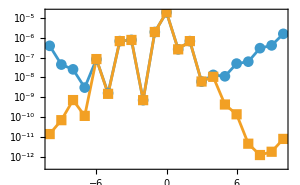

```mathematica
ListLogPlot[{Table[{modesk[[1,n]]["k"],Abs[Table[modesk[[i,n]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk[[1]]]}],Table[{modesk2[[1,n]]["k"],Abs[Table[modesk2[[i,n]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk2[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->MaTeX@{"k","| C^+_{S,lmnk} |"},PlotLegends->Placed[MaTeX@{"k_{\\max} = 8","k_{\\max} = 16"},{0.5,0.2}],FrameStyle->Black,ImageSize->300]
```

```mathematica
s=0.05`32;
```

```mathematica
lists={-2,-1,1,2}*s;
```

```mathematica
a=0.9`32
p=12.0`32
e=0.2`32
x=0.5`32
```

0.9

12.

0.2

0.5

Calculate analytical trajectories

```mathematica
orbits=Table[KerrSpinOrbit[a,p,e,x,lists[[i]],"Gauge"->"pex"],{i,1,4}];
```

```mathematica
l=2
m=2
n=0
```

2

2

0

```mathematica
Table[Table[TeukolskySpinModeAnalytical[l,m,n,k,orbits[[i]]],{k,-3,-3}],{i,1,4}]
```

32 steps in wr, 160 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 192 steps in wz

32 steps in wr, 192 steps in wz

{{<|l→2,m→2,k→-3,n→0,ω→-0.0203071807678445781258,Amplitudes→<|ℐ→2.282742019771265×10^-7-1.5683449400273717×10^-6 ⅈ,ℋ→-7.711922780061646×10^-6+0.000078744421541248417 ⅈ|>,α→0.00010111961972676559664,S→0.15897709091465920669,Fluxes→<|Energy→<|ℐ→4.847061269764847×10^-10,ℋ→1.221550894935328×10^-10|>,AngularMomentum→<|ℐ→-4.773741195469072×10^-8,ℋ→-1.203072852800516×10^-8|>,CarterConstantK→<|ℐ→2.593517904439532×10^-7,ℋ→6.536154467369888×10^-8|>|>,stepsr→32,stepsθ→160|>},{<|l→2,m→2,k→-3,n→0,ω→-0.0203079172509272165007,Amplitudes→<|ℐ→2.333304963252098×10^-7-1.6033727731464373×10^-6 ⅈ,ℋ→-7.594993272853748×10^-6+0.000077544930453922478 ⅈ|>,α→0.00010113096511562879435,S→0.1589771373963463829,Fluxes→<|Energy→<|ℐ→5.0655848914589795×10^-10,ℋ→1.184667865942539×10^-10|>,AngularMomentum→<|ℐ→-4.9887783457731941×10^-8,ℋ→-1.1667054295175933×10^-8|>,CarterConstantK→<|ℐ→2.7467402365849811×10^-7,ℋ→6.4236903814604341×10^-8|>|>,stepsr→32,stepsθ→160|>},{<|l→2,m→2,k→-3,n→0,ω→-0.0203337608617653238959,Amplitudes→<|ℐ→2.447877709047073×10^-7-1.6805836844942658×10^-6 ⅈ,ℋ→-7.376147203775346×10^-6+0.000075349575726850893 ⅈ|>,α→0.00010152963457014004437,S→0.15897876846574576931,Fluxes→<|Energy→<|ℐ→5.5512721447135403×10^-10,ℋ→1.1200854343257829×10^-10|>,AngularMomentum→<|ℐ→-5.4601528782133945×10^-8,ℋ→-1.1017002136893824×10^-8|>,CarterConstantK→<|ℐ→3.0853166570697758×10^-7,ℋ→6.2252726182007444×10^-8|>|>,stepsr→32,stepsθ→192|>},{<|l→2,m→2,k→-3,n→0,ω→-0.0203589999299665112455,Amplitudes→<|ℐ→2.512519530420914×10^-7-1.7230525024327042×10^-6 ⅈ,ℋ→-7.273837296735336×10^-6+0.000074348343881509478 ⅈ|>,α→0.00010192001772586567494,S→0.15898036138158892446,Fluxes→<|Energy→<|ℐ→5.821190584818179×10^-10,ℋ→1.091984485302097×10^-10|>,AngularMomentum→<|ℐ→-5.718542762260085×10^-8,ℋ→-1.072729003446579×10^-8|>,CarterConstantK→<|ℐ→3.272395797345017×10^-7,ℋ→6.138616127408851×10^-8|>|>,stepsr→32,stepsθ→192|>}}

Calculate Teukolsky amplitudes for different spins and k indices

```mathematica
modesAn=Table[Table[TeukolskySpinModeAnalytical[l,m,n,k,orbits[[i]]],{k,-10,10}],{i,1,4}];
```

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 224 steps in wz

64 steps in wr, 192 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

192 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 192 steps in wz

32 steps in wr, 160 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

192 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 224 steps in wz

32 steps in wr, 192 steps in wz

32 steps in wr, 128 steps in wz

32 steps in wr, 96 steps in wz

64 steps in wr, 64 steps in wz

64 steps in wr, 64 steps in wz

96 steps in wr, 96 steps in wz

96 steps in wr, 128 steps in wz

128 steps in wr, 160 steps in wz

128 steps in wr, 192 steps in wz

160 steps in wr, 224 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

160 steps in wr, 416 steps in wz

128 steps in wr, 384 steps in wz

128 steps in wr, 352 steps in wz

96 steps in wr, 320 steps in wz

96 steps in wr, 288 steps in wz

64 steps in wr, 256 steps in wz

64 steps in wr, 224 steps in wz

32 steps in wr, 192 steps in wz

32 steps in wr, 160 steps in wz

160 steps in wr, 256 steps in wz

192 steps in wr, 288 steps in wz

224 steps in wr, 320 steps in wz

224 steps in wr, 352 steps in wz

Plot numerically calculated linear parts of the amplitudes

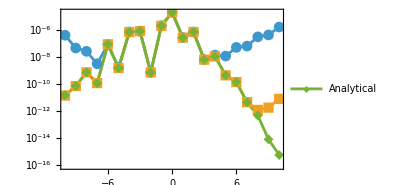

```mathematica
ListLogPlot[{Table[{modesk[[1,ik]]["k"],Abs[Table[modesk[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{ik,1,Length[modesk[[1]]]}],
Table[{modesk2[[1,ik]]["k"],Abs[Table[modesk2[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{ik,1,Length[modesk2[[1]]]}],
Table[{modesAn[[1,ik]]["k"],Abs[Table[modesAn[[i,ik]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{ik,1,Length[modesAn[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->MaTeX@{"k","| C^{+,1}_{220k} |"},PlotLegends->Placed[{MaTeX@"k^s_{\\max} = 8",MaTeX@"k^s_{\\max} = 16","Analytical"},{0.5,0.3}],FrameStyle->Black,ImageSize->300]
```

Plot numerically calculated linear parts of the fluxes

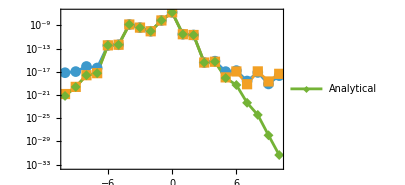

```mathematica
ListLogPlot[{Table[{modesk[[1,n]]["k"],Abs[Table[modesk[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modesk[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk[[1]]]}],
Table[{modesk2[[1,n]]["k"],Abs[Table[modesk2[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modesk2[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk2[[1]]]}],
Table[{modesAn[[1,n]]["k"],Abs[Table[modesAn[[i,n]]["Fluxes"]["Energy"]["ℐ"]+modesAn[[i,n]]["Fluxes"]["Energy"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesAn[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->MaTeX@{"k","| \\mathcal{F}^{E,1}_{220k} |"},PlotLegends->Placed[{MaTeX@"k^s_{\\max} = 8",MaTeX@"k^s_{\\max} = 16","Analytical"},{0.5,0.3}],FrameStyle->Black,ImageSize->300]
```

Plot relative differences between the linear parts of the fluxes

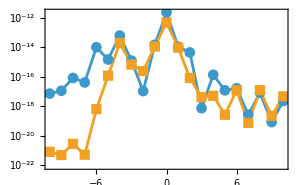

```mathematica
ListLogPlot[{Table[{modesk[[1,n]]["k"],Abs[Table[modesk[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05-Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk[[1]]]}],
Table[{modesk2[[1,n]]["k"],Abs[Table[modesk2[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05-Table[modesAn[[i,n]]["Fluxes"]["Energy"]//Total,{i,1,4}].{1/12,-2/3,2/3,-1/12}/0.05]},{n,1,Length[modesk2[[1]]]}]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->MaTeX@{"k","\\Delta \\mathcal{F}^{E,1}_{220k}"},PlotLegends->Placed[MaTeX@{"k^s_{\\max} = 8","k^s_{\\max} = 16"},{0.45,0.2}],FrameStyle->Black,ImageSize->300]
```